# Analysis of axisymmetric necking using the one-dimensional model of Yu and Fu (2024)

This Mathematica code produces the results presented in Section 5 of Yu  and Fu (2024).
It took 2 hours and 42 minutes to run this code on an Apple M2 Pro processor.

Note: Due to the existence of turning points in the loading curve,  we had to compute the growth stage and propagation stage of axisymmetric necking separately .

```mathematica
Clear["`*"](*Clear all variables*)
```

```mathematica
starttime= DateList[]
```

{2024,12,1,11,4,7.841869}

## 1. Growth stage of necking

#### 1. 1d energy functional, and interpolation using linear functions

```mathematica
ρ=μ^-1 λ^-1;
int=(w[ρ,μ]+N[1/24] H^2 w1[ρ,μ]/ρ λp^2-𝓆(μ+R μp-ρ))R;(*Integrand of the 1d energy functional given in eqn (5.12), μp=μ'[R], λp=λ'[R]. For the electroelastic case, modify this integrand to account for the contribution of the applied voltage*)
sublinear={μ->N[(1-ξ)] μ[j]+N[ξ] μ[1+j],μp->1/h(-μ[j]+μ[1+j]),λ->N[(1-ξ)] λ[j]+N[ξ] λ[1+j],λp->1/h(-λ[j]+λ[1+j]),𝓆->N[(1-ξ)] q[j]+N[ξ]q[1+j],R->h j+h ξ}; (*Linear interpolation rule*)
{ξ1,ξ2}={1/2(1-1/(√3)),1/2(1+1/(√3))}//N;(*Gaussian points of the interval [0,1]*)
{g1,g2}={1/2,1/2}//N;(*Gaussian weights*)
sub1=sublinear/.{ξ->ξ1};
sub2=sublinear/.{ξ->ξ2};
```

#### 2. Geometry and material parameters, and strain energy function

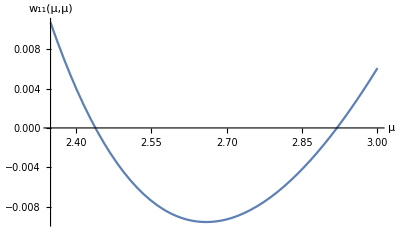

{2.43918,0.168078,1.97955}

```mathematica
H=N[2];(* Initial thickness*)
A=N[10];(*Initial radius*)
w[x_,y_]=N[(2 μ1)/m1^2](x^m1+y^m1+x^-m1 y^-m1-3.)+N[(2 μ2)/m2^2](x^m2+y^m2+x^-m2 y^-m2-3.)/.{μ1->N[1],m1->N[1/2],μ2->N[1/80],m2->N[4]};(*Strain energy function defined in eqn (5.16)*)
w1[x_,y_]=D[w[x,y],x];
w11[x_,y_]=D[w[x,y],{x,2}];
Plot[w11[x,x],{x,2.35,3},AxesLabel->{HoldForm[μ],HoldForm[Subscript[w, 11][μ,μ]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}](*Plot the graph of Subscript[w, 11](μ,μ) as a fucntion of μ*)
μcr=x/.FindRoot[w11[x,x]==0,{x,2}];(*Find critical value of μ, see eqn (5.6)*)
λcr=μcr^-2;
Pcr=w1[μcr,μcr];
bifpt={μcr,λcr,Pcr} (*Bifurcation point*)
```

#### 3. Discretization of the 1d energy functional, and its stationary conditions

```mathematica
n=1000; (*Number of mesh points*)
h=N[A/n];(*Mesh size*)
DateList[]
ℰ1d=Sum[g1(int/.sub1)+g2(int/.sub2),{j,0,n-1}]; (*Discretization of the integral given in eqn (5.12*)
eqμ0=μ[0]-μ0; (*μ0 is used as the control parameter*)
eqμ=Table[D[ℰ1d,μ[j]],{j,0,n-1}];
eqλ=Table[D[ℰ1d,λ[j]],{j,0,n}];
eqq=Table[D[ℰ1d,q[j]],{j,0,n}];
eqs=Join[{eqμ0==0},Table[eqμ[[j]]==0,{j,1,Length[eqμ]}],Table[eqλ[[j]]==0,{j,1,Length[eqλ]}],Table[eqq[[j]]==0,{j,1,Length[eqq]}]];(*3n+3 algebraric equations given by eqn (5.15)*)
DateList[]
P=h/A^2 D[ℰ1d,μ[n]];(*The tensile force at the edge*)
eqs//Length
```

{2024,12,1,11,4,7.968008}

{2024,12,1,11,5,24.635892}

3003

#### 4. Solving the system of algebraic equations near the bifurcation point, starting from μ0=μ0st=2.45

```mathematica
μ0st=2.45;(*The critical value of μ is Subscript[μ, cr]=2.439*)
μ0=μ0st;
yintp=InterpolatingFunction[…];(* "yintp" refers to the leading-order solution Subscript[y, 1][X] in the weakly nonlinear analysis, see eqn (5.9). It is computed using the finite difference scheme detailed in Fu and Yu, Mech. Mater. 2023*)
zintp=InterpolatingFunction[…];(* "zintp" refers to -2Subscript[y, 1][X}+R Subscript[y, 1]'[x]*)
μ∞=(-μ0+μcr yintp[0])/(-1+yintp[0]);(*"μ∞" refers to "a" in the paper*)
μw[R_]=μ∞+(μcr-μ∞)yintp[√(μcr-μ∞)R]; (* Weakly nonlinear solution of μ[R], see eqn (5.8)*)
λw[R_]=1/(μ∞)^2+((μcr-μ∞)zintp[√(μcr-μ∞)R])/(μ∞)^3;
qw[R_]=-Derivative[1,0][w][μcr,μcr]-(μcr-μ∞) (-1+yintp[√(μcr-μ∞)R]) Derivative[1,1][w][μcr,μcr];
guess=Join[Table[{μ[j],μw[j h]},{j,0,n}],Table[{λ[j],λw[ j h]},{j,0,n}],Table[{q[j],qw[j h]},{j,0,n}]];(*Use the weakly nonlinear solution as initial guess*)
guess//Length
DateList[]
solsub=FindRoot[eqs,guess];(*Find the solution using the Newton-Raphson method*)
DateList[]
```

3003

{2024,12,1,11,5,24.724267}

{2024,12,1,11,5,41.451136}

#### 5. Plot the graph of the 1d solution obtained above

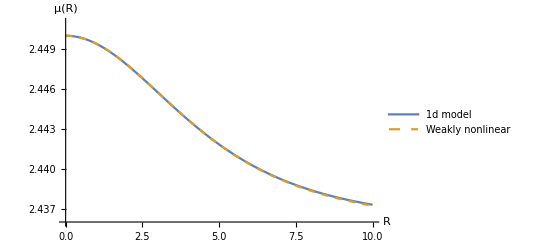

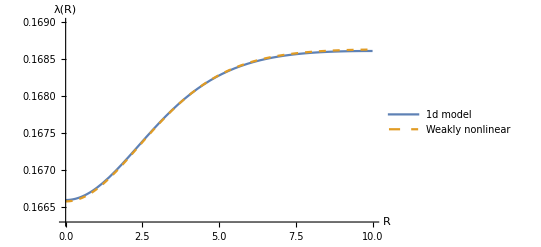

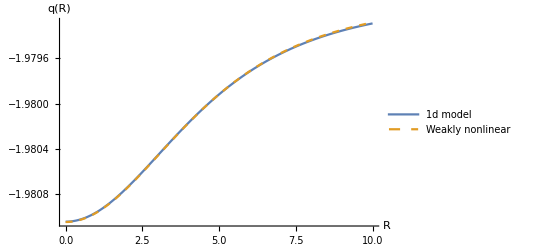

```mathematica
μ1d[R_]=Piecewise[Table[{((h+h j-R) μ[j]+(-h j+R) μ[1+j])/h/.solsub,j h<=R<(j+1)h},{j,0,n-1}]];
λ1d[R_]=Piecewise[Table[{((h+h j-R) λ[j]+(-h j+R) λ[1+j])/h/.solsub,j h<=R<(j+1)h},{j,0,n-1}]];
q1d[R_]=Piecewise[Table[{((h+h j-R) q[j]+(-h j+R) q[1+j])/h/.solsub,j h<=R<(j+1)h},{j,0,n-1}]];
Plot[{μ1d[R],μw[R]},{R,0,A},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.8}],AxesLabel->{HoldForm[R],HoldForm[μ[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->{{0,10},{2.436,2.451}}]
Plot[{λ1d[R],λw[R]},{R,0,A},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.3}],AxesLabel->{HoldForm[R],HoldForm[λ[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->{{0,10},{0.1663,0.169}}]
Plot[{q1d[R],qw[R]},{R,0,A},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.3}],AxesLabel->{HoldForm[R],HoldForm[q[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->Full]
dataload={{μ0,μ[0],μ[n],λ[0],λ[n],P}}/.solsub;
datasol={solsub};  (*Collect data*)
```

#### 6. Continue the solution to the fully nonlinear regime using a do-loop, using the solution at the previous step as the guess for the current step

```mathematica
kmax=200;(*Maximum iteration step*)
startime=DateList[]
Do[μ0=μ0st+k*0.01;
guess=Join[Table[{μ[j],μ[j]/.solsub},{j,0,n}],Table[{λ[j],λ[j]/.solsub},{j,0,n}],Table[{q[j],q[j]/.solsub},{j,0,n}]];
solsub=FindRoot[eqs,guess];
dataload=Append[dataload,{μ0,μ[0],μ[n],λ[0],λ[n],P}/.solsub];
datasol=Append[datasol,solsub];
Print[{k,μ0,μ[0],μ[n]}/.solsub],{k,1,kmax}];
endtime=DateList[]
```

{2024,12,1,11,5,44.499527}

{1,2.46,2.46,2.43366}

{2,2.47,2.47,2.43019}

{3,2.48,2.48,2.42682}

{4,2.49,2.49,2.42352}

{5,2.5,2.5,2.42031}

{6,2.51,2.51,2.41716}

{7,2.52,2.52,2.41408}

{8,2.53,2.53,2.41106}

{9,2.54,2.54,2.4081}

{10,2.55,2.55,2.40521}

{11,2.56,2.56,2.40237}

{12,2.57,2.57,2.39958}

{13,2.58,2.58,2.39685}

{14,2.59,2.59,2.39417}

{15,2.6,2.6,2.39154}

{16,2.61,2.61,2.38896}

{17,2.62,2.62,2.38642}

{18,2.63,2.63,2.38393}

{19,2.64,2.64,2.38148}

{20,2.65,2.65,2.37907}

{21,2.66,2.66,2.37671}

{22,2.67,2.67,2.37438}

{23,2.68,2.68,2.37209}

{24,2.69,2.69,2.36984}

{25,2.7,2.7,2.36763}

{26,2.71,2.71,2.36545}

{27,2.72,2.72,2.3633}

{28,2.73,2.73,2.36119}

{29,2.74,2.74,2.35911}

{30,2.75,2.75,2.35706}

{31,2.76,2.76,2.35504}

{32,2.77,2.77,2.35305}

{33,2.78,2.78,2.35109}

{34,2.79,2.79,2.34916}

{35,2.8,2.8,2.34725}

{36,2.81,2.81,2.34537}

{37,2.82,2.82,2.34352}

{38,2.83,2.83,2.34168}

{39,2.84,2.84,2.33988}

{40,2.85,2.85,2.33809}

{41,2.86,2.86,2.33633}

{42,2.87,2.87,2.33459}

{43,2.88,2.88,2.33287}

{44,2.89,2.89,2.33118}

{45,2.9,2.9,2.3295}

{46,2.91,2.91,2.32784}

{47,2.92,2.92,2.3262}

{48,2.93,2.93,2.32457}

{49,2.94,2.94,2.32297}

{50,2.95,2.95,2.32138}

{51,2.96,2.96,2.3198}

{52,2.97,2.97,2.31824}

{53,2.98,2.98,2.3167}

{54,2.99,2.99,2.31517}

{55,3.,3.,2.31365}

{56,3.01,3.01,2.31215}

{57,3.02,3.02,2.31066}

{58,3.03,3.03,2.30918}

{59,3.04,3.04,2.30771}

{60,3.05,3.05,2.30625}

{61,3.06,3.06,2.3048}

{62,3.07,3.07,2.30336}

{63,3.08,3.08,2.30193}

{64,3.09,3.09,2.30051}

{65,3.1,3.1,2.29909}

{66,3.11,3.11,2.29768}

{67,3.12,3.12,2.29627}

{68,3.13,3.13,2.29487}

{69,3.14,3.14,2.29348}

{70,3.15,3.15,2.29208}

{71,3.16,3.16,2.29069}

{72,3.17,3.17,2.28931}

{73,3.18,3.18,2.28792}

{74,3.19,3.19,2.28653}

{75,3.2,3.2,2.28514}

{76,3.21,3.21,2.28375}

{77,3.22,3.22,2.28236}

{78,3.23,3.23,2.28096}

{79,3.24,3.24,2.27956}

{80,3.25,3.25,2.27815}

{81,3.26,3.26,2.27674}

{82,3.27,3.27,2.27531}

{83,3.28,3.28,2.27388}

{84,3.29,3.29,2.27243}

{85,3.3,3.3,2.27098}

{86,3.31,3.31,2.2695}

{87,3.32,3.32,2.26801}

{88,3.33,3.33,2.2665}

{89,3.34,3.34,2.26497}

{90,3.35,3.35,2.26342}

{91,3.36,3.36,2.26185}

{92,3.37,3.37,2.26024}

{93,3.38,3.38,2.25861}

{94,3.39,3.39,2.25694}

{95,3.4,3.4,2.25523}

{96,3.41,3.41,2.25349}

{97,3.42,3.42,2.2517}

{98,3.43,3.43,2.24986}

{99,3.44,3.44,2.24798}

{100,3.45,3.45,2.24603}

{101,3.46,3.46,2.24403}

{102,3.47,3.47,2.24196}

{103,3.48,3.48,2.23982}

{104,3.49,3.49,2.23761}

{105,3.5,3.5,2.23531}

{106,3.51,3.51,2.23294}

{107,3.52,3.52,2.23048}

{108,3.53,3.53,2.22794}

{109,3.54,3.54,2.22531}

{110,3.55,3.55,2.2226}

{111,3.56,3.56,2.21981}

{112,3.57,3.57,2.21696}

{113,3.58,3.58,2.21404}

{114,3.59,3.59,2.21106}

{115,3.6,3.6,2.20806}

{116,3.61,3.61,2.20502}

{117,3.62,3.62,2.20198}

{118,3.63,3.63,2.19894}

{119,3.64,3.64,2.19591}

{120,3.65,3.65,2.19292}

{121,3.66,3.66,2.18997}

{122,3.67,3.67,2.18709}

{123,3.68,3.68,2.18429}

{124,3.69,3.69,2.18161}

{125,3.7,3.7,2.17907}

{126,3.71,3.71,2.17674}

{127,3.72,3.72,2.17469}

{128,3.73,3.73,2.17303}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{129,3.74,3.73721,2.1722}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{130,3.75,3.74317,2.17181}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{131,3.76,3.74769,2.17172}

{132,3.77,3.752,2.17185}

{133,3.78,3.75605,2.17219}

{134,3.79,3.7599,2.17277}

{135,3.8,3.76294,2.17342}

{136,3.81,3.76648,2.17446}

{137,3.82,3.76901,2.17542}

{138,3.83,3.7714,2.17652}

{139,3.84,3.77402,2.17799}

{140,3.85,3.77607,2.17934}

{141,3.86,3.77789,2.18073}

{142,3.87,3.77967,2.18229}

{143,3.88,3.78131,2.18391}

{144,3.89,3.78297,2.18574}

{145,3.9,3.78449,2.18761}

{146,3.91,3.78577,2.18935}

{147,3.92,3.78698,2.19117}

{148,3.93,3.78814,2.19309}

{149,3.94,3.78932,2.19519}

{150,3.95,3.79041,2.19728}

{151,3.96,3.79135,2.19921}

{152,3.97,3.7922,2.20113}

{153,3.98,3.79302,2.2031}

{154,3.99,3.79382,2.20517}

{155,4.,3.79465,2.20742}

{156,4.01,3.79549,2.20979}

{157,4.02,3.7962,2.21192}

{158,4.03,3.79684,2.21398}

{159,4.04,3.79743,2.21601}

{160,4.05,3.79799,2.21803}

{161,4.06,3.79853,2.22011}

{162,4.07,3.79909,2.22232}

{163,4.08,3.79964,2.2246}

{164,4.09,3.8002,2.22695}

{165,4.1,3.80073,2.2293}

{166,4.11,3.8012,2.23146}

{167,4.12,3.80164,2.23357}

{168,4.13,3.80205,2.23564}

{169,4.14,3.80245,2.23778}

{170,4.15,3.80286,2.24005}

{171,4.16,3.80325,2.24224}

{172,4.17,3.80363,2.24445}

{173,4.18,3.804,2.24676}

{174,4.19,3.80438,2.2491}

{175,4.2,3.80475,2.2515}

{176,4.21,3.80513,2.25396}

{177,4.22,3.80546,2.25619}

{178,4.23,3.80577,2.25837}

{179,4.24,3.80606,2.26051}

{180,4.25,3.80633,2.26261}

{181,4.26,3.8066,2.2647}

{182,4.27,3.80685,2.26679}

{183,4.28,3.8071,2.26888}

{184,4.29,3.80735,2.27105}

{185,4.3,3.8076,2.27324}

{186,4.31,3.80784,2.27539}

{187,4.32,3.80809,2.27765}

{188,4.33,3.80834,2.27996}

{189,4.34,3.80858,2.28215}

{190,4.35,3.80882,2.28447}

{191,4.36,3.80907,2.28693}

{192,4.37,3.8093,2.28914}

{193,4.38,3.80951,2.29134}

{194,4.39,3.80972,2.29347}

{195,4.4,3.80991,2.29562}

{196,4.41,3.8101,2.2977}

{197,4.42,3.81028,2.29983}

{198,4.43,3.81046,2.30191}

{199,4.44,3.81064,2.30409}

{200,4.45,3.81081,2.30618}

{2024,12,1,12,35,17.856935}

#### 7. Output the results calculated above

```mathematica
kend=128 (*The numerical continuation fails to converge at k=128, since μ[0] almost attains its maximum at the step and  can not be increased further.*)
datasol(* "datasol" consists of all solution calculated in the iteration procedure, so it is very large. Please save it in a separate file for later use.*)
dataAmp=Join[{{μcr,0}},Table[{μ[n],λ[n]-λ[0]}/.datasol[[i]],{i,1,Length[datasol]}]] (* λ[A]-λ[0] versus μ[0]*)
dataμ0=Join[{{μcr,μcr}},Table[{μ[n],μ[0]}/.datasol[[i]],{i,1,Length[datasol]}]]  (* μ[0] versus μ[n]*)
```

128

{{μ[0]→2.45,μ[1]→2.45,μ[2]→2.45,μ[3]→2.45,μ[4]→2.45,μ[5]→2.45,μ[6]→2.45,μ[7]→2.45,μ[8]→2.45,μ[9]→2.44999,μ[10]→2.44999,2982,q[991]→-1.9793,q[992]→-1.9793,q[993]→-1.9793,q[994]→-1.9793,q[995]→-1.97929,q[996]→-1.97929,q[997]→-1.97929,q[998]→-1.97929,q[999]→-1.97929,q[1000]→-1.97929},199,{1}}
 |  |  |  |

{{2.43918,0},{2.4373,0.00201637},{2.43366,0.00388192},{2.43019,0.00569036},{2.42682,0.00747431},{2.42352,0.00923569},{2.42031,0.0109744},{2.41716,0.0126906},{2.41408,0.0143844},{2.41106,0.0160562},{2.4081,0.0177063},{2.40521,0.0193353},{2.40237,0.0209435},{2.39958,0.0225313},{2.39685,0.0240992},{2.39417,0.0256474},{2.39154,0.0271764},{2.38896,0.0286865},{2.38642,0.0301782},{2.38393,0.0316517},{2.38148,0.0331074},{2.37907,0.0345456},{2.37671,0.0359667},{2.37438,0.037371},{2.37209,0.0387588},{2.36984,0.0401303},{2.36763,0.0414859},{2.36545,0.0428259},{2.3633,0.0441505},{2.36119,0.04546},{2.35911,0.0467547},{2.35706,0.0480349},{2.35504,0.0493007},{2.35305,0.0505526},{2.35109,0.0517906},{2.34916,0.0530151},{2.34725,0.0542262},{2.34537,0.0554243},{2.34352,0.0566096},{2.34168,0.0577822},{2.33988,0.0589425},{2.33809,0.0600906},{2.33633,0.0612267},{2.33459,0.0623511},{2.33287,0.0634639},{2.33118,0.0645655},{2.3295,0.0656559},{2.32784,0.0667354},{2.3262,0.0678042},{2.32457,0.0688624},{2.32297,0.0699104},{2.32138,0.0709482},{2.3198,0.0719762},{2.31824,0.0729943},{2.3167,0.074003},{2.31517,0.0750023},{2.31365,0.0759924},{2.31215,0.0769735},{2.31066,0.0779459},{2.30918,0.0789097},{2.30771,0.079865},{2.30625,0.0808121},{2.3048,0.0817512},{2.30336,0.0826825},{2.30193,0.0836061},{2.30051,0.0845222},{2.29909,0.0854311},{2.29768,0.0863329},{2.29627,0.0872278},{2.29487,0.088116},{2.29348,0.0889978},{2.29208,0.0898733},{2.29069,0.0907427},{2.28931,0.0916063},{2.28792,0.0924643},{2.28653,0.0933168},{2.28514,0.0941642},{2.28375,0.0950067},{2.28236,0.0958445},{2.28096,0.0966779},{2.27956,0.0975071},{2.27815,0.0983324},{2.27674,0.0991541},{2.27531,0.0999726},{2.27388,0.100788},{2.27243,0.101601},{2.27098,0.102411},{2.2695,0.10322},{2.26801,0.104027},{2.2665,0.104833},{2.26497,0.105638},{2.26342,0.106444},{2.26185,0.107249},{2.26024,0.108055},{2.25861,0.108863},{2.25694,0.109673},{2.25523,0.110486},{2.25349,0.111302},{2.2517,0.112123},{2.24986,0.112949},{2.24798,0.11378},{2.24603,0.114619},{2.24403,0.115466},{2.24196,0.116322},{2.23982,0.117188},{2.23761,0.118065},{2.23531,0.118955},{2.23294,0.119857},{2.23048,0.120774},{2.22794,0.121706},{2.22531,0.122652},{2.2226,0.123614},{2.21981,0.12459},{2.21696,0.125581},{2.21404,0.126584},{2.21106,0.1276},{2.20806,0.128625},{2.20502,0.129659},{2.20198,0.130699},{2.19894,0.131746},{2.19591,0.132796},{2.19292,0.13385},{2.18997,0.134906},{2.18709,0.135965},{2.18429,0.137025},{2.18161,0.138088},{2.17907,0.139151},{2.17674,0.140217},{2.17469,0.141284},{2.17303,0.142352},{2.1722,0.143111},{2.17181,0.143734},{2.17172,0.144208},{2.17185,0.144658},{2.17219,0.145082},{2.17277,0.145485},{2.17342,0.145808},{2.17446,0.146183},{2.17542,0.146452},{2.17652,0.146709},{2.17799,0.146991},{2.17934,0.147209},{2.18073,0.147406},{2.18229,0.147601},{2.18391,0.147781},{2.18574,0.147959},{2.18761,0.148122},{2.18935,0.14826},{2.19117,0.148392},{2.19309,0.14852},{2.19519,0.148649},{2.19728,0.148765},{2.19921,0.148866},{2.20113,0.14896},{2.2031,0.14905},{2.20517,0.14914},{2.20742,0.149231},{2.20979,0.14932},{2.21192,0.149395},{2.21398,0.149465},{2.21601,0.14953},{2.21803,0.149592},{2.22011,0.149653},{2.22232,0.149716},{2.2246,0.149776},{2.22695,0.149836},{2.2293,0.149892},{2.23146,0.149942},{2.23357,0.149989},{2.23564,0.150033},{2.23778,0.150077},{2.24005,0.150122},{2.24224,0.150165},{2.24445,0.150205},{2.24676,0.150246},{2.2491,0.150286},{2.2515,0.150326},{2.25396,0.150365},{2.25619,0.150399},{2.25837,0.150431},{2.26051,0.150461},{2.26261,0.150491},{2.2647,0.150519},{2.26679,0.150547},{2.26888,0.150573},{2.27105,0.1506},{2.27324,0.150627},{2.27539,0.150652},{2.27765,0.150677},{2.27996,0.150703},{2.28215,0.150726},{2.28447,0.150749},{2.28693,0.150774},{2.28914,0.150795},{2.29134,0.150815},{2.29347,0.150835},{2.29562,0.150854},{2.2977,0.150871},{2.29983,0.150889},{2.30191,0.150906},{2.30409,0.150924},{2.30618,0.15094}}

{{2.43918,2.43918},{2.4373,2.45},{2.43366,2.46},{2.43019,2.47},{2.42682,2.48},{2.42352,2.49},{2.42031,2.5},{2.41716,2.51},{2.41408,2.52},{2.41106,2.53},{2.4081,2.54},{2.40521,2.55},{2.40237,2.56},{2.39958,2.57},{2.39685,2.58},{2.39417,2.59},{2.39154,2.6},{2.38896,2.61},{2.38642,2.62},{2.38393,2.63},{2.38148,2.64},{2.37907,2.65},{2.37671,2.66},{2.37438,2.67},{2.37209,2.68},{2.36984,2.69},{2.36763,2.7},{2.36545,2.71},{2.3633,2.72},{2.36119,2.73},{2.35911,2.74},{2.35706,2.75},{2.35504,2.76},{2.35305,2.77},{2.35109,2.78},{2.34916,2.79},{2.34725,2.8},{2.34537,2.81},{2.34352,2.82},{2.34168,2.83},{2.33988,2.84},{2.33809,2.85},{2.33633,2.86},{2.33459,2.87},{2.33287,2.88},{2.33118,2.89},{2.3295,2.9},{2.32784,2.91},{2.3262,2.92},{2.32457,2.93},{2.32297,2.94},{2.32138,2.95},{2.3198,2.96},{2.31824,2.97},{2.3167,2.98},{2.31517,2.99},{2.31365,3.},{2.31215,3.01},{2.31066,3.02},{2.30918,3.03},{2.30771,3.04},{2.30625,3.05},{2.3048,3.06},{2.30336,3.07},{2.30193,3.08},{2.30051,3.09},{2.29909,3.1},{2.29768,3.11},{2.29627,3.12},{2.29487,3.13},{2.29348,3.14},{2.29208,3.15},{2.29069,3.16},{2.28931,3.17},{2.28792,3.18},{2.28653,3.19},{2.28514,3.2},{2.28375,3.21},{2.28236,3.22},{2.28096,3.23},{2.27956,3.24},{2.27815,3.25},{2.27674,3.26},{2.27531,3.27},{2.27388,3.28},{2.27243,3.29},{2.27098,3.3},{2.2695,3.31},{2.26801,3.32},{2.2665,3.33},{2.26497,3.34},{2.26342,3.35},{2.26185,3.36},{2.26024,3.37},{2.25861,3.38},{2.25694,3.39},{2.25523,3.4},{2.25349,3.41},{2.2517,3.42},{2.24986,3.43},{2.24798,3.44},{2.24603,3.45},{2.24403,3.46},{2.24196,3.47},{2.23982,3.48},{2.23761,3.49},{2.23531,3.5},{2.23294,3.51},{2.23048,3.52},{2.22794,3.53},{2.22531,3.54},{2.2226,3.55},{2.21981,3.56},{2.21696,3.57},{2.21404,3.58},{2.21106,3.59},{2.20806,3.6},{2.20502,3.61},{2.20198,3.62},{2.19894,3.63},{2.19591,3.64},{2.19292,3.65},{2.18997,3.66},{2.18709,3.67},{2.18429,3.68},{2.18161,3.69},{2.17907,3.7},{2.17674,3.71},{2.17469,3.72},{2.17303,3.73},{2.1722,3.73721},{2.17181,3.74317},{2.17172,3.74769},{2.17185,3.752},{2.17219,3.75605},{2.17277,3.7599},{2.17342,3.76294},{2.17446,3.76648},{2.17542,3.76901},{2.17652,3.7714},{2.17799,3.77402},{2.17934,3.77607},{2.18073,3.77789},{2.18229,3.77967},{2.18391,3.78131},{2.18574,3.78297},{2.18761,3.78449},{2.18935,3.78577},{2.19117,3.78698},{2.19309,3.78814},{2.19519,3.78932},{2.19728,3.79041},{2.19921,3.79135},{2.20113,3.7922},{2.2031,3.79302},{2.20517,3.79382},{2.20742,3.79465},{2.20979,3.79549},{2.21192,3.7962},{2.21398,3.79684},{2.21601,3.79743},{2.21803,3.79799},{2.22011,3.79853},{2.22232,3.79909},{2.2246,3.79964},{2.22695,3.8002},{2.2293,3.80073},{2.23146,3.8012},{2.23357,3.80164},{2.23564,3.80205},{2.23778,3.80245},{2.24005,3.80286},{2.24224,3.80325},{2.24445,3.80363},{2.24676,3.804},{2.2491,3.80438},{2.2515,3.80475},{2.25396,3.80513},{2.25619,3.80546},{2.25837,3.80577},{2.26051,3.80606},{2.26261,3.80633},{2.2647,3.8066},{2.26679,3.80685},{2.26888,3.8071},{2.27105,3.80735},{2.27324,3.8076},{2.27539,3.80784},{2.27765,3.80809},{2.27996,3.80834},{2.28215,3.80858},{2.28447,3.80882},{2.28693,3.80907},{2.28914,3.8093},{2.29134,3.80951},{2.29347,3.80972},{2.29562,3.80991},{2.2977,3.8101},{2.29983,3.81028},{2.30191,3.81046},{2.30409,3.81064},{2.30618,3.81081}}

#### 8. Loading curves of necking growth

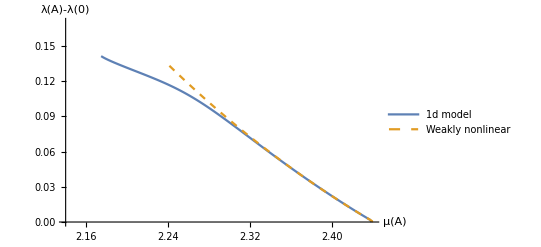

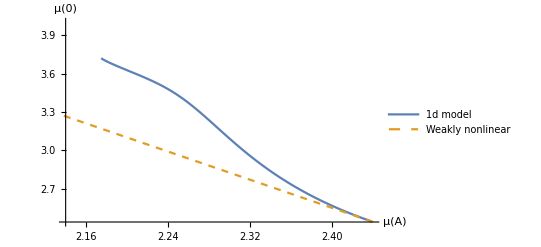

```mathematica
Clear[μ∞]
μ∞=(x-yintp[0] μcr)/(1-yintp[0]);(*“x” stands for “μ0”. Given μ0, μ∞ is determiend from μ[R]=μ∞+(μcr-μ∞)yintp[√(μcr-μ∞)A]*)
dataAmpw=Table[{μ∞+(μcr-μ∞)yintp[√(μcr-μ∞)A],((μcr-μ∞)zintp[√(μcr-μ∞)A])/(μ∞)^3-((μcr-μ∞)zintp[0])/(μ∞)^3},{x,μcr,3,0.004}];(* λ[A]-λ[n] versus μ[n] given by weakly nonlinear analysis*)
dataμ0w=Table[{μ∞+(μcr-μ∞)yintp[√(μcr-μ∞)A],x},{x,μcr,3.5,0.004}];(* μ[0] versus μ[n] given by weakly nonlinear analysis*)
ListPlot[{dataAmp[[1;;kend+1]],dataAmpw},Joined->True,AxesLabel->{HoldForm[μ[A]],HoldForm[λ[A]-λ[0]]},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.3,0.2}],LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->{{2.14,2.44},{0,0.17}}]
ListPlot[{dataμ0[[1;;kend+1]],dataμ0w},Joined->True,AxesLabel->{HoldForm[μ[A]],HoldForm[μ[0]]},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.3,0.2}],LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->{{2.14,2.44},{2.44,4}}]
```

```mathematica
Print["end of growth stage", DateList[]]
```

end of growth stage{2024,12,1,12,35,24.256417}

## 2 Propagation stage of necking

#### 1. Stationary conditions of the discretized 1d energy functional, but now we use μA as the control parameter

```mathematica
Clear[μA,eqs];
eqμA=μ[n]-μA; (* μA is used as the control paramter*)
eqs=Join[Table[eqμ[[j]]==0,{j,1,Length[eqμ]}],{eqμA==0},Table[eqλ[[j]]==0,{j,1,Length[eqλ]}],Table[eqq[[j]]==0,{j,1,Length[eqq]}]];
eqs//Length
```

3003

#### 2. Solving the system of algebraic equations in the propagation stage, starting from μA=μAst=2.19.

```mathematica
μAst=2.19;
μA=μAst;
inisub=datasol[[146]];(*initial guess for the necking in the propgation stage*)
guess=Join[Table[{μ[j],μ[j]/.inisub},{j,0,n}],Table[{λ[j],λ[j]/.inisub},{j,0,n}],Table[{q[j],q[j]/.inisub},{j,0,n}]];
guess//Length
DateList[]
solsub=FindRoot[eqs,guess];
DateList[]
```

3003

{2024,12,1,12,35,25.748021}

{2024,12,1,12,35,43.524734}

#### 3. Plot the graph of the 1d solution obtained above

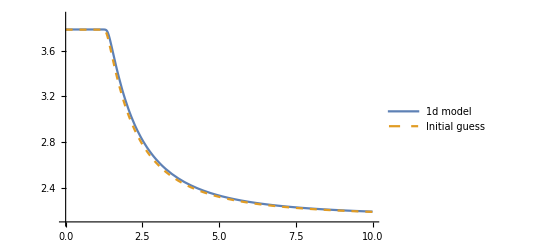

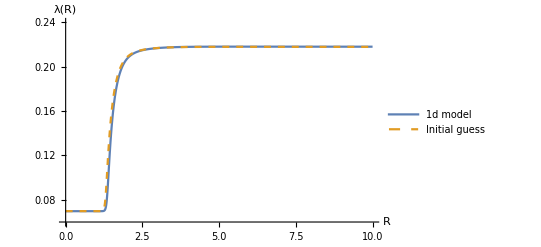

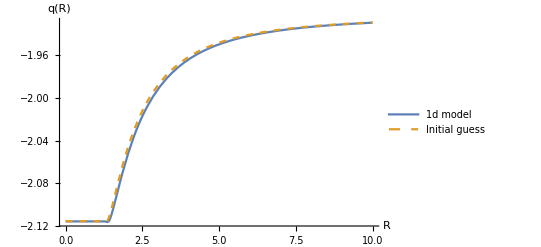

```mathematica
μguess[R_]=Piecewise[Table[{((h+h j-R) μ[j]+(-h j+R) μ[1+j])/h/.inisub,j h<=R<(j+1)h},{j,0,n-1}]];
λguess[R_]=Piecewise[Table[{((h+h j-R) λ[j]+(-h j+R) λ[1+j])/h/.inisub,j h<=R<(j+1)h},{j,0,n-1}]];
qguess[R_]=Piecewise[Table[{((h+h j-R) q[j]+(-h j+R) q[1+j])/h/.inisub,j h<=R<(j+1)h},{j,0,n-1}]];
μ1d[R_]=Piecewise[Table[{((h+h j-R) μ[j]+(-h j+R) μ[1+j])/h/.solsub,j h<=R<(j+1)h},{j,0,n-1}]];
λ1d[R_]=Piecewise[Table[{((h+h j-R) λ[j]+(-h j+R) λ[1+j])/h/.solsub,j h<=R<(j+1)h},{j,0,n-1}]];
q1d[R_]=Piecewise[Table[{((h+h j-R) q[j]+(-h j+R) q[1+j])/h/.solsub,j h<=R<(j+1)h},{j,0,n-1}]];
Plot[{μ1d[R],μguess[R]},{R,0,A},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Initial guess"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.5}],LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->{{0,10},{2.1,3.9}}]
Plot[{λ1d[R],λguess[R]},{R,0,A},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Initial guess"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.4}],AxesLabel->{HoldForm[R],HoldForm[λ[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->{{0,10},{0.06,0.24}}]
Plot[{q1d[R],qguess[R]},{R,0,A},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Initial guess"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.5}],AxesLabel->{HoldForm[R],HoldForm[q[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->Full]
dataload2={{μA,μ[n],μ[0],λ[0],λ[n],P}}/.solsub;
datasol2={solsub};
```

#### 4. Continue the solution to the fully nonlinear regime using a do-loop, using the solution at the previous step as the guess for the current step

```mathematica
kmax=200;
startime=DateList[]
Do[μA=μAst+k*0.01;
guess=Join[Table[{μ[j],1.005*μ[j]/.solsub},{j,0,n}],Table[{λ[j],1.005*λ[j]/.solsub},{j,0,n}],Table[{q[j],1.005*q[j]/.solsub},{j,0,n}]];
solsub=FindRoot[eqs,guess];
dataload2=Append[dataload2,{μA,μ[n],μ[0],λ[0],λ[n],P}/.solsub];
datasol2=Append[datasol2,solsub];
Print[{k,μA,μ[n],μ[0]}/.solsub],{k,1,kmax}];
endtime=DateList[]
```

{2024,12,1,12,35,49.555063}

{1,2.2,2.2,3.79141}

{2,2.21,2.21,3.79528}

{3,2.22,2.22,3.79823}

{4,2.23,2.23,3.80061}

{5,2.24,2.24,3.80257}

{6,2.25,2.25,3.80424}

{7,2.26,2.26,3.80568}

{8,2.27,2.27,3.80695}

{9,2.28,2.28,3.80807}

{10,2.29,2.29,3.80908}

{11,2.3,2.3,3.80999}

{12,2.31,2.31,3.81081}

{13,2.32,2.32,3.81157}

{14,2.33,2.33,3.81226}

{15,2.34,2.34,3.81291}

{16,2.35,2.35,3.81351}

{17,2.36,2.36,3.81406}

{18,2.37,2.37,3.81458}

{19,2.38,2.38,3.81507}

{20,2.39,2.39,3.81553}

{21,2.4,2.4,3.81597}

{22,2.41,2.41,3.81638}

{23,2.42,2.42,3.81676}

{24,2.43,2.43,3.81713}

{25,2.44,2.44,3.81748}

{26,2.45,2.45,3.81782}

{27,2.46,2.46,3.81814}

{28,2.47,2.47,3.81844}

{29,2.48,2.48,3.81873}

{30,2.49,2.49,3.81901}

{31,2.5,2.5,3.81928}

{32,2.51,2.51,3.81954}

{33,2.52,2.52,3.81979}

{34,2.53,2.53,3.82003}

{35,2.54,2.54,3.82026}

{36,2.55,2.55,3.82048}

{37,2.56,2.56,3.82069}

{38,2.57,2.57,3.8209}

{39,2.58,2.58,3.8211}

{40,2.59,2.59,3.8213}

{41,2.6,2.6,3.82148}

{42,2.61,2.61,3.82167}

{43,2.62,2.62,3.82184}

{44,2.63,2.63,3.82201}

{45,2.64,2.64,3.82218}

{46,2.65,2.65,3.82234}

{47,2.66,2.66,3.8225}

{48,2.67,2.67,3.82265}

{49,2.68,2.68,3.8228}

{50,2.69,2.69,3.82295}

{51,2.7,2.7,3.82309}

{52,2.71,2.71,3.82323}

{53,2.72,2.72,3.82336}

{54,2.73,2.73,3.82349}

{55,2.74,2.74,3.82362}

{56,2.75,2.75,3.82375}

{57,2.76,2.76,3.82387}

{58,2.77,2.77,3.82399}

{59,2.78,2.78,3.82411}

{60,2.79,2.79,3.82422}

{61,2.8,2.8,3.82433}

{62,2.81,2.81,3.82444}

{63,2.82,2.82,3.82455}

{64,2.83,2.83,3.82465}

{65,2.84,2.84,3.82476}

{66,2.85,2.85,3.82486}

{67,2.86,2.86,3.82496}

{68,2.87,2.87,3.82505}

{69,2.88,2.88,3.82515}

{70,2.89,2.89,3.82524}

{71,2.9,2.9,3.82533}

{72,2.91,2.91,3.82542}

{73,2.92,2.92,3.82551}

{74,2.93,2.93,3.8256}

{75,2.94,2.94,3.82568}

{76,2.95,2.95,3.82576}

{77,2.96,2.96,3.82585}

{78,2.97,2.97,3.82593}

{79,2.98,2.98,3.82601}

{80,2.99,2.99,3.82608}

{81,3.,3.,3.82616}

{82,3.01,3.01,3.82623}

{83,3.02,3.02,3.82631}

{84,3.03,3.03,3.82638}

{85,3.04,3.04,3.82645}

{86,3.05,3.05,3.82652}

{87,3.06,3.06,3.82659}

{88,3.07,3.07,3.82666}

{89,3.08,3.08,3.82673}

{90,3.09,3.09,3.82679}

{91,3.1,3.1,3.82686}

{92,3.11,3.11,3.82692}

{93,3.12,3.12,3.82699}

{94,3.13,3.13,3.82705}

{95,3.14,3.14,3.82711}

{96,3.15,3.15,3.82717}

{97,3.16,3.16,3.82723}

{98,3.17,3.17,3.82729}

{99,3.18,3.18,3.82735}

{100,3.19,3.19,3.82741}

{101,3.2,3.2,3.82746}

{102,3.21,3.21,3.82752}

{103,3.22,3.22,3.82757}

{104,3.23,3.23,3.82763}

{105,3.24,3.24,3.82768}

{106,3.25,3.25,3.82773}

{107,3.26,3.26,3.82778}

{108,3.27,3.27,3.82784}

{109,3.28,3.28,3.82789}

{110,3.29,3.29,3.82794}

{111,3.3,3.3,3.82799}

{112,3.31,3.31,3.82804}

{113,3.32,3.32,3.82808}

{114,3.33,3.33,3.82813}

{115,3.34,3.34,3.82818}

{116,3.35,3.35,3.82823}

{117,3.36,3.36,3.82827}

{118,3.37,3.37,3.82832}

{119,3.38,3.38,3.82836}

{120,3.39,3.39,3.82841}

{121,3.4,3.4,3.82845}

{122,3.41,3.41,3.82849}

{123,3.42,3.42,3.82854}

{124,3.43,3.43,3.82858}

{125,3.44,3.44,3.82862}

{126,3.45,3.45,3.82866}

{127,3.46,3.46,3.8287}

{128,3.47,3.47,3.82874}

{129,3.48,3.48,3.82878}

{130,3.49,3.49,3.82882}

{131,3.5,3.5,3.82885}

{132,3.51,3.51,3.82889}

{133,3.52,3.52,3.82892}

{134,3.53,3.53,3.82895}

{135,3.54,3.54,3.82898}

{136,3.55,3.55,3.82901}

{137,3.56,3.56,3.82903}

{138,3.57,3.57,3.82905}

{139,3.58,3.58,3.82905}

{140,3.59,3.59,3.82905}

{141,3.6,3.6,3.82902}

{142,3.61,3.61,3.82897}

{143,3.62,3.62,3.82889}

{144,3.63,3.63,3.82875}

{145,3.64,3.64,3.82853}

{146,3.65,3.65,3.82819}

{147,3.66,3.66,3.82767}

{148,3.67,3.67,3.82687}

{149,3.68,3.68,3.8256}

{150,3.69,3.69,3.82349}

{151,3.7,3.7,3.81952}

{152,3.71,3.71,3.80408}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{153,3.72,3.72,3.79652}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{154,3.73,3.73,3.80114}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{155,3.74,3.74,3.81034}

{156,3.75,3.75,3.82022}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{157,3.76,3.76,3.8363}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{158,3.77,3.77,3.84848}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{159,3.78,3.78,3.86072}

{160,3.79,3.79,3.87289}

{161,3.8,3.8,3.88442}

{162,3.81,3.81,3.89564}

{163,3.82,3.82,3.90623}

{164,3.83,3.83123,3.90739}

{165,3.84,3.84,3.90591}

{166,3.85,3.85162,3.9068}

{167,3.86,3.86218,3.90903}

{168,3.87,3.87201,3.91168}

{169,3.88,3.88209,3.91615}

{170,3.89,3.89355,3.9226}

{171,3.9,3.90331,3.92768}

{172,3.91,3.91,3.93267}

{173,3.92,3.92525,3.9408}

{174,3.93,3.93,3.93}

{175,3.94,3.94,3.94}

{176,3.95,3.95,3.95}

{177,3.96,3.96,3.96}

{178,3.97,3.97,3.97}

{179,3.98,3.98,3.98}

{180,3.99,3.99,3.99}

{181,4.,4.,4.}

{182,4.01,4.01,4.01}

{183,4.02,4.02,4.02}

{184,4.03,4.03,4.03}

{185,4.04,4.04,4.04}

{186,4.05,4.05,4.05}

{187,4.06,4.06,4.06}

{188,4.07,4.07,4.07}

{189,4.08,4.08,4.08}

{190,4.09,4.09,4.09}

{191,4.1,4.1,4.1}

{192,4.11,4.11,4.11}

{193,4.12,4.12,4.12}

{194,4.13,4.13,4.13}

{195,4.14,4.14,4.14}

{196,4.15,4.15,4.15}

{197,4.16,4.16,4.16}

{198,4.17,4.17,4.17}

{199,4.18,4.18,4.18}

{200,4.19,4.19,4.19}

{2024,12,1,13,45,39.625154}

```mathematica
Print["end of propagation stage", DateList[]]
```

end of propagation stage{2024,12,1,13,45,39.640293}

#### 5. Output the results calculated in above

```mathematica
kend2=152 (*The numerical continuation fails to converge at k=152, where the the necking interface is close to the edge.*)
datasol2(* "datasol" consists of all solution calculated in the iteration procedure, so it is very large. Please save it in a separate file for later use.*)
dataAmp2=Table[{μ[n],λ[n]-λ[0]}/.datasol2[[i]],{i,1,Length[datasol2]}] (* λ[A]-λ[0] versus μ[0]*)
dataμ02=Table[{μ[n],μ[0]}/.datasol2[[i]],{i,1,Length[datasol2]}](* μ[0] versus μ[n]*)
```

152

{{μ[0]→3.78594,μ[1]→3.78593,μ[2]→3.78593,μ[3]→3.78593,μ[4]→3.78593,μ[5]→3.78593,μ[6]→3.78593,μ[7]→3.78593,μ[8]→3.78593,μ[9]→3.78593,μ[10]→3.78593,2982,q[991]→-1.92967,q[992]→-1.92966,q[993]→-1.92964,q[994]→-1.92963,q[995]→-1.92961,q[996]→-1.9296,q[997]→-1.92959,q[998]→-1.92957,q[999]→-1.92956,q[1000]→-1.92954},199,{1}}
 |  |  |  |

{{2.19,0.148353},{2.2,0.148944},{2.21,0.149362},{2.22,0.149682},{2.23,0.149938},{2.24,0.150149},{2.25,0.150326},{2.26,0.150478},{2.27,0.150609},{2.28,0.150723},{2.29,0.150822},{2.3,0.150909},{2.31,0.150985},{2.32,0.15105},{2.33,0.151108},{2.34,0.151157},{2.35,0.151199},{2.36,0.151234},{2.37,0.151262},{2.38,0.151285},{2.39,0.151303},{2.4,0.151315},{2.41,0.151322},{2.42,0.151324},{2.43,0.151322},{2.44,0.151316},{2.45,0.151306},{2.46,0.151291},{2.47,0.151273},{2.48,0.151252},{2.49,0.151227},{2.5,0.151198},{2.51,0.151167},{2.52,0.151132},{2.53,0.151095},{2.54,0.151055},{2.55,0.151012},{2.56,0.150966},{2.57,0.150918},{2.58,0.150868},{2.59,0.150815},{2.6,0.15076},{2.61,0.150703},{2.62,0.150644},{2.63,0.150583},{2.64,0.150521},{2.65,0.150456},{2.66,0.15039},{2.67,0.150322},{2.68,0.150253},{2.69,0.150182},{2.7,0.15011},{2.71,0.150036},{2.72,0.149962},{2.73,0.149886},{2.74,0.149809},{2.75,0.149731},{2.76,0.149652},{2.77,0.149572},{2.78,0.149491},{2.79,0.149409},{2.8,0.149326},{2.81,0.149243},{2.82,0.149159},{2.83,0.149075},{2.84,0.14899},{2.85,0.148904},{2.86,0.148818},{2.87,0.148732},{2.88,0.148645},{2.89,0.148558},{2.9,0.148471},{2.91,0.148383},{2.92,0.148295},{2.93,0.148207},{2.94,0.148119},{2.95,0.148031},{2.96,0.147943},{2.97,0.147854},{2.98,0.147766},{2.99,0.147678},{3.,0.14759},{3.01,0.147502},{3.02,0.147414},{3.03,0.147326},{3.04,0.147238},{3.05,0.147151},{3.06,0.147064},{3.07,0.146977},{3.08,0.146891},{3.09,0.146804},{3.1,0.146719},{3.11,0.146633},{3.12,0.146548},{3.13,0.146464},{3.14,0.146379},{3.15,0.146296},{3.16,0.146212},{3.17,0.14613},{3.18,0.146047},{3.19,0.145966},{3.2,0.145885},{3.21,0.145804},{3.22,0.145724},{3.23,0.145644},{3.24,0.145565},{3.25,0.145487},{3.26,0.145409},{3.27,0.145332},{3.28,0.145255},{3.29,0.145178},{3.3,0.145103},{3.31,0.145027},{3.32,0.144952},{3.33,0.144878},{3.34,0.144803},{3.35,0.144729},{3.36,0.144655},{3.37,0.144581},{3.38,0.144506},{3.39,0.144432},{3.4,0.144356},{3.41,0.144279},{3.42,0.144202},{3.43,0.144122},{3.44,0.14404},{3.45,0.143955},{3.46,0.143866},{3.47,0.143772},{3.48,0.143673},{3.49,0.143566},{3.5,0.143451},{3.51,0.143324},{3.52,0.143185},{3.53,0.143029},{3.54,0.142853},{3.55,0.142654},{3.56,0.142425},{3.57,0.142161},{3.58,0.141855},{3.59,0.141497},{3.6,0.141076},{3.61,0.140578},{3.62,0.139988},{3.63,0.139282},{3.64,0.138434},{3.65,0.137408},{3.66,0.136154},{3.67,0.134598},{3.68,0.132621},{3.69,0.130002},{3.7,0.126184},{3.71,0.116216},{3.72,0.109792},{3.73,0.108106},{3.74,0.10597},{3.75,0.103871},{3.76,0.104494},{3.77,0.105693},{3.78,0.106806},{3.79,0.107809},{3.8,0.10832},{3.81,0.108632},{3.82,0.108501},{3.83123,0.102996},{3.84,0.0946741},{3.85162,0.0873961},{3.86218,0.0819855},{3.87201,0.0766535},{3.88209,0.0717877},{3.89355,0.0688767},{3.90331,0.0644431},{3.91,0.0567316},{3.92525,0.0441335},{3.93,-6.82787×10^-15},{3.94,-9.85323×10^-16},{3.95,8.04912×10^-16},{3.96,1.4988×10^-15},{3.97,1.52656×10^-15},{3.98,2.20657×10^-15},{3.99,7.35523×10^-16},{4.,1.10328×10^-15},{4.01,-1.05471×10^-15},{4.02,-1.55431×10^-15},{4.03,-1.77636×10^-15},{4.04,3.26128×10^-16},{4.05,-9.57567×10^-16},{4.06,-3.53884×10^-16},{4.07,1.1241×10^-15},{4.08,2.22738×10^-15},{4.09,7.56339×10^-16},{4.1,1.73472×10^-16},{4.11,6.245×10^-17},{4.12,2.36616×10^-15},{4.13,2.42861×10^-16},{4.14,-1.0339×10^-15},{4.15,-1.8735×10^-16},{4.16,-1.05471×10^-15},{4.17,-4.92661×10^-16},{4.18,-3.26128×10^-16},{4.19,6.38378×10^-16}}

{{2.19,3.78594},{2.2,3.79141},{2.21,3.79528},{2.22,3.79823},{2.23,3.80061},{2.24,3.80257},{2.25,3.80424},{2.26,3.80568},{2.27,3.80695},{2.28,3.80807},{2.29,3.80908},{2.3,3.80999},{2.31,3.81081},{2.32,3.81157},{2.33,3.81226},{2.34,3.81291},{2.35,3.81351},{2.36,3.81406},{2.37,3.81458},{2.38,3.81507},{2.39,3.81553},{2.4,3.81597},{2.41,3.81638},{2.42,3.81676},{2.43,3.81713},{2.44,3.81748},{2.45,3.81782},{2.46,3.81814},{2.47,3.81844},{2.48,3.81873},{2.49,3.81901},{2.5,3.81928},{2.51,3.81954},{2.52,3.81979},{2.53,3.82003},{2.54,3.82026},{2.55,3.82048},{2.56,3.82069},{2.57,3.8209},{2.58,3.8211},{2.59,3.8213},{2.6,3.82148},{2.61,3.82167},{2.62,3.82184},{2.63,3.82201},{2.64,3.82218},{2.65,3.82234},{2.66,3.8225},{2.67,3.82265},{2.68,3.8228},{2.69,3.82295},{2.7,3.82309},{2.71,3.82323},{2.72,3.82336},{2.73,3.82349},{2.74,3.82362},{2.75,3.82375},{2.76,3.82387},{2.77,3.82399},{2.78,3.82411},{2.79,3.82422},{2.8,3.82433},{2.81,3.82444},{2.82,3.82455},{2.83,3.82465},{2.84,3.82476},{2.85,3.82486},{2.86,3.82496},{2.87,3.82505},{2.88,3.82515},{2.89,3.82524},{2.9,3.82533},{2.91,3.82542},{2.92,3.82551},{2.93,3.8256},{2.94,3.82568},{2.95,3.82576},{2.96,3.82585},{2.97,3.82593},{2.98,3.82601},{2.99,3.82608},{3.,3.82616},{3.01,3.82623},{3.02,3.82631},{3.03,3.82638},{3.04,3.82645},{3.05,3.82652},{3.06,3.82659},{3.07,3.82666},{3.08,3.82673},{3.09,3.82679},{3.1,3.82686},{3.11,3.82692},{3.12,3.82699},{3.13,3.82705},{3.14,3.82711},{3.15,3.82717},{3.16,3.82723},{3.17,3.82729},{3.18,3.82735},{3.19,3.82741},{3.2,3.82746},{3.21,3.82752},{3.22,3.82757},{3.23,3.82763},{3.24,3.82768},{3.25,3.82773},{3.26,3.82778},{3.27,3.82784},{3.28,3.82789},{3.29,3.82794},{3.3,3.82799},{3.31,3.82804},{3.32,3.82808},{3.33,3.82813},{3.34,3.82818},{3.35,3.82823},{3.36,3.82827},{3.37,3.82832},{3.38,3.82836},{3.39,3.82841},{3.4,3.82845},{3.41,3.82849},{3.42,3.82854},{3.43,3.82858},{3.44,3.82862},{3.45,3.82866},{3.46,3.8287},{3.47,3.82874},{3.48,3.82878},{3.49,3.82882},{3.5,3.82885},{3.51,3.82889},{3.52,3.82892},{3.53,3.82895},{3.54,3.82898},{3.55,3.82901},{3.56,3.82903},{3.57,3.82905},{3.58,3.82905},{3.59,3.82905},{3.6,3.82902},{3.61,3.82897},{3.62,3.82889},{3.63,3.82875},{3.64,3.82853},{3.65,3.82819},{3.66,3.82767},{3.67,3.82687},{3.68,3.8256},{3.69,3.82349},{3.7,3.81952},{3.71,3.80408},{3.72,3.79652},{3.73,3.80114},{3.74,3.81034},{3.75,3.82022},{3.76,3.8363},{3.77,3.84848},{3.78,3.86072},{3.79,3.87289},{3.8,3.88442},{3.81,3.89564},{3.82,3.90623},{3.83123,3.90739},{3.84,3.90591},{3.85162,3.9068},{3.86218,3.90903},{3.87201,3.91168},{3.88209,3.91615},{3.89355,3.9226},{3.90331,3.92768},{3.91,3.93267},{3.92525,3.9408},{3.93,3.93},{3.94,3.94},{3.95,3.95},{3.96,3.96},{3.97,3.97},{3.98,3.98},{3.99,3.99},{4.,4.},{4.01,4.01},{4.02,4.02},{4.03,4.03},{4.04,4.04},{4.05,4.05},{4.06,4.06},{4.07,4.07},{4.08,4.08},{4.09,4.09},{4.1,4.1},{4.11,4.11},{4.12,4.12},{4.13,4.13},{4.14,4.14},{4.15,4.15},{4.16,4.16},{4.17,4.17},{4.18,4.18},{4.19,4.19}}

#### 6. Results of Abaqus simulations

```mathematica
dataAmpAbaqus={{2.4327244567871094,0.003296661376953125},{2.4326268005371094,0.0038802146911621096},{2.4321719360351564,0.004395771026611328},{2.431710662841797,0.00477590560913086},{2.43125244140625,0.0051060676574707035},{2.430798797607422,0.005408477783203126},{2.4303494262695313,0.005692863464355469},{2.4299037170410154,0.0059645652770996095},{2.429461212158203,0.006227207183837891},{2.4290216064453123,0.006482601165771484},{2.4285842895507814,0.006732463836669922},{2.4281491088867186,0.006977653503417969},{2.4277159118652345,0.0072193145751953125},{2.427284393310547,0.007457828521728516},{2.426854400634766,0.007693672180175782},{2.42642578125,0.007927513122558594},{2.425998382568359,0.008159446716308595},{2.4255720520019532,0.008389854431152343},{2.425146789550781,0.008618831634521484},{2.424722442626953,0.008846664428710937},{2.424298858642578,0.009073448181152344},{2.4238761901855472,0.009299468994140626},{2.4234542846679688,0.0095245361328125},{2.4230329895019533,0.009749126434326173},{2.4226123046875,0.00997304916381836},{2.4221922302246095,0.010196399688720704},{2.421772766113281,0.010419464111328125},{2.421353759765625,0.010642051696777344},{2.4209352111816407,0.010864353179931641},{2.4205171203613283,0.011086368560791017},{2.4200994873046877,0.01130819320678711},{2.4196821594238282,0.011529827117919923},{2.4192652893066406,0.011751270294189453},{2.418848724365234,0.011972522735595703},{2.4184324645996096,0.012193775177001953},{2.4180165100097657,0.012414932250976562},{2.4176008605957033,0.012635993957519532},{2.4171855163574216,0.0128570556640625},{2.416770477294922,0.01307811737060547},{2.4163555908203125,0.013299179077148438},{2.415941009521484,0.013520240783691406},{2.415526580810547,0.013741302490234376},{2.4151124572753906,0.013962459564208985},{2.414698486328125,0.014183712005615235},{2.4142848205566407,0.014404964447021485},{2.4138711547851566,0.014626407623291017},{2.413457794189453,0.014847850799560547},{2.4130445861816407,0.01506948471069336},{2.4126315307617188,0.015291118621826173},{2.4122186279296876,0.015512943267822266},{2.4118058776855467,0.01573486328125},{2.411393280029297,0.015956974029541018},{2.4109808349609376,0.016179180145263674},{2.410568542480469,0.01640148162841797},{2.41015625,0.01662406921386719},{2.4097442626953125,0.016846656799316406},{2.409332275390625,0.01706943511962891},{2.4089204406738283,0.017292499542236328},{2.4085086059570315,0.01751565933227539},{2.4080970764160154,0.017739009857177735},{2.4076853942871095,0.01796245574951172},{2.407274017333984,0.018186187744140627},{2.4068626403808597,0.01841001510620117},{2.406451416015625,0.01863412857055664},{2.4060401916503906,0.01885833740234375},{2.405629119873047,0.019082832336425784},{2.405218200683594,0.019307518005371095},{2.404807281494141,0.019532394409179688},{2.404396362304688,0.019757461547851563},{2.403985595703125,0.01998271942138672},{2.403574981689453,0.020208072662353516},{2.403164215087891,0.020433807373046876},{2.4027537536621093,0.02065973281860352},{2.402343139648438,0.02088584899902344},{2.401932830810547,0.02111215591430664},{2.4015223693847654,0.021338653564453126},{2.401112060546875,0.021565341949462892},{2.4007017517089846,0.02179231643676758},{2.4002915954589845,0.022019577026367188},{2.3998814392089844,0.02224693298339844},{2.3994712829589844,0.022474575042724612},{2.399061279296875,0.022702503204345706},{2.3986512756347658,0.02293052673339844},{2.3982414245605472,0.023158836364746097},{2.3978314208984375,0.023387336730957033},{2.3974215698242185,0.023616218566894533},{2.39701171875,0.023845100402832033},{2.396602020263672,0.024074363708496097},{2.3961923217773435,0.02430381774902344},{2.3957826232910158,0.024533557891845706},{2.3953729248046876,0.02476348876953125},{2.39496337890625,0.02499361038208008},{2.394553680419922,0.02522401809692383},{2.394144287109375,0.02545461654663086},{2.3937347412109373,0.025685501098632813},{2.3933251953125003,0.025916576385498047},{2.392915802001953,0.026147937774658205},{2.392506408691406,0.026379489898681642},{2.3920970153808594,0.026611328125},{2.3916877746582035,0.026843357086181643},{2.3912783813476564,0.027075672149658205},{2.390869140625,0.02730827331542969},{2.3904598999023436,0.027540969848632815},{2.3900506591796873,0.0277740478515625},{2.3896415710449217,0.02800731658935547},{2.3892323303222653,0.02824077606201172},{2.3888232421874998,0.02847452163696289},{2.388414154052734,0.028708553314208986},{2.3880050659179686,0.02894277572631836},{2.387595977783203,0.029177188873291016},{2.3871868896484374,0.029411983489990235},{2.3867779541015626,0.029646873474121094},{2.3863690185546877,0.029882049560546877},{2.3859600830078125,0.03011760711669922},{2.385551147460937,0.030353260040283204},{2.3851422119140624,0.03058919906616211},{2.3847332763671876,0.030825328826904298},{2.3843243408203127,0.031061840057373048},{2.3839155578613282,0.03129854202270508},{2.3835067749023438,0.03153543472290039},{2.383097839355469,0.031772613525390625},{2.3826890563964844,0.03201007843017578},{2.3822802734375,0.03224763870239258},{2.381871490478516,0.032485580444335936},{2.3814628601074217,0.03272371292114258},{2.3810540771484376,0.03296213150024414},{2.3806454467773435,0.033200836181640624},{2.3802366638183594,0.03343963623046875},{2.3798280334472657,0.03367881774902344},{2.379419403076172,0.03391809463500977},{2.379010772705078,0.034157848358154295},{2.3786021423339845,0.03439769744873047},{2.3781935119628907,0.034637832641601564},{2.377784881591797,0.03487815856933594},{2.3773764038085936,0.03511877059936524},{2.3769677734375003,0.03535957336425782},{2.376559295654297,0.03560075759887695},{2.376150665283203,0.03584203720092773},{2.3757421875,0.03608369827270508},{2.375333709716797,0.03632545471191406},{2.374925231933594,0.03656759262084961},{2.3745166015625,0.0368098258972168},{2.3741082763671875,0.03705244064331055},{2.3736997985839845,0.03729524612426758},{2.3732913208007815,0.037538242340087895},{2.372882843017578,0.03778162002563477},{2.3724743652343747,0.038025188446044925},{2.3720660400390625,0.03826894760131836},{2.3716575622558596,0.03851299285888672},{2.371249237060547,0.03875722885131836},{2.3708407592773435,0.039001750946044925},{2.3704324340820313,0.03924646377563477},{2.370024108886719,0.039491462707519534},{2.3696157836914065,0.03973665237426758},{2.369207458496094,0.03998222351074219},{2.368799133300781,0.0402277946472168},{2.3683908081054685,0.04047374725341797},{2.3679824829101563,0.04071998596191406},{2.3675741577148437,0.0409663200378418},{2.3671658325195315,0.04121313095092774},{2.366757507324219,0.04145994186401367},{2.366349182128906,0.04170703887939453},{2.3659410095214843,0.041954421997070314},{2.3655326843261717,0.04220209121704102},{2.3651243591308595,0.04244985580444336},{2.3647161865234376,0.042697906494140625},{2.364307861328125,0.042946147918701175},{2.363899688720703,0.04319477081298828},{2.3634915161132812,0.043443489074707034},{2.363083190917969,0.043692493438720705},{2.362675018310547,0.0439417839050293},{2.3622668457031253,0.044191074371337895},{2.3618586730957034,0.04444084167480469},{2.3614503479003908,0.04469070434570313},{2.361042175292969,0.044940853118896486},{2.360634002685547,0.045191192626953126},{2.360225830078125,0.04544181823730469},{2.3598176574707033,0.045692539215087896},{2.3594094848632814,0.04594354629516602},{2.3590013122558595,0.046194839477539065},{2.3585931396484376,0.04644622802734375},{2.3581849670410158,0.04669790267944336},{2.357776794433594,0.04694976806640625},{2.357368621826172,0.047201919555664065},{2.356960601806641,0.04745426177978516},{2.356552429199219,0.047706794738769535},{2.356144256591797,0.04795951843261719},{2.3557360839843753,0.048212432861328126},{2.3553279113769534,0.048465633392333986},{2.354919891357422,0.04871902465820313},{2.35451171875,0.04897260665893555},{2.354103546142578,0.049226379394531256},{2.353695526123047,0.049480438232421875},{2.353287353515625,0.04973459243774414},{2.3528791809082032,0.04998893737792969},{2.3524711608886717,0.05024356842041016},{2.35206298828125,0.05049839019775391},{2.3516549682617187,0.05075340270996094},{2.351246795654297,0.05100860595703125},{2.3508387756347657,0.05126399993896485},{2.350430603027344,0.051519489288330084},{2.350022430419922,0.05177526473999024},{2.349614410400391,0.052031230926513676},{2.349206237792969,0.05228748321533203},{2.3487982177734374,0.052543830871582035},{2.3483900451660156,0.05280027389526368},{2.3479820251464845,0.0530569076538086},{2.3475738525390626,0.05331382751464844},{2.347165832519531,0.05357093811035157},{2.346757659912109,0.05382814407348633},{2.346349639892578,0.05408563613891602},{2.345941467285156,0.054343128204345705},{2.345533447265625,0.054601001739501956},{2.345125274658203,0.05485887527465821},{2.344717254638672,0.055117034912109376},{2.34430908203125,0.05537528991699219},{2.343901062011719,0.055633735656738285},{2.3434928894042972,0.05589227676391602},{2.3430848693847657,0.056151103973388676},{2.342676696777344,0.05641002655029297},{2.3422686767578123,0.05666904449462891},{2.3418605041503904,0.05692825317382813},{2.3414524841308593,0.05718765258789063},{2.3410443115234374,0.05744724273681641},{2.3406361389160155,0.057706928253173834},{2.3402281188964844,0.05796670913696289},{2.3398199462890625,0.05822668075561524},{2.3394119262695314,0.05848674774169922},{2.3390037536621096,0.05874710083007813},{2.3385955810546877,0.059007453918457034},{2.3381875610351566,0.05926799774169922},{2.3377793884277347,0.05952873229980469},{2.337371215820313,0.05978946685791016},{2.336963043212891,0.06005039215087891},{2.3365550231933594,0.0603114128112793},{2.3361468505859375,0.06057262420654297},{2.3357386779785156,0.06083393096923828},{2.3353305053710938,0.06109533309936524},{2.334922332763672,0.06135683059692383},{2.33451416015625,0.06161851882934571},{2.334105987548828,0.061880207061767584},{2.3336978149414063,0.06214208602905274},{2.3332896423339844,0.06240415573120117},{2.3328814697265625,0.06266613006591797},{2.3324732971191406,0.06292839050292968},{2.3320651245117188,0.0631906509399414},{2.331656951904297,0.06345310211181641},{2.331248779296875,0.06371555328369141},{2.330840454101563,0.06397819519042969},{2.330432281494141,0.06424083709716798},{2.330024108886719,0.0645035743713379},{2.3296157836914064,0.06476640701293945},{2.3292076110839846,0.06502933502197265},{2.328799285888672,0.06529226303100587},{2.32839111328125,0.06555538177490235},{2.3279827880859374,0.06581850051879883},{2.3275746154785155,0.0660818099975586},{2.327166290283203,0.06634511947631837},{2.3267579650878907,0.06660842895507812},{2.326349792480469,0.06687183380126953},{2.3259414672851566,0.06713533401489258},{2.325533142089844,0.06739892959594727},{2.3251248168945313,0.0676626205444336},{2.3247164916992187,0.06792621612548828},{2.324308166503906,0.06819000244140626},{2.323899841308594,0.06845369338989259},{2.323491363525391,0.06871747970581055},{2.3230830383300782,0.06898136138916015},{2.3226747131347656,0.06924524307250977},{2.3222662353515626,0.06950922012329101},{2.32185791015625,0.06977319717407227},{2.321449432373047,0.07003717422485352},{2.3210411071777344,0.0703012466430664},{2.320632629394531,0.07056522369384766},{2.3202241516113284,0.07082939147949219},{2.319815826416016,0.07109346389770509},{2.3194073486328124,0.07135753631591797},{2.3189988708496094,0.0716217041015625},{2.3185903930664065,0.07188587188720703},{2.3181817626953123,0.07215013504028321},{2.3177732849121093,0.07241430282592774},{2.3173648071289064,0.07267837524414063},{2.316956329345703,0.0729426383972168},{2.3165476989746097,0.07320680618286134},{2.3161390686035155,0.07347097396850587},{2.3157305908203125,0.0737351417541504},{2.315321960449219,0.07399921417236328},{2.314913330078125,0.07426338195800782},{2.3145046997070313,0.07452754974365235},{2.3140960693359376,0.07479162216186523},{2.313687438964844,0.07505578994750978},{2.31327880859375,0.07531976699829102},{2.3128700256347656,0.07558383941650391},{2.312461395263672,0.07584781646728517},{2.3120526123046874,0.0761117935180664},{2.3116438293457033,0.07637567520141603},{2.311235198974609,0.07663965225219727},{2.310826416015625,0.0769033432006836},{2.3104176330566406,0.07716722488403321},{2.3100086975097653,0.07743101119995117},{2.3095999145507813,0.0776947021484375},{2.3091911315917972,0.07795820236206055},{2.308782196044922,0.07822179794311523},{2.3083734130859375,0.07848539352416993},{2.3079644775390626,0.07874879837036133},{2.307555541992188,0.0790121078491211},{2.3071466064453126,0.07927541732788086},{2.3067376708984373,0.07953863143920899},{2.3063285827636717,0.07980184555053711},{2.305919647216797,0.08006486892700196},{2.3055105590820313,0.08032779693603516},{2.3051016235351565,0.08059062957763673},{2.304692535400391,0.08085336685180665},{2.3042834472656253,0.08111610412597657},{2.303874206542969,0.08137874603271485},{2.3034651184082033,0.08164110183715821},{2.3030560302734377,0.08190345764160156},{2.3026467895507814,0.08216571807861328},{2.302237548828125,0.08242778778076172},{2.3018283081054687,0.08268976211547852},{2.3014190673828123,0.08295164108276368},{2.301009826660156,0.08321342468261719},{2.3006004333496097,0.08347492218017578},{2.3001911926269534,0.08373641967773438},{2.2997817993164062,0.08399763107299806},{2.299372406005859,0.08425884246826172},{2.2989630126953124,0.08451986312866211},{2.298553466796875,0.08478069305419922},{2.298144073486328,0.0850414276123047},{2.297734527587891,0.08530187606811523},{2.297324981689453,0.08556213378906251},{2.296915435791016,0.08582229614257814},{2.296505889892578,0.08608236312866212},{2.2960961914062503,0.08634204864501954},{2.2956866455078124,0.08660163879394532},{2.2952769470214847,0.08686103820800782},{2.294867248535156,0.08712024688720704},{2.2944573974609375,0.08737916946411134},{2.2940476989746097,0.08763790130615234},{2.2936378479003907,0.08789644241333008},{2.2932279968261717,0.0881546974182129},{2.292818145751953,0.08841266632080079},{2.292408142089844,0.08867053985595703},{2.2919982910156254,0.08892803192138672},{2.2915882873535156,0.08918533325195313},{2.2911782836914063,0.08944244384765626},{2.2907681274414062,0.08969917297363282},{2.290358123779297,0.0899557113647461},{2.289947967529297,0.09021186828613281},{2.2895378112792972,0.09046773910522461},{2.2891275024414064,0.09072332382202149},{2.2887173461914063,0.09097862243652344},{2.2883070373535155,0.09123353958129883},{2.287896728515625,0.09148826599121095},{2.287486267089844,0.09174251556396484},{2.2870758056640623,0.09199657440185548},{2.2866653442382816,0.0922501564025879},{2.2862548828125,0.09250335693359375},{2.285844421386719,0.09275627136230469},{2.285433807373047,0.09300870895385743},{2.285023193359375,0.09326086044311524},{2.2846124267578123,0.09351253509521484},{2.284201812744141,0.09376392364501954},{2.283791046142578,0.09401464462280273},{2.283380126953125,0.09426517486572267},{2.2829693603515624,0.09451522827148438},{2.2825584411621094,0.09476470947265625},{2.2821475219726564,0.09501371383666993},{2.2817364501953126,0.0952622413635254},{2.281325378417969,0.0955103874206543},{2.280914306640625,0.09575796127319336},{2.280503234863281,0.09600496292114258},{2.2800920104980467,0.09625158309936524},{2.279680709838867,0.0964975357055664},{2.2792694091796877,0.09674291610717774},{2.2788580322265624,0.09698772430419922},{2.2784466552734375,0.09723196029663086},{2.2780352020263672,0.09747562408447266},{2.2776236724853516,0.09771862030029298},{2.2772120666503906,0.09796104431152344},{2.27680046081543,0.09820270538330078},{2.2763887786865236,0.09844379425048828},{2.2759770202636718,0.0986842155456543},{2.2755652618408204,0.0989238739013672},{2.2751534271240237,0.0991628646850586},{2.2747415161132816,0.09940109252929688},{2.274329528808594,0.09963855743408204},{2.273917465209961,0.09987525939941407},{2.2735054016113283,0.10011129379272461},{2.27309326171875,0.10034637451171875},{2.2726810455322264,0.10058069229125977},{2.272268753051758,0.10081415176391602},{2.271856460571289,0.10104694366455079},{2.271444091796875,0.10127859115600586},{2.271031646728516,0.10150957107543945},{2.2706191253662107,0.101739501953125},{2.270206527709961,0.10196866989135743},{2.269793930053711,0.1021967887878418},{2.2693811798095704,0.10242404937744141},{2.2689684295654295,0.10265035629272462},{2.2685556030273437,0.10287561416625977},{2.2681427001953125,0.10309991836547852},{2.2677297973632813,0.10332326889038086},{2.2673168182373047,0.10354557037353516},{2.2669036865234373,0.10376682281494141},{2.2664905548095704,0.10398712158203126},{2.266077346801758,0.10420637130737305},{2.2656641387939453,0.1044245719909668},{2.2652507781982423,0.1046417236328125},{2.264837417602539,0.10485782623291016},{2.2644239807128907,0.10507278442382813},{2.2640103912353515,0.1052867889404297},{2.263596878051758,0.1054997444152832},{2.2631832122802735,0.10571155548095704},{2.2627694702148435,0.10592241287231446},{2.262355728149414,0.10613212585449219},{2.261941909790039,0.10634069442749024},{2.2615280151367188,0.10654830932617188},{2.261114044189453,0.10675497055053712},{2.260699996948242,0.10696039199829102},{2.260285873413086,0.10716485977172852},{2.25987174987793,0.10736837387084962},{2.259457550048828,0.1075709342956543},{2.2590432739257813,0.10777244567871094},{2.258628921508789,0.10797300338745118},{2.2582144927978516,0.10817251205444336},{2.2577999877929686,0.10837116241455079},{2.257385482788086,0.10856895446777344},{2.2569708251953124,0.1087657928466797},{2.256556167602539,0.10896177291870118},{2.25614143371582,0.1091568946838379},{2.255726623535156,0.10935115814208984},{2.2553117370605467,0.10954456329345703},{2.2548968505859373,0.1097372055053711},{2.2544818115234375,0.10992908477783203},{2.254066772460938,0.11012029647827148},{2.253651580810547,0.11031074523925782},{2.2532363891601563,0.11050052642822267},{2.2528211212158205,0.11068964004516602},{2.252405700683594,0.11087799072265625},{2.251990280151367,0.11106595993041993},{2.2515747833251956,0.11125307083129883},{2.251159210205078,0.11143980026245118},{2.2507435607910153,0.11162595748901367},{2.2503278350830076,0.11181154251098634},{2.2499120330810545,0.11199674606323243},{2.249496154785156,0.11218137741088868},{2.2490802001953125,0.11236562728881837},{2.2486641693115237,0.1125494956970215},{2.248248062133789,0.1127328872680664},{2.2478318786621094,0.11291589736938477},{2.2474156188964844,0.1130986213684082},{2.246999282836914,0.11328105926513672},{2.2465828704833983,0.11346302032470704},{2.2461663055419923,0.11364479064941407},{2.245749740600586,0.11382637023925782},{2.2453330230712893,0.11400775909423828},{2.2449163055419925,0.11418876647949219},{2.244499435424805,0.11436967849731446},{2.244082489013672,0.11455039978027344},{2.2436654663085935,0.11473093032836915},{2.2432482910156253,0.11491127014160157},{2.242831115722656,0.11509160995483399},{2.242413787841797,0.11527175903320314},{2.2419963836669923,0.11545190811157227},{2.241578903198242,0.11563196182250977},{2.2411612701416015,0.11581201553344728},{2.2407435607910156,0.11599206924438477},{2.2403257751464842,0.11617202758789064},{2.2399079132080075,0.11635208129882812},{2.239489974975586,0.11653223037719727},{2.2390718841552735,0.11671228408813478},{2.2386536407470703,0.11689243316650391},{2.238235397338867,0.11707282066345215},{2.2378170013427736,0.11725316047668458},{2.2373985290527347,0.11743378639221191},{2.2369799041748046,0.1176145076751709},{2.23656120300293,0.11779546737670898},{2.2361423492431642,0.11797652244567872},{2.2357234954833984,0.118157958984375},{2.235304412841797,0.11833958625793457},{2.23488525390625,0.11852149963378907},{2.2344660186767578,0.11870365142822266},{2.2340466308593747,0.11888628005981446},{2.2336271667480467,0.119069242477417},{2.233207550048828,0.11925253868103028},{2.232787857055664,0.11943631172180176},{2.2323680114746094,0.11962065696716309},{2.2319480895996096,0.1198054313659668},{2.2315280151367185,0.11999082565307617},{2.2311077880859376,0.12017679214477539},{2.230687408447266,0.12036347389221191},{2.230266952514649,0.12055072784423829},{2.229846343994141,0.12073884010314942},{2.2294256591796877,0.12092771530151368},{2.2290048217773437,0.12111759185791016},{2.2285838317871094,0.12130823135375977},{2.2281626892089843,0.12150001525878906},{2.227741394042969,0.1216928005218506},{2.227320022583008,0.12188677787780762},{2.2268984985351565,0.12208189964294434},{2.2183523423353235,0.12529648685206815},{2.218144393075587,0.1253707605157664},{2.217933471031172,0.1254460257254319},{2.2177195832056267,0.1255222796393638},{2.217502737898834,0.1255995191553384},{2.2172829454997127,0.1256777407593244},{2.217060218324255,0.12575694049504269},{2.2168345702670886,0.1258371140165704},{2.2166060166335795,0.12591825662295286},{2.21637457406536,0.12600036327691055},{2.216140260503443,0.12608342861690686},{2.2159030951726946,0.12616744696158333},{2.2156630985731254,0.12625241231536194},{2.21542029247462,0.12633831837168194},{2.2151746999173882,0.12642515851557395},{2.214926345210938,0.1265129258257684},{2.214675253934223,0.1266016130763573},{2.2144214529378083,0.12669121273985132},{2.2141649703447124,0.1267817169882902},{2.2139058355490793,0.12687311769466045},{2.2136440792179677,0.12696540643462542},{2.213379733290279,0.1270585744898383},{2.213112830975491,0.1271526128480291},{2.2128434067512934,0.12724751220564834},{2.212571496361856,0.12734326297134582},{2.2122971368125857,0.1274398552665855},{2.212020366366958,0.12753727892679506},{2.2117412245403445,0.12763552350707308},{2.211459752092893,0.1277345782822342},{2.211175991021984,0.1278344322494238},{2.210889984550934,0.12793507413177663},{2.2106017771197757,0.1280364923807062},{2.2103114143718776,0.1281386751787087},{2.2100189431398674,0.1282416104426847},{2.209724411445224,0.12834528582652205},{2.209427868602179,0.1284496887181716},{2.20912936369511,0.12855480229445088},{2.2088289475909955,0.12866062181963783},{2.2085266729933273,0.12876713400568132},{2.2082225937062985,0.12887432534868212},{2.2079167646468183,0.12898218212883533},{2.2076092415312276,0.1290906869294421},{2.207300080113947,0.12919983297384155},{2.2069893386299477,0.12930960600141075},{2.206677076338092,0.12941999158088024},{2.2063633535003855,0.12953097511470635},{2.2060482313569265,0.1296425418464539},{2.20573177210149,0.1297546768650573},{2.205414038856833,0.12986736511045863},{2.2050950956462056,0.129980591378794},{2.2047750073944825,0.13009434032759667},{2.2044538399267113,0.13020859335535795},{2.2041316579013652,0.13032334148424632},{2.203808528916894,0.13043856904989487},{2.20348452136098,0.13055426029356498},{2.2031597043829163,0.13067039936683134},{2.202834147863504,0.13078697033884698},{2.2025079223866495,0.13090395720134987},{2.2021810992087514,0.13102134387568729},{2.2018537502267437,0.13113911421849758},{2.2015259479450595,0.13125725202718838},{2.2011977654422763,0.13137574104650854},{2.2008692763351227,0.13149456497454723},{2.200540554744118,0.13161370746875023},{2.2002116752787506,0.13173315214947956},{2.1998827128181024,0.13185287973081436},{2.1995537414827,0.13197287988608813},{2.199224837310974,0.13209313621684696},{2.1988960766977836,0.13221363232938815},{2.198567536359349,0.13233435184237757},{2.198239293298732,0.13245527838992202},{2.197911424770405,0.13257639562993223},{2.1975840082450664,0.13269768724809256},{2.19725712137298,0.13281913696414585},{2.196930841947595,0.13294072853585492},{2.1966052478682614,0.13306244576638163},{2.1962804171034906,0.13318427250819842},{2.1959564276508723,0.13330619266821167},{2.1956333574985956,0.13342819021260985},{2.195311284586259,0.13355024917273892},{2.1949902867627396,0.13367235364907454},{2.1946704417672445,0.13379448781472061},{2.1943518269255,0.13391663323446662},{2.194034518543287,0.13403877996116823},{2.1937185939860644,0.13416091246041806},{2.1934041303682053,0.13428301530543843},{2.193091204517256,0.134405073180714},{2.192779892937746,0.13452707088639948},{2.192470271775123,0.13464899334164873},{2.1921624167795906,0.13477082558982134},{2.191856403271875,0.13489255280110574},{2.1915523061056352,0.13501416027592975},{2.191250199633379,0.13513563344931379},{2.19095015767166,0.135256957892655},{2.190652253464144,0.13537811931741647},{2.1903565596478667,0.13549910357846898},{2.1900631482172748,0.13561989667744956},{2.189772090487846,0.13574048476284487},{2.189483457060912,0.1358608541355218},{2.189197317787691,0.1359809912493029},{2.1889137417343565,0.13610088271355514},{2.1886327971722244,0.13622051529455267},{2.188354550951438,0.136339873373422},{2.1880790690606386,0.13645894948193774},{2.1878064173572227,0.13657773091179562},{2.1875366607837172,0.13669620513376557},{2.187269863338366,0.13681435979883222},{2.187006088048728,0.1369321827419292},{2.1867453969420305,0.13704966198067042},{2.186487851020077,0.13716678571746838},{2.1862335102329933,0.13728354234036277},{2.185982433453371,0.13739992042314722},{2.1857346784522784,0.13751590872701355},{2.18549030187476,0.1376314962010995},{2.1852493592157396,0.13774667198232915},{2.185011904797824,0.13786142539511959},{2.184777991749758,0.1379757459518807},{2.1845476719826067,0.13808962335282204},{2.1843209961698484,0.1382030474860063},{2.184098013725104,0.13831600842764108},{2.183878772781273,0.13842849644023164},{2.1836633201697238,0.13854050197344042},{2.183451701401201,0.13865201566248883},{2.183243960651392,0.13876302832864218},{2.1830401408380022,0.13887353096843427},{2.182840283003292,0.13898351235037115},{2.1826444253453383,0.1390929691334485},{2.1824526067636447,0.1392018929062292},{2.1822648647688685,0.1393102754516874},{2.1820812354707453,0.13941810874581742},{2.181901753569308,0.13952538495686698},{2.181726452345267,0.1396320964431609},{2.181555363653078,0.13973823575249064},{2.181388517913451,0.13984379562009042},{2.1812259441073696,0.13994876896616515},{2.1810676697713176,0.14005314889628107},{2.1809137209919225,0.140156928697389},{2.180764122404777,0.14026010183693818},{2.1806188971899596,0.14036266196060287},{2.180478067072011,0.14046460289067297},{2.180341652317501,0.14056591862271586},{2.1802096717366934,0.1406666033255071},{2.1800821426821733,0.14076665133662186},{2.1799590810521137,0.1408660571604244},{2.179840501289831,0.14096481546747747},{2.179726416387286,0.14106292109074836},{2.1796168378856007,0.14116036902275664},{2.179511775878964,0.14125715441531103},{2.1794112390176603,0.14135327257592695},{2.1793152345159377,0.14144871896494743},{2.17922376823267,0.1415434891868245},{2.1791368434141662,0.14163757667866358},{2.1790544629214326,0.14173098241576326},{2.178976628534802,0.14182370248158208},{2.178903340666021,0.14191573311273917},{2.1788345983706994,0.14200707069813104},{2.1787703993606313,0.1420977117768808},{2.1787107400171712,0.1421876530342407},{2.1786556154065195,0.14227689130174126},{2.178605019293932,0.14236542355303194},{2.1785589408385775,0.14245324844925947},{2.1785173695397804,0.14254036405108436},{2.1784802936448875,0.1426267685607645},{2.1784477001551172,0.14271246032570167},{2.1784195748367585,0.14279743784188947},{2.1783959022305597,0.14288169975374682},{2.178376665660501,0.14296524485808462},{2.178361847247577,0.14304807210573334},{2.178351427920216,0.14313018060495192},{2.178345387428202,0.1432115696211757},{2.1783437043564193,0.1432922385807299},{2.17834635613846,0.14337218707075505},{2.1783533190705815,0.1434514148419997},{2.178364568328329,0.14352992181020618},{2.178380077979739,0.14360770805573106},{2.178399821002049,0.14368477382308337},{2.178423769300157,0.14376111952082407},{2.178451893741096,0.14383674571543628},{2.178484164270483,0.14391165076779863},{2.1785205479613996,0.14398584062531422},{2.1785610128363246,0.14405931633168678},{2.178605525967292,0.1441320790640105},{2.178654053497043,0.14420413011684993},{2.178706560653941,0.1442754708820328},{2.178763011773398,0.1443461028289804},{2.178823370316005,0.14441602749731888},{2.178887598893996,0.14448524649528435},{2.1789556593018595,0.14455376150472182},{2.1790275125480796,0.1446215742983699},{2.1791031188857986,0.14468868675425772},{2.17918243784206,0.14475510086476556},{2.1792654282473842,0.14482081874995786},{2.179352048262631,0.1448858426592096},{2.179442255407935,0.14495017497541274},{2.1795360065880662,0.14501381821513745},{2.17963325812251,0.14507677502923727},{2.1797339657736767,0.14513904820166657},{2.179838084773838,0.14520064064467494},{2.1799455698560646,0.14526155539820884},{2.180056375281132,0.1453217956237551},{2.180170454866848,0.1453813646025381},{2.180287762017081,0.1454402657298789},{2.1804082497489583,0.14549850251149893},{2.1805318707231605,0.14555607855943523},{2.1806585772673888,0.1456129975834706},{2.180788321405579,0.14566926339371947},{2.1809210548867384,0.14572487988935776},{2.1810567292210967,0.1457798510566575},{2.181195295873037,0.1458341809463697},{2.181336704712767,0.14588787153116403},{2.181480905997928,0.1459409319040823},{2.1816278507378724,0.14599336638686575},{2.1817774898586983,0.14604517937996261},{2.1819297742334296,0.14609637535673925},{2.1820846547104815,0.14614695886139228},{2.18224208214041,0.14619693450514115},{2.182402007406835,0.146246306960166},{2.1825643814517055,0.14629508095775842},{2.1827291553038046,0.14634326128234174},{2.1828962801050897,0.1463908527676943},{2.18306570713814,0.14643786029288058},{2.1832373878496183,0.14648428877738462},{2.1834112738789413,0.14653014317636925},{2.1835873170814386,0.14657542847846022},{2.183765469554271,0.14662014970530257},{2.1839456836609603,0.1466643119065739},{2.184127912056569,0.1467079201634767},{2.1843121077117154,0.1467509795865757},{2.184498223935713,0.1467934953228622},{2.184686214402987,0.14683547255604018},{2.184876033177403,0.14687691651307544},{2.185067634739863,0.14691783246979254},{2.1852609740200553,0.14695822576055798},{2.1854560064339976,0.1469981017878422},{2.185652687942317,0.14703746603574544},{2.185850975136182,0.14707632407200147},{2.1860508253919826,0.14711468153193064},{2.186252197062468,0.14715254402409847},{2.1864550495564297,0.14718991699280157},{2.1866593431779977,0.14722680568515034},{2.1868650354164774,0.14726322095910868},{2.187072085099971,0.14729916172108345},{2.1872804513786153,0.14733463741113192},{2.187490095016358,0.1473696526511452},{2.1877009774194502,0.14740421209849108},{2.187913060642429,0.14743832044075475},{2.18812630739689,0.1474719823929027},{2.188340681056594,0.14750520269323075},{2.1885561456642053,0.14753798610037414},{2.188772665938462,0.14757033739045197},{2.1889902072779215,0.14760226135345683},{2.1892087357660306,0.14763376279393323},{2.1894282181757294,0.1476648465264466},{2.1896486219747677,0.14769551737668088},{2.189869915329384,0.14772578018113092},{2.1900920671099318,0.1477556397885562},{2.190315046897853,0.14778510106114717},{2.190538824994074,0.1478141688814099},{2.1907633724342084,0.14784284815141494},{2.1909886610053118,0.1478711437972011},{2.1912146632632794,0.147899060767174},{2.1914413525382974,0.14792660402330077},{2.19166870290506,0.1479537785206004},{2.191896689124365,0.1479805891933808},{2.192125286579053,0.14800704093111555},{2.192354471267387,0.1480331385661155},{2.1925842198247047,0.14805888686552526},{2.1928145095488407,0.14808429054106098},{2.1930453184219756,0.14810935426866428},{2.193276625128031,0.1481340827047662},{2.193508409097684,0.14815848050962052},{2.193740650630744,0.1481825523656164},{2.1939733311698397,0.1482063029347874},{2.1942064335753546,0.14822973669214146},{2.1944399411181914,0.14825286393218767},{2.194673834876877,0.14827568270108799},{2.1949080960157694,0.1482982016130705},{2.1951427081587953,0.14832042442749116},{2.195377655520552,0.1483423549032086},{2.1956129228901498,0.1483639968001501},{2.1958484956224225,0.1483853538827788},{2.1960843596289132,0.14840642992546318},{2.1963205013850753,0.1484272287225672},{2.196556907969587,0.14844775410282868},{2.196793567174387,0.14846800994223383},{2.197030467694372,0.14848800014491587},{2.197267599138209,0.14850772858711783},{2.197504951696301,0.14852719911302253},{2.197742515814478,0.14854641557703216},{2.1979802819707546,0.14856538186331722},{2.1982182406562174,0.14858410184591214},{2.198456382633104,0.14860257932859966},{2.1986946991010043,0.14862081805725497},{2.1989331817910474,0.148638821764914},{2.1991718230904485,0.14865659418370128},{2.1994106164877554,0.14867413897531875},{2.1996495567192595,0.14869145955625446},{2.1998886366814556,0.14870856354430848},{2.2001278487050966,0.14872545170697182},{2.200367186217451,0.14874212716861757},{2.2006066430363806,0.14875859308644535},{2.200846213642266,0.1487748526637179},{2.2010858936716016,0.14879090906789394},{2.201325679548862,0.14880676537223622},{2.2015655679279713,0.14882242461851983},{2.2018055555411733,0.14883788984876287},{2.202045639047069,0.14885316414171726},{2.2022858147744895,0.14886825064905218},{2.2025260785336194,0.14888315258245804},{2.202766426002653,0.14889787309636698},{2.2030068531268245,0.14891241527533028},{2.203247356423629,0.14892678216617003},{2.203487932777662,0.1489409746044957},{2.203728578713718,0.14895500012477658},{2.203969290916533,0.14896886509097262},{2.20421006681427,0.14898257034684192},{2.2044509051629073,0.1489961184680754},{2.2046918035902014,0.14900951504528676},{2.204932758249832,0.14902276171582532},{2.205173766287204,0.1490358613064215},{2.2054148256646986,0.14904881658181257},{2.2056559353800287,0.14906163011877085},{2.205897094767816,0.14907430438550476},{2.206138303212282,0.1490868418112225},{2.2063795601377665,0.14909924479804876},{2.2066208650041457,0.14911151571977493},{2.20686221729965,0.14912365692331733},{2.207103616533936,0.14913567072680178},{2.207345062233002,0.14914755941968807},{2.2075865539331927,0.14915932526204514},{2.20782809118097,0.14917097048097258},{2.208069673528473,0.14918249727053104},{2.2083113005334214,0.1491939077892332},{2.2085529717600245,0.1492052041577643},{2.208794686775806,0.14921638845654525},{2.2090364451520124,0.14922746272460036},{2.209278246464933,0.14923842895626138},{2.209520090295113,0.14924928910036453},{2.209761976225919,0.14926004505614593},{2.210003903844705,0.1492706986731115},{2.2102458727418064,0.14928125174932366},{2.2104878825079286,0.14929170602623298},{2.210729932734948,0.1493020631897216},{2.210972023011777,0.14931232486941148},{2.2112141529211518,0.14932249263415473},{2.211456322034052,0.14933256799097844},{2.2116985299015894,0.14934255238641492},{2.211940776044506,0.1493524472033164},{2.212183059937119,0.14936225376066772},{2.212425380987479,0.14937197331262536},{2.2126677386553286,0.14938160702861378},{2.212910131353294,0.14939115395784375},{2.2131525556567837,0.14940061988376532},{2.213395011319797,0.14941001412357452},{2.213637498287475,0.14941933359736362},{2.213880016074705,0.14942857921116134},{2.2141225640454487,0.14943775184151822},{2.2143651412152447,0.14944685234673494},{2.21460774647493,0.14945588882067776},{2.2148503802983286,0.14946485848602217},{2.2150930424444053,0.1494737620724242},{2.2153357326454586,0.1494826002937709},{2.2155784506000322,0.14949137384848632},{2.2158211959638856,0.1495000834169088},{2.216063968334758,0.149508729662964},{2.2163067672173327,0.14951731323295311},{2.216549591961205,0.14952583476130754},{2.2167924415687867,0.14953429487779907},{2.2170353142700288,0.14954270071489772},{2.2172782108829074,0.14955104962586185},{2.2175211311826195,0.14955934213223698},{2.217764074923667,0.14956757874695475},{2.218007041839297,0.14957575997446565},{2.2182500316409026,0.14958388630866956},{2.218493044015832,0.14959195823273153},{2.2187360786241674,0.14959997621707702},{2.2189791350926837,0.1496079407183437},{2.2192222130077157,0.14961585217859366},{2.2194653118976237,0.14962371102734198},{2.219708431206188,0.14963151767900087},{2.2199515702322006,0.14963927253712597},{2.220194727965349,0.14964697600569837},{2.2204379031420927,0.14965463447683272},{2.2206810962312304,0.14966224532898748},{2.2209243069485924,0.1496698088603049},{2.2211675349911424,0.14967732536439535},{2.2214107800370613,0.14968479512494337},{2.2216540417407664,0.14969221841875652},{2.221897319732474,0.14969959551147152},{2.222140613614114,0.1497069266584088},{2.2223839229772855,0.14971421209999541},{2.222627247640908,0.1497214498613775},{2.2228705853309427,0.1497286449096274},{2.2231139356302867,0.1497357974817141},{2.2233572980933243,0.1497429078113491},{2.223600672228477,0.14974997612876187},{2.2238440574685168,0.14975700266438616},{2.224087453118186,0.14976398765000176},{2.2243308581980648,0.14977093133085095},{2.224574271691328,0.14977783956234342},{2.2248176939646975,0.14978470977048403},{2.2250611247638106,0.14979154212998058},{2.225304563829208,0.14979833682217278},{2.225548010896255,0.14980509403268405},{2.2257914656947664,0.14981181395131674},{2.2260349279503773,0.14981849677139308},{2.2262783973847076,0.14982514268743058},{2.226521873714856,0.149831751895587},{2.2267653566534436,0.14983832459099128},{2.227008845908912,0.14984486096840552},{2.227252341182726,0.14985136121883053},{2.2274958421688846,0.14985782553283028},{2.2277393485503367,0.14986425409622484},{2.2279828599928546,0.1498706470886194},{2.22822637613784,0.14987700468790888},{2.2284698965865255,0.14988332706608187},{2.2287134208706356,0.14988961439252035},{2.228956948391905,0.14989586684016787},{2.229200478245325,0.14990208459486265},{2.2294440101032866,0.1499082731632473},{2.2296875442300736,0.14991443002850488},{2.2299310805318235,0.14992055528762316},{2.230174618921101,0.1499266490374466},{2.230418159318832,0.14993271137760888},{2.2306617016507633,0.14993874240434116},{2.230905245849791,0.14994474221249046},{2.2311487918542707,0.1499507108942168},{2.2313923396073143,0.14995664853695945},{2.2316358890546564,0.14996255522241944},{2.2318794401412942,0.1499684310281755},{2.232122992809356,0.14997427602341667},{2.2323665469953182,0.1499800902700413},{2.2326101026541187,0.14998587381889192},{2.232853659910204,0.14999162453911355},{2.2330972170161973,0.14999734716012103},{2.233340773966596,0.15000304174256984},{2.2335843307496743,0.15000870834624977},{2.233827887334558,0.150014347032635},{2.2340714436469944,0.15001995786706993},{2.2343149995258424,0.15002554092083897},{2.2345585546206497,0.15003109628114616},{2.2348021079909963,0.15003662408510096},{2.235045658608865,0.15004212957487537},{2.235289207769623,0.15004761022921145},{2.235532755771312,0.15005306607517083},{2.2357763029157574,0.15005849714980665},{2.236019849510064,0.15006390349796575},{2.2362633958666174,0.15006928517249454},{2.236506942302187,0.15007464223313088},{2.2367504891399843,0.15007997474538956},{2.2369940367078076,0.15008528277815097},{2.237237585339748,0.15009056640591462},{2.2374811353748556,0.15009582570488567},{2.237724687159361,0.1501010607527967},{2.2379682410443476,0.15010627162820742},{2.238211797387238,0.15011145841088774},{2.238455356549342,0.15011662117812768},{2.2386989188974935,0.15012176000629535},{2.2389424847999377,0.15012687496847069},{2.239186054626888,0.15013196613376673},{2.2394296287450137,0.15013703356765282},{2.2396732075156454,0.15014207733076895},{2.2399167912856677,0.15014709747794516},{2.240160380378181,0.15015209406045885},{2.240403975070062,0.15015706712479399},{2.240647575554638,0.15016201671757634},{2.240891181850308,0.15016694289196675},{2.2411347934650503,0.15017184573990905},{2.241378411386386,0.15017673024322412},{2.241622036354228,0.1501815939298767},{2.2418656689661502,0.1501864367612617},{2.242109309821257,0.15019125870174682},{2.242352959517799,0.15019605971491828},{2.242596618650156,0.15020083976211254},{2.242840287807315,0.15020559880531165},{2.243083967574533,0.1502103368016625},{2.2433276586054234,0.15021505369634375},{2.2435713608387196,0.1502197473668402},{2.2438150743429763,0.150224422317997},{2.2440587997730357,0.1502290785227486},{2.2443025377971364,0.15023371595754742},{2.2445462890887655,0.15023833460126115},{2.2447900543288895,0.15024293443671452},{2.2450338342025216,0.15024751544959827},{2.2452776293958845,0.1502520776273686},{2.2455214405970696,0.15025662095947084},{2.245765268490135,0.15026114543717908},{2.2460091137550657,0.150265651050667},{2.246252977061106,0.150270137792789},{2.2464968590624173,0.15027460565636272},{2.24674076038879,0.15027905463518357},{2.2469846816319796,0.15028348472451092},{2.2472286233191983,0.15028789592400615},{2.2474725858544256,0.15029228824186702},{2.2477165693755907,0.15029666170993966},{2.247960573254927,0.15030102131379355},{2.24820459924825,0.15030536456564897},{2.2484486481836243,0.15030969142153922},{2.2486927208854044,0.15031400184642138},{2.2489368181709923,0.15031829581197154},{2.2491809408558856,0.15032257329474777},{2.2494250897486046,0.15032683427717233},{2.249669265652176,0.15033107874607182},{2.249913469365876,0.15033530668896272},{2.2501577016813226,0.15033951809818089},{2.250401963385961,0.15034371296607943},{2.250646255260552,0.15034789128392753},{2.2508905780801927,0.15035205304364438},{2.251134932613799,0.15035619823505547},{2.251379319621166,0.15036032684351183},{2.251623739855303,0.15036443885185255},{2.251868194060818,0.1503685342390245},{2.2521126829731153,0.15037261297756796},{2.2523572073148115,0.15037667503319918},{2.2526017677979477,0.15038072036610356},{2.252846365115664,0.15038474892722603},{2.2530909999434856,0.1503887606605469},{2.2533356729328777,0.1503927555006119},{2.2535803847043936,0.1503967333753107},{2.2538251358425216,0.1504006942015149},{2.254069926890768,0.1504046378882034},{2.2543147584456045,0.15040856432274358},{2.2545596299109434,0.15041247138919334},{2.2548045415747238,0.15041636345510634},{2.2550494935543406,0.1504202404590464},{2.255294485157887,0.1504241024224943},{2.255539517109452,0.15042795399573483},{2.2557845905308045,0.15043179270308676},{2.2560297061131958,0.15043561841841924},{2.2562748645325468,0.15043943102610716},{2.256520066450279,0.1504432304215624},{2.256765312509427,0.15044701650862172},{2.2570106033361936,0.15045078920024182},{2.2572559395388554,0.15045454841936282},{2.2575013217090527,0.15045829409474282},{2.257746750420737,0.15046202616273252},{2.2579922262285432,0.15046574456664327},{2.258237749670333,0.1504694492540344},{2.2584833212661586,0.15047314017717434},{2.258728941516674,0.15047681729368},{2.2589746109077367,0.15048048056382088},{2.25922032990461,0.1504841299498481},{2.2594660989571516,0.15048776541626147},{2.25971191849577,0.15049138692878217},{2.259957788933581,0.1504949944537048},{2.2602037106664516,0.15049858795707297},{2.260449684069746,0.15050216740328176},{2.260695709501284,0.15050573275464865},{2.260941787297956,0.1505092839713606},{2.2611879177726193,0.15051282101086272},{2.2614341012171475,0.15051634382802284},{2.2616803378940564,0.1505198523729131},{2.2619266280310444,0.15052334659342134},{2.262172971815928,0.15052682643304802},{2.2624193693785184,0.15053029183228928},{2.2626658207623427,0.1505337427328954},{2.2629123258655355,0.15053717908369887},{2.26315888423964,0.1505406008615504},{2.263405495696593,0.15054401277091786},{2.263652160988826,0.15054741233959382},{2.2638988803797844,0.15055079943973937},{2.2641456541171086,0.15055417394603857},{2.264392482427094,0.1505575357356505},{2.2646393655155515,0.1505608846870605},{2.264886303564239,0.15056422067952288},{2.2651332967315883,0.15056754359259206},{2.2653803451506085,0.15057085330504075},{2.2656274489825083,0.1505741496870424},{2.2658746080746712,0.15057743055895959},{2.26612182151741,0.15058070028216225},{2.2663690894097575,0.15058395876123096},{2.266616411846453,0.15058720590722513},{2.2668637889143093,0.15059044163804144},{2.2671112206898347,0.1505936658770761},{2.2673587072395587,0.15059687855114212},{2.2676062486179918,0.15060007959395705},{2.267853844867081,0.15060326894348997},{2.2681014960162833,0.15060644654099076},{2.2683492020832023,0.1506096123316533},{2.2685969630703333,0.15061276626363027},{2.268844778965117,0.15061590828836874},{2.269092649740853,0.15061903835961243},{2.269340575354843,0.15062215643185098},{2.269588555745072,0.15062526246231137},{2.269836590829798,0.150628356408713},{2.2700846805046724,0.15063143823015562},{2.2703328246365038,0.15063450788783345},{2.2705810230560295,0.15063756534373407},{2.2708292755445023,0.15064061056178718},{2.2710775818080537,0.150643643512774},{2.2713259414252525,0.15064666417725528},{2.271574353679718,0.1506496725660358},{2.271822817093541,0.15065267343329014},{2.272071332501164,0.1506556643599375},{2.272319899833739,0.15065864527651524},{2.2725685190090568,0.15066161612076404},{2.272817189935871,0.15066457683795406},{2.2730659125116834,0.15066752738062913},{2.2733146866246936,0.15067046770575854},{2.273563512151049,0.15067339777502142},{2.2738123889597768,0.1506763175539692},{2.274061316909702,0.15067922701029032},{2.2743102958528736,0.1506821261152113},{2.274559325632312,0.15068501483930016},{2.2748084060829887,0.15068789315423592},{2.275057537032187,0.15069076102921647},{2.275306718300395,0.15069361843275514},{2.2755559497014937,0.150696465331689},{2.275805231039633,0.1506993016868676},{2.276054562112505,0.15070212745686232},{2.2763039427070484,0.15070494259537023},{2.2765533725991443,0.15070774704978618},{2.2768028515538554,0.1507105407625986},{2.2770523793216073,0.15071332366787205},{2.277301955638691,0.1507160956940142},{2.277551580280826,0.15071885675403704},{2.277801252554255,0.1507216047366966},{2.2780509715693276,0.15072434396382275},{2.2783007370586486,0.15072707436420302},{2.278550548754962,0.15072979586919913},{2.278800406390963,0.15073250840923275},{2.2790503096901387,0.1507352119161958},{2.2793002583647426,0.15073790632272993},{2.279550252105658,0.15074059156409034},{2.2798002905742023,0.15074326757650178},{2.280050373384465,0.15074593430226527},{2.280300500060529,0.1507485916920996},{2.2805506699516163,0.15075123971748444},{2.2808008818293737,0.15075387841436055},{2.2810511342483912,0.1507565123839475},{2.281301427962894,0.15075913923856274},{2.2815517627969095,0.1507617588914977},{2.281802138569528,0.15076437126639267},{2.2820525550910906,0.1507669762956712},{2.2823030121683385,0.15076957392084625},{2.2825535096007044,0.1507721640914876},{2.2828040471828603,0.15077474676492642},{2.283054624704017,0.15077732190445797},{2.2833052419496367,0.1507798894808529},{2.2835558987013234,0.15078244946757138},{2.2838065947361526,0.1507850018447065},{2.284057329828669,0.15078754659434135},{2.284308103751381,0.1507900837002067},{2.2845589162740567,0.15079261315012454},{2.284809767166846,0.15079513493081492},{2.2850606561980418,0.1507976490305356},{2.2853115831359587,0.15080015543629519},{2.2855625477487145,0.15080265413388208},{2.2858135498063357,0.15080514510569706},{2.2860645890798548,0.1508076283318897},{2.2863156653406294,0.1508101037885475},{2.2865667783632135,0.15081257144704696},{2.2868179279239653,0.1508150312730055},{2.2870691137999253,0.15081748322508234},{2.2873203357708527,0.15081992725694765},{2.2875715936175958,0.1508223633129548},{2.2878228871183524,0.150824791330354},{2.2880742160530647,0.15082721123648954},{2.2883255801955014,0.15082962295107705},{2.288576979313554,0.15083202638385754},{2.2888284131653402,0.15083442143489456},{2.289079881491159,0.15083680799494212},{2.28933138400552,0.15083918594757822},{2.289582920388188,0.15084155516704642},{2.289834490294176,0.15084391551853815},{2.2900860935293426,0.15084626483347746},{2.2903377277398422,0.1508486073983647},{2.2905893915146187,0.15085094321089904},{2.2908410836900197,0.15085327670957954},{2.291092804995655,0.1508556054763202},{2.291344555309698,0.1508579293554802},{2.2915963345108765,0.15086024820130847},{2.2918481424765265,0.15086256187684688},{2.2920999790819367,0.1508648702555885},{2.2923518441982838,0.15086717322142795},{2.2926037376933057,0.15086947066637232},{2.2928556594299505,0.15087176249082715},{2.2931076092677283,0.15087404860293438},{2.293359587061123,0.1508763289179075},{2.2936115926595413,0.15087860335827458},{2.293863625909356,0.15088087185318672},{2.294115686652374,0.15088313433622835},{2.29436777472582,0.1508853907478607},{2.2946198899644146,0.1508876410318958},{2.2948720321988594,0.15088988513550272},{2.295124201257325,0.15089212300924731},{2.295376396965715,0.15089435460746697},{2.2956286191479225,0.15089657988454785},{2.2958808676254843,0.15089879879697132},{2.2961331422190057,0.15090101130109684},{2.296385442748931,0.15090321735355236},{2.296637769033957,0.15090541691030646},{2.296890120892075,0.150907609925201},{2.297142498143046,0.15090979635034324},{2.2973949006043077,0.15091197613559698},{2.297647328093694,0.15091414922656693},{2.297899780428829,0.15091631556519894},{2.2981522574267577,0.15091847508949682},{2.2984047589023424,0.1509206277324603},{2.2986572846668913,0.15092277342050536},{2.2989098345287617,0.15092491207507683},{2.2991624082864903,0.15092704361314865},{2.299415005728933,0.15092916794384012},{2.299667626624526,0.15093128497193822},{2.299920270713048,0.15093339459663233},{2.300172937681305,0.15093549671569212},{2.300425627120348,0.1509375912293738},{2.3006783383892,0.1509396780588436},{2.300931069849283,0.1509417617461124},{2.3011838223194236,0.1509438398390081},{2.301436595710773,0.15094591216416436},{2.301689389933596,0.15094797854874123},{2.3019422048923386,0.15095003882357813},{2.3021950404860276,0.1509520928183733},{2.3024478966046455,0.15095414036257399},{2.302700773167028,0.15095618128201588},{2.3029536695752064,0.15095821342322638},{2.303206585586051,0.15096024090797538},{2.3034595211014035,0.15096226359904977},{2.3037124760374894,0.15096428136421802},{2.3039654503223774,0.1509662940790984},{2.304218443892913,0.15096830162463312},{2.3044714566941034,0.1509703038889941},{2.3047244886790983,0.15097230076595017},{2.3049775398056416,0.15097429215450722},{2.3052306100393816,0.15097627795912272},{2.305483699350643,0.15097825808877235},{2.305736807715673,0.15098023245787473},{2.3059899351169824,0.15098220098331996},{2.306243081541614,0.15098416358555533},{2.306496246982947,0.15098612018988466},{2.306749431439558,0.15098807072216444},{2.307002634916095,0.1509900151111886},{2.3072558574218025,0.15099195328737663},{2.3075090989731524,0.1509938851805176},{2.3077623595911065,0.15099581072291096},{2.3080156393031186,0.15099772984711265},{2.3082689381409143,0.1509996424836984},{2.308522256141828,0.15100154856310413},{2.308775593348615,0.15100344801469934},{2.309028949806196,0.15100534076660213},{2.309282325561661,0.15100722674383116},{2.3095357206630007,0.1510091058707689},{2.3097891351548068,0.1510109780683883},{2.3100425690744752,0.1510128432548609},{2.310296022447346,0.15101470134880818},{2.3105494952727645,0.15101655226623975},{2.310802987502722,0.1510183959257267},{2.311056498998475,0.15102023225385425},{2.311310029379317,0.15102206120278164},{2.311563577415459,0.1510238872910382},{2.3118171441357434,0.15102570812995997},{2.3120707297389393,0.151027523586861},{2.312324334432698,0.15102933353292916},{2.3125779584291246,0.15103113784483466},{2.312831601948424,0.15103293640053359},{2.3130852652136333,0.15103472908306212},{2.31333894845428,0.15103651577503036},{2.313592651904076,0.15103829636166932},{2.31384637580008,0.15104007072866707},{2.314100120383563,0.15104183876039515},{2.314353885897233,0.15104360034150405},{2.3146076725838665,0.1510453553545922},{2.3148614806865404,0.15104710368127625},{2.315115310444965,0.151048845199063},{2.3153691620960726,0.1510505797847773},{2.3156230358830143,0.15105230730780234},{2.315876932269016,0.15105402760505388},{2.3161308510504464,0.15105573871376257},{2.316384790917172,0.15105744464977983},{2.316638752085225,0.15105914530528128},{2.316892734784251,0.15106084057479682},{2.317146739251639,0.15106253035556066},{2.317400765732087,0.1510642145465708},{2.3176548144703464,0.15106589305119222},{2.317908885713548,0.15106756577394753},{2.3181629797069996,0.15106923262214952},{2.3184170966956525,0.1510708935051454},{2.3186712369210847,0.15107254833409148},{2.3189254006208855,0.151074197022998},{2.31917958802655,0.15107583948572778},{2.319433799365258,0.15107747563948798},{2.319688034854789,0.15107910540067626},{2.3199422947079213,0.15108072868671665},{2.3201965791252177,0.1510823454164085},{2.3204508882964388,0.15108395550781883},{2.320705222396236,0.15108555887956082},{2.320959581581883,0.1510871554517388},{2.3212139659882642,0.15108874514425652},{2.3214683757174015,0.15109032787831123},{2.3217228108266026,0.1510919035798028},{2.3219772712995934,0.15109347217999272},{2.3222317569770317,0.15109503362742738},{2.322486267269716,0.15109658792238687},{2.322740802246979,0.15109813944853168},{2.3229953623640625,0.15109968590445594},{2.323249947793364,0.1511012271819836},{2.3235045586979455,0.15110276318211463},{2.323759195236592,0.15110429381240043},{2.3240138575576474,0.151105818988604},{2.3242685458018144,0.15110733863202777},{2.324523260101469,0.15110885267017293},{2.3247780005799616,0.1511103610340677},{2.325032767353354,0.15111186365836293},{2.3252875605262293,0.15111336048271642},{2.3255423801970303,0.15111485144778997},{2.3257972264562583,0.15111633649626038},{2.3260520993864575,0.15111781557215928},{2.3263069990604164,0.15111928862001714},{2.326561925543505,0.15112075558307872},{2.326816878894246,0.1511222164030126},{2.3270718591630626,0.1511236710192779},{2.3273268663909232,0.15112511936922626},{2.3275819006122065,0.15112656138523292},{2.3278369618521015,0.15112799699726065},{2.3280920501256617,0.15112942612949026},{2.32834716543859,0.15113084870068233},{2.3286023077836364,0.15113226462348212},{2.3288574771408137,0.15113367380601692},{2.329112673475893,0.15113507614783356},{2.329367896759698,0.1511364715405868},{2.329623146882558,0.15113785792198356},{2.3298784230865546,0.15113923935223084},{2.3301337252869807,0.15114061574131857},{2.3303890534088807,0.15114198699971862},{2.3306444073828514,0.15114335303589405},{2.330899787140367,0.15114471375975552},{2.331155192611533,0.15114606908129166},{2.3314106237227974,0.15114741891085665},{2.331666080393524,0.15114876315870776},{2.331921562534954,0.15115010173716284},{2.332177070046732,0.15115143455828592},{2.332432602813408,0.15115276153586696},{2.332688160699147,0.1511540825849839},{2.3329437435392886,0.15115539762511968},{2.3331993511258347,0.15115670657846403},{2.3334549831776847,0.15115800937664992},{2.3337106392642024,0.15115930597022356},{2.3339663184303108,0.15116059637951026},{2.3342220210596363,0.1511618848951552},{2.3344777471031515,0.15116316926312937},{2.3347334964819813,0.15116444938449933},{2.3349892691193213,0.15116572516826549},{2.335245064934476,0.15116699653570523},{2.335500883844711,0.15116826341465883},{2.3357567257659912,0.15116952574180553},{2.3360125906126092,0.1511707834623053},{2.3362684782956267,0.1511720365266243},{2.336524388726101,0.1511732848936966},{2.336780321815364,0.15117452852791663},{2.3370362774723747,0.15117576739741673},{2.3372922556076015,0.15117700147532082},{2.3375482561309266,0.15117823073802167},{2.3378042789537945,0.15117945516511175},{2.3380603239889317,0.15118067473745575},{2.3383163911518166,0.15118188943825456},{2.338572480360426,0.1511830992499869},{2.3388285915355103,0.15118430415601947},{2.3390847246032034,0.15118550413831644},{2.3393408794923163,0.15118669917738342},{2.339597056136932,0.1511878892514542},{2.339853254478364,0.15118907433513867},{2.3401094744605198,0.1511902543993876},{2.3403657160359654,0.15119142940960212},{2.3406219791624103,0.15119259932766652},{2.3408782638032832,0.15119376410822669},{2.341134569931244,0.15119492369908047},{2.341390897521509,0.151196078040839},{2.3416472465563363,0.1511972270686539},{2.341903617024711,0.15119837070691408},{2.3421600089165073,0.15119950887215264},{2.3424164222253236,0.151200641472463},{2.34267285694508,0.15120176840626715},{2.3429293130701248,0.1512028895624972},{2.34318579061488,0.15120400481733312},{2.3434422896095075,0.15120511213280144},{2.343698809171991,0.15120621547136176},{2.3439553492749448,0.15120731472505652},{2.3442119099051038,0.15120840978265626},{2.344468491057486,0.15120950053257878},{2.3447250927206365,0.15121058686429392},{2.344981714865898,0.1512116686690197},{2.3452383574179794,0.15121274584547992},{2.34549502019994,0.15121381830573227},{2.3457517027121857,0.15121488600793936},{2.346008404427595,0.1512159532474122},{2.3462651259791687,0.1512170177343995},{2.3465218675216626,0.15121807934002834},{2.3467786292198856,0.15121913794740802},{2.3470354112434793,0.1512201934475782},{2.347292213768982,0.15122124574157575},{2.347549036978977,0.15122229474080523},{2.34780588106128,0.15122334036458673},{2.348062746209951,0.15122438254045842},{2.34831963262281,0.15122542120468124},{2.348576540501344,0.1512264562993571},{2.3488334700523805,0.15122748777455033},{2.349090421488069,0.1512285155861307},{2.349347395025243,0.15122953969490152},{2.34960439088477,0.1512305600673912},{2.349861409294472,0.15123157667309803},{2.3501184504855672,0.15123258948731408},{2.350375514696758,0.15123359848613835},{2.350632602170597,0.15123460364854044},{2.3508897131576063,0.15123560495524696},{2.3511468479120317,0.15123660238803713},{2.3514040066964954,0.15123759592883118},{2.3516611897795077,0.15123858555913086},{2.3519183974359272,0.15123957125931922},{2.3521756299491474,0.1512405530079257},{2.352432887609136,0.15124153078128577},{2.352690170712193,0.15124250455246682},{2.352947479561888,0.15124347429166443},{2.353204814470562,0.15124443996330214},{2.353462175756581,0.1512454015273814},{2.3537195637445745,0.15124635893898958},{2.35397697876919,0.15124731214615836},{2.354234421169272,0.15124826108977119},{2.354491891292681,0.15124920570517061},{2.354749389490379,0.15125014591801206},{2.355006916119943,0.15125108164608714},{2.355264471541898,0.15125201279873235},{2.3555220561218913,0.15125293927591726},{2.355779670225062,0.15125386096866536},{2.356037314213819,0.15125477775705345},{2.356294988448478,0.1512556895134919},{2.3565526932781253,0.15125659609973927},{2.356810429038275,0.1512574973697104},{2.357068196040818,0.15125839316872555},{2.357325994581271,0.15125928333266872},{2.3575838253894155,0.15126016763719013},{2.3578416869089653,0.1512610443251818},{2.358099578761635,0.151261917096716},{2.358357501019322,0.15126279012700589},{2.3586154543524875,0.15126366110746098},{2.358873439144024,0.15126452985402103},{2.359131455785691,0.15126539619009244},{2.359389504669834,0.1512662599501406},{2.3596475861901154,0.15126712097765016},{2.359905700735298,0.15126797912494905},{2.3601638486937855,0.151268834253166},{2.3604220304451697,0.1512696862332667},{2.360680246362536,0.15127053494321832},{2.360938496813038,0.15127138027029827},{2.3611967821544027,0.15127222211039038},{2.3614551027367843,0.15127306036507257},{2.3617134588998905,0.15127389494408297},{2.3619718509737364,0.15127472576422255},{2.3622302792788545,0.15127555274880164},{2.362488744124695,0.15127637582558626},{2.362747245812244,0.15127719492753672},{2.363005784629514,0.15127800999372007},{2.363264360855981,0.15127882096611525},{2.363522974759889,0.15127962779089923},{2.3637816265997174,0.15128043041840614},{2.3640403166221313,0.15128122879935063},{2.364299045064044,0.15128202288851533},{2.3645578121517428,0.151282812641358},{2.364816618101209,0.15128359801339228},{2.3650754631178237,0.15128437896221292},{2.36533434739611,0.15128515544409055},{2.365593271120631,0.1512859274150412},{2.365852234465689,0.1512866948304344},{2.366111237596219,0.1512874576427007},{2.366370280665716,0.1512882158020522},{2.366629363819483,0.1512889692572211},{2.3668884871907108,0.15128971795190133},{2.3671476509031537,0.15129046182658026},{2.3674068550713474,0.1512912008170716},{2.367666099797236,0.15129193485379777},{2.367925385173369,0.15129266386477905},{2.3681847112789174,0.1512933877689622},{2.3684440781815503,0.15129410648147662},{2.3687034859357983,0.15129481990925928},{2.368962934578935,0.15129552795429346},{2.369222424132137,0.15129623051184743},{2.369481954595092,0.1512969274704137},{2.3697415259380525,0.15129761871281108},{2.3700011380937585,0.15129830411732315},{2.370260790940745,0.15129898356035584},{2.3705204842533605,0.15129965692311478},{2.3707802175525137,0.15130032411231717},{2.3710399893652077,0.15130098931143743},{2.3712998004651897,0.15130165022571457},{2.3715596508069168,0.15130230667017314},{2.3718195403295232,0.15130295846063566},{2.3720794690102402,0.15130360540785334},{2.372339437111411,0.15130424552964308},{2.3725994427550634,0.15130488256792232},{2.3728594857638172,0.15130551638871462},{2.373119565968472,0.15130614686521318},{2.3733796832002705,0.15130677387506042},{2.3736398372821785,0.1513073973056001},{2.373900028030398,0.15130801705055244},{2.3741602552470438,0.15130863301370714},{2.3744205187212617,0.15130924510590774},{2.3746808182303925,0.15130985324629423},{2.374941153535273,0.15131045736128837},{2.3752015243821103,0.15131105738526027},{2.375461930505005,0.1513116532591232},{2.375722371620779,0.15131224493056356},{2.37598284743396,0.15131283235353396},{2.3762433576352375,0.15131341548831614},{2.376503901901738,0.15131399429950154},{2.3767644798967247,0.1513145687576859},{2.377025091272314,0.15131513883689116},{2.3772857356692216,0.15131570451624693},{2.3775464127158927,0.1513162657779591},{2.37780712203126,0.15131682260693302},{2.3780678632257164,0.15131737499132902},{2.3783286358979074,0.15131792292032614},{2.3785894396398652,0.1513184663852419},{2.3788502740362114,0.15131900537785273},{2.3791111386639328,0.15131953989094432},{2.379372033093943,0.15132006991738503},{2.3796329568920545,0.15132059544843812},{2.3798939096205216,0.15132111647562735},{2.38015489083539,0.15132163298816},{2.3804159000904117,0.15132214497366187},{2.3806769369361938,0.15132265241725823},{2.3809380009216397,0.15132315530030999},{2.3811990915912635,0.15132365360155653},{2.3814602084902052,0.15132414729511778},{2.381721351159668,0.15132463635276952},{2.3819825191382717,0.15132512073991428},{2.382243711962781,0.15132560041900484},{2.382504929161042,0.1513260753457342},{2.382766170256746,0.1513265454726686},{2.383027434758622,0.15132701074809687},{2.383288722154813,0.15132747111786568},{2.3835500318909477,0.15132792652595073},{2.3838113633340194,0.15132837692407028},{2.384072715607793,0.1513288222910305},{2.384334088426398,0.15132926677008066},{2.3845954814562775,0.1513297081911295},{2.384856894318641,0.15133014644205153},{2.3851183266464244,0.15133058141262415},{2.3853797780840686,0.1513310129933028},{2.385641248286726,0.15133144107603855},{2.3859027369183017,0.15133186555304712},{2.386164243651736,0.1513322863172548},{2.386425768166752,0.15133270326073833},{2.3866873101484316,0.15133311627584906},{2.3869488693013174,0.15133352525148552},{2.3872104455657985,0.1513339300443354},{2.387472037971733,0.15133432890046306},{2.387733645529507,0.15133472544794935},{2.3879952679281797,0.15133511960945206},{2.388256904887247,0.1513355113118607},{2.3885185561497426,0.1513359004841193},{2.388780221479001,0.15133628706095725},{2.3890419006543038,0.15133667098085132},{2.3893035934707085,0.15133705218730692},{2.389565299737738,0.15133743062656646},{2.389827019278068,0.15133780625001145},{2.390088751929212,0.1513381790122552},{2.390350497540423,0.1513385488721821},{2.390612255973789,0.15133891578991357},{2.390874027105315,0.15133927973082006},{2.3911358108236045,0.1513396406611787},{2.391397607030909,0.1513399985493894},{2.391659415642438,0.15134035336663296},{2.3919212365867675,0.1513407050838044},{2.392183069806235,0.15134105367310047},{2.392444915256194,0.15134139910720776},{2.3927067729065694,0.1513417413597626},{2.3929686427404366,0.15134208040359426},{2.3932305247555465,0.1513424162106429},{2.3934924189616478,0.15134274875278872},{2.3937543253855647,0.15134307799770425},{2.3940162440642827,0.1513434039138016},{2.3942781750505486,0.1513437264664321},{2.39454011840947,0.15134404561857295},{2.394802074219276,0.15134436132929366},{2.395064042569671,0.15134467355556164},{2.3953260235624927,0.1513449822510872},{2.395588017309952,0.1513452873646062},{2.395850023929853,0.15134558884285082},{2.3961120435460814,0.15134588662833107},{2.396374076284852,0.1513461806604493},{2.3966361222637196,0.15134647087608397},{2.396898181582156,0.15134675721266067},{2.3971602542915638,0.1513470396092179},{2.3974223403173456,0.1513473180215545},{2.397684438853459,0.15134759250391025},{2.397946549159198,0.1513478670144466},{2.398208672221823,0.15134813944810582},{2.398470808319172,0.15134840969132157},{2.3987329577397007,0.15134867763318427},{2.3989951207841087,0.1513489431644568},{2.3992572977593314,0.15134920617972222},{2.3995194889839224,0.15134946657449963},{2.399781694782165,0.15134972424530385},{2.400043915486574,0.15134997908860964},{2.400306151435022,0.1513502310025974},{2.4005684029702534,0.15135047988461933},{2.4008306704399596,0.15135072563049748},{2.4010929541950294,0.1513509681348144},{2.4013552545894914,0.15135120729100915},{2.4016175719802964,0.151351442988706},{2.401879906722582,0.15135167511746334},{2.4021422591778383,0.15135190356098358},{2.4024046297966892,0.15135212818710916},{2.402667019222313,0.15135234718179277},{2.402929426008701,0.15135256414529474},{2.4031918504483736,0.1513527789913376},{2.403454292863336,0.15135299163506505},{2.403716753589226,0.15135320199094057},{2.4039792329720577,0.15135340997658417},{2.4042417313644733,0.15135361551191992},{2.4045042491208775,0.15135381851831514},{2.4047667865991684,0.1513540189210717},{2.405029344156505,0.15135421664703658},{2.4052919221492792,0.1513544116268711},{2.405554520933137,0.15135460379065102},{2.405817140860614,0.15135479307327757},{2.406079782282343,0.15135497940986486},{2.406342445545903,0.15135516273725663},{2.4066051309964602,0.1513553429932888},{2.4068678389744282,0.15135552011737147},{2.407130569816693,0.15135569404904461},{2.407393323856095,0.15135586472835158},{2.4076561014209124,0.15135603209492923},{2.407918902835476,0.15135619608879713},{2.4081817284172415,0.15135635664981317},{2.408444578480429,0.15135651371639336},{2.408707453331886,0.15135666722591964},{2.4089703532735074,0.15135681711477686},{2.409233278598678,0.15135696331876713},{2.409496229591684,0.151357105771286},{2.4097592065294835,0.15135724440430376},{2.41002220967513,0.15135737914769345},{2.410285239278264,0.1513575099304223},{2.4105482955696114,0.15135763668101074},{2.410811378753013,0.15135775932857282},{2.4110744889901095,0.151357877803698},{2.4113376263728052,0.15135799204442665},{2.4116007908136377,0.15135810201151514},{2.4118639820283287,0.1513582117487831},{2.4121272005680967,0.15135831915057885},{2.412390446672575,0.1513584241170955},{2.412653720579835,0.15135852655246962},{2.4129170225262633,0.15135862636681877},{2.4131803527460187,0.15135872347470328},{2.41344371147001,0.1513588177944988},{2.4137070989243163,0.1513589092485061},{2.413970515329901,0.15135899776265752},{2.4142339609053542,0.15135908326509848},{2.414497435862485,0.15135916568623675},{2.4147609404102774,0.1513592449576962},{2.4150244747523537,0.15135932101199212},{2.4152880390873794,0.15135939378145455},{2.415551633608326,0.15135946319808347},{2.4158152585040877,0.15135952919343038},{2.4160789139580636,0.1513595916979127},{2.416342600149752,0.15135965063825785},{2.4166063172515204,0.15135970593963916},{2.4168700654288444,0.1513597575237297},{2.4171338448434017,0.15135980530882479},{2.4173976556475933,0.15135984920986142},{2.4176614979868747,0.15135988913628293},{2.417925372031159,0.15135992498818335},{2.4181892783760994,0.15135995496219515},{2.4184532154899028,0.15135998262420397},{2.418717183418165,0.15136000791181559},{2.418981182230771,0.1513600307582156},{2.419245212009209,0.15136005109679235},{2.4195092728435927,0.151360068860734},{2.4197733648238247,0.15136008398428982},{2.4200374880379507,0.15136009640471446},{2.420301642574143,0.1513601060573595},{2.4205658285155853,0.15136011288171644},{2.420830045941275,0.15136011681612516},{2.4210942949263203,0.1513601178015804},{2.421358575541029,0.15136011577903025},{2.4216228878499786,0.15136011069149471},{2.4218872319123212,0.15136010248191584},{2.42215160778389,0.1513600910919567},{2.422416015512693,0.15136007646615712},{2.4226804551410313,0.15136005854662538},{2.422944926705801,0.15136003727740016},{2.4232094302375744,0.1513600125998824},{2.4234739657591224,0.15135998445590393},{2.4237385332862647,0.1513599527869117},{2.4240031328263365,0.1513599175346188},{2.4242677643748625,0.15135987863830577},{2.4245324279151195,0.15135983603902337},{2.4247971234135357,0.15135978967675998},{2.4250618508125608,0.15135973949225764},{2.425326610015056,0.15135968543128933},{2.425591400855243,0.15135962744771123},{2.4258562229862966,0.1513595655211833},{2.42612107567925,0.15135950363566458},{2.426385959311823,0.151359439745669},{2.426650873868422,0.1513593737714409},{2.4269158193373683,0.15135930564066083},{2.4271807957074403,0.15135923528700368},{2.427445802969353,0.15135916265046995},{2.427710841113155,0.15135908767586648},{2.427975910127525,0.15135901031367727},{2.428241010003298,0.15135893051792376},{2.4285061407310584,0.15135884824738166},{2.4287713022993844,0.15135876346415336},{2.429036494698468,0.1513586761322423},{2.429301717919604,0.15135858621875156},{2.4295669719534807,0.15135849369130655},{2.4298322567920576,0.15135839851938798},{2.4300975724304754,0.15135830067197809},{2.430362918865361,0.15135820011778597},{2.430628296096113,0.15135809682508553},{2.4308937041237737,0.15135799075879375},{2.431159142954078,0.15135788188349064},{2.4314246125963273,0.15135777015937782},{2.431690113062785,0.15135765554383193},{2.4319556443698596,0.15135753798887266},{2.4322212065386317,0.1513574174436734},{2.43248679959351,0.15135729385076005},{2.4327524235613938,0.15135716714855568},{2.4330180784737023,0.1513570372670933},{2.433283764363338,0.15135690413288924},{2.4335494812699583,0.15135676766335404},{2.4338152292763504,0.1513566277621436},{2.4340810085553493,0.15135648268811308},{2.4343468181065697,0.1513563359039545},{2.4346126579241294,0.15135618734214681},{2.4348785280349667,0.15135603693116284},{2.435144428483839,0.15135588459606353},{2.4354103593345293,0.15135573026056687},{2.4356763206603897,0.151355573847792},{2.435942312546831,0.15135541527856344},{2.4362083350860986,0.15135525447494955},{2.4364743883779836,0.15135509135672193},{2.436740472530575,0.15135492584373944},{2.4370065876567963,0.1513547578546263},{2.437272733875141,0.15135458730696602},{2.43753891130919,0.15135441411783626},{2.4378051200876913,0.15135423820415025},{2.4380713603411106,0.15135405948118247},{2.4383376322052426,0.15135387786218968},{2.438603935814703,0.15135369326192633},{2.4388702713053023,0.15135350559238195},{2.439136638809851,0.15135331476596608},{2.4394030384538787,0.15135312069516088},{2.439669470348318,0.15135292329461744},{2.439935934580179,0.1513527224813933},{2.4402024311827475,0.15135251817992912},{2.4404689600452385,0.15135231033760826},{2.4407355197460303,0.15135209906840363},{2.4410021111329754,0.15135188796424257},{2.4412687344442103,0.15135167508635622},{2.4415353898727807,0.15135146032879174},{2.44180207761668,0.15135124359210606},{2.4420687978799123,0.15135102478440385},{2.442335550869024,0.15135080382086757},{2.4426023367932865,0.1513505806237799},{2.442869155865499,0.15135035511843192},{2.4431360083005003,0.15135012723816496},{2.443402894312548,0.1513498969206079},{2.443669814121027,0.1513496641059612},{2.4439367679460995,0.15134942874070137},{2.444203756008508,0.15134919077471642},{2.4444707785341637,0.15134895015842068},{2.444737835748047,0.15134870684622798},{2.4450049278787995,0.15134846079332884},{2.44527205515856,0.15134821195652282},{2.4455392178210436,0.15134796029262446},{2.4458064161043476,0.1513477057574642},{2.4460736502495606,0.15134744830821995},{2.4463409205006057,0.151347187898116},{2.446608227106424,0.15134692448041975},{2.4468755703195457,0.15134665800520683},{2.4471429503952558,0.15134638841799825},{2.4474103675949292,0.15134611566266085},{2.4476778221833184,0.15134583967763873},{2.447945314428223,0.15134556039720012},{2.4482128446013145,0.15134527774956016},{2.4484804129782605,0.1513449916589208},{2.448748019838201,0.15134470204138611},{2.4490156654607342,0.15134440880854924},{2.4492833501286193,0.15134411186387764},{2.449551074124104,0.15134381110419992},{2.4498188377542713,0.15134350641551936},{2.4500866419958687,0.1513431960446239},{2.4503544852060855,0.1513428833646722},{2.450622367572126,0.15134256829275272},{2.4508902893225475,0.15134225073900776},{2.4511582507086693,0.15134193061070356},{2.451426251991044,0.15134160781102188},{2.451694293439096,0.15134128224304677},{2.451962375321859,0.15134095380762944},{2.4522304979107035,0.15134062240773247},{2.4524986614761004,0.1513402879442144},{2.4527668662843936,0.15133995031792813},{2.45303511259817,0.15133960942904606},{2.4533034006766026,0.15133926517899007},{2.4535717307710456,0.15133891746919811},{2.4538401031218045,0.1513385662013716},{2.4541085179613913,0.15133821127790623},{2.454376975507133,0.1513378526016143},{2.454645475956603,0.1513374900789751},{2.454914019482392,0.15133712361763524},{2.455182606210035,0.15133675313324788},{2.4554512361812124,0.15133637855360743},{2.455719909165628,0.15133599984875218},{2.455988623802504,0.15133562078896484},{2.4562573810823842,0.151335239397992},{2.4565261811853567,0.15133485557843884},{2.4567950242853502,0.15133446923877694},{2.4570639105474026,0.15133408029891804},{2.4573328401310803,0.1513336886858698},{2.45760181318219,0.15133329433495782},{2.457870829837674,0.15133289718840695},{2.45813989022407,0.1513324971972077},{2.4584089944548153,0.15133209431778863},{2.4586781426335778,0.15133168851313128},{2.4589473348534816,0.15133127975311764},{2.4592165711933758,0.1513308680124509},{2.4594858517242595,0.15133045327041988},{2.459755176505614,0.1513300355106415},{2.4600245455847465,0.1513296147204445},{2.4602939589997135,0.15132919089078875},{2.460563416778119,0.15132876401450548},{2.4608329189394973,0.15132833408677665},{2.4611024654929285,0.15132790110428793},{2.46137205644061,0.15132746506419723},{2.4616416917749064,0.15132702596330877},{2.46191137148135,0.15132658379833785},{2.462181095537485,0.1513261385641408},{2.4624508639152896,0.15132569025474665},{2.4627206765793908,0.15132523886085422},{2.4629905334894833,0.15132478437141872},{2.46326043459974,0.15132432677132882},{2.463530379859423,0.15132386604078787},{2.4638003692128483,0.15132340215526396},{2.464070402599357,0.15132293508655212},{2.464340479955649,0.1513224647988308},{2.464610601213917,0.15132199125068468},{2.4648807663022554,0.15132151439436853},{2.465150975144505,0.15132103417453263},{2.4654212276605616,0.15132055052921495},{2.465691523766489,0.15132006338806434},{2.465961863372009,0.151319572672523},{2.4662322463920034,0.1513190782943245},{2.466502672932101,0.15131858013318983},{2.466773142429462,0.15131807661527089},{2.467043654121869,0.1513175709458606},{2.467314207827635,0.15131706304767958},{2.467584803406115,0.15131655283499792},{2.467855440725291,0.15131604021773223},{2.4681261196582605,0.15131552510397578},{2.4683968400779976,0.15131500739975268},{2.468667601857477,0.15131448700987218},{2.4689384048668437,0.15131396383691986},{2.469209248972372,0.15131343778359505},{2.4694801340336374,0.1513129087515243},{2.469751059901837,0.15131237664287536},{2.4700220264175243,0.1513118413599288},{2.4702930334040527,0.1513113028070655},{2.4705640806567675,0.15131076089111337},{2.4708351679260288,0.1513102155262248},{2.471106294845326,0.15130966664480086},{2.471377460349956,0.15130911427937108},{2.4716486640529305,0.15130856197932988},{2.4719199061049966,0.151308007845166},{2.472191186352809,0.15130745177227653},{2.472462504645094,0.15130689366234723},{2.4727338608279794,0.1513063334272983},{2.473005254749399,0.15130577098536624},{2.473276686252334,0.1513052062640285},{2.4735481551806444,0.15130463919695317},{2.473819661375423,0.1513040697244548},{2.474091204676763,0.15130349779451496},{2.474362784921423,0.15130292336115572},{2.4746344019470246,0.15130234638463902},{2.47490605558918,0.1513017668300184},{2.475177745683991,0.15130118466750633},{2.4754494720675275,0.15130059987025346},{2.4757212345753663,0.1513000124176924},{2.4759930330457287,0.15129942229011248},{2.476264867317248,0.15129882947235263},{2.476536737230876,0.15129823395006117},{2.4768086426324185,0.1512976357126387},{2.4770805833690788,0.15129703474798614},{2.4773525592931915,0.15129643104674104},{2.477624570259375,0.15129582459797017},{2.4778966161317655,0.15129521539041088},{2.4781686967758048,0.15129460341281922},{2.478440812065483,0.1512939886513351},{2.4787129618828185,0.15129337108923988},{2.4789851461148995,0.1512927507074959},{2.4792573646569402,0.15129212748417598},{2.4795296174152517,0.15129150139350786},{2.4798019043012847,0.15129087240419153},{2.480074225237548,0.15129024048106854},{2.4803465801575264,0.15128960558308163},{2.480618969002613,0.15128896766312197},{2.4808913917237523,0.15128832666751543},{2.4811638482842255,0.1512876825358762},{2.481436338655866,0.1512870352013502},{2.481708862823492,0.1512863845881266},{2.4819814207773936,0.151285730613977},{2.4822540125199515,0.15128507318741613},{2.482526638061972,0.15128441220978286},{2.482799297426271,0.15128374757276702},{2.4830719906693717,0.1512830791548986},{2.483344717218877,0.15128240529928189},{2.48361747783803,0.15128172917159874},{2.4838902725822285,0.15128105066234068},{2.484163101516788,0.15128036966162642},{2.484435964731871,0.15127968605712136},{2.4847088623370466,0.15127899973497208},{2.4849817944570822,0.15127831057979219},{2.485254761233063,0.15127761847502533},{2.485527762816307,0.15127692330313022},{2.4858007993658604,0.15127622494948714},{2.4860738710441406,0.15127552329830915},{2.4863469780088403,0.15127481823843608},{2.486620120395139,0.15127410966376736},{2.486893298269416,0.15127339748308424},{2.4871665113641677,0.15127268166026106},{2.487439758390227,0.1512719657443412},{2.4877130404328036,0.15127124783348592},{2.4879863577783383,0.1512705278113389},{2.488259710725536,0.15126980556749733},{2.488533099586715,0.15126908100190664},{2.4888065246857725,0.15126835402214886},{2.48907998635567,0.15126762454419967},{2.489353484937871,0.1512668924927948},{2.489627020784196,0.15126615780065808},{2.489900594253307,0.15126542040730878},{2.490174205711455,0.15126468025952497},{2.4904478555332394,0.1512639373120065},{2.49072154410117,0.15126319152410828},{2.4909952718040804,0.1512624428632254},{2.4912690390402745,0.1512616913018627},{2.4915428462129525,0.15126093681618408},{2.491816693733983,0.15126017938770503},{2.4920905820222723,0.15125941900238365},{2.4923645115033715,0.15125865564949595},{2.4926384826120596,0.15125788932071074},{2.4929124957894926,0.15125712001140332},{2.4931865514851372,0.15125634771838636},{2.4934606501545633,0.15125557243934967},{2.4937347922625106,0.15125479417415075},{2.4940089782794495,0.15125401292237042},{2.4942832086834565,0.15125322868293048},{2.494557483962086,0.15125244145480124},{2.494831804608246,0.15125165123420994},{2.495106171123224,0.15125085801724375},{2.4953805840149266,0.15125006179741377},{2.4956550437990437,0.15124926256509097},{2.4959295509966637,0.15124846030712905},{2.496204106138382,0.15124765500613263},{2.4964787097594496,0.1512468466408463},{2.496753362402675,0.15124603518412896},{2.4970280646158876,0.15124522060429407},{2.497302816954159,0.1512444028638679},{2.4975776199766266,0.15124358191833517},{2.497852474248643,0.1512427577173245},{2.498127380339114,0.15124193020267043},{2.4984023388201613,0.15124109930925572},{2.4986773502673056,0.1512402649638512},{2.498952415257152,0.15123942708585902},{2.4992275343679156,0.15123858558604036},{2.499502708177819,0.15123774036683113},{2.4997779372860305,0.1512368913191579},{2.5000532227497816,0.1512360368189911},{2.5003285637293073,0.15123517997194508},{2.5006039607138058,0.15123432069315296},{2.5008794142257793,0.15123345888964076},{2.5011549247967273,0.15123259446505982},{2.5014304929579083,0.15123172732046347},{2.5017061192365335,0.15123085735618327},{2.5019818041507977,0.15122998447149963},{2.502257548203702,0.15122910856671445},{2.502533351873837,0.15122822954429438},{2.5028092156048376,0.15122734731190876},{2.5030851397737455,0.1512264617859122},{2.5033611245729785,0.15122557291417807},{2.503637168947163,0.15122468422802135},{2.5039132740883487,0.15122379387314885},{2.504189440442111,0.15122290174902356},{2.5044656684457913,0.1512220077647092},{2.5047419585215813,0.15122111183679737},{2.505018311077025,0.15122021389118154},{2.5052947265009546,0.15121931386348597},{2.505571205167307,0.15121841169495728},{2.505847747428899,0.15121750733693956},{2.5061243536202227,0.1512166007480308},{2.506401024055516,0.1512156918947558},{2.5066777590292966,0.15121478075019895},{2.50695455881457,0.1512138672946435},{2.5072314236646043,0.15121295151304923},{2.5075083538117986,0.15121203339806652},{2.507785349466578,0.15121111294787531},{2.5080624108163265,0.15121019016380596},{2.508339538030325,0.15120926505351623},{2.508616731255163,0.1512083376274695},{2.508893990615548,0.15120740789913797},{2.509171316218105,0.15120647588613284},{2.5094487081456793,0.15120554160778932},{2.5097261664611836,0.15120460508589886},{2.5100036912067445,0.151203666343209},{2.510281282405197,0.15120272540267268},{2.510558940059224,0.15120178228835665},{2.510836664150519,0.1512008370235848},{2.511114454641364,0.1511998896309245},{2.511392311476225,0.15119894013235485},{2.511670234579757,0.15119798854666366},{2.511948223859001,0.15119703489036346},{2.512226279200827,0.1511960791776905},{2.5125044004753696,0.15119512141875338},{2.5127825875352747,0.15119416161973523},{2.5130608402167334,0.15119319978274173},{2.513339158337587,0.1511922359050493},{2.5136175417007354,0.15119126997783994},{2.513895990092256,0.1511903019853494},{2.514174503283647,0.15118933190732073},{2.514453081028709,0.15118835971608766},{2.5147317230687873,0.15118738537461612},{2.515010429129048,0.15118640883977363},{2.515289198920106,0.15118543006095891},{2.515568032137267,0.15118444897781635},{2.515846928462704,0.15118346552205467},{2.5161258875628283,0.15118247961597037},{2.5164049090903076,0.15118149117379756},{2.5166839926829403,0.1511805000988173},{2.51696313796565,0.15117950628655893},{2.517242344607748,0.15117850961298238},{2.517521612114487,0.15117750852806675},{2.517800939551759,0.15117650600224147},{2.518080326414821,0.15117550193883048},{2.5183597722259266,0.15117449622865647},{2.5186392764995866,0.1511734887609663},{2.518918838734362,0.15117247942165854},{2.51919845840703,0.15117146809860582},{2.519478134956489,0.15117045468249707},{2.519757867752457,0.1511694390742544},{2.5200376559478075,0.1511684212081891},{2.5203174981226724,0.15116740448496563},{2.520597394188582,0.15116638707736274},{2.52087734360045,0.15116536886174953},{2.5211573458049727,0.15116434972210463},{2.521437400244321,0.15116332955040704},{2.5217175063511172,0.15116230824715549},{2.5219976635501165,0.15116128571923787},{2.5222778712570446,0.151160261882223},{2.5225581288816494,0.1511592366578052},{2.522838435825443,0.15115820997550727},{2.523118791480717,0.15115718177082724},{2.523399195234328,0.1511561519865075},{2.5236796464673614,0.15115512057177674},{2.5239601445548114,0.15115408748082731},{2.5242406888658615,0.15115305267347398},{2.5245212787677938,0.15115201611490622},{2.524801913622148,0.15115097777525827},{2.525082592789816,0.15114993762746207},{2.525363315629,0.1511488956497473},{2.5256440814961687,0.15114785182332321},{2.5259248897488047,0.15114680613263295},{2.526205739746356,0.15114575856448845},{2.5264866308470064,0.1511447091060873},{2.526767562413978,0.15114365774843103},{2.5270485338117514,0.15114260448211744},{2.5273295444105406,0.1511415492992503},{2.527610593585434,0.15114049219218542},{2.5278916807149603,0.1511394331519124},{2.5281728051879284,0.1511383721686801},{2.52845396639898,0.15113730923261134},{2.528735163750043,0.15113624433079212},{2.5290163966529917,0.15113517744993998},{2.529297664531115,0.15113410857180407},{2.529578966816335,0.15113303767695538},{2.5298603029523807,0.15113196474080337},{2.530141672395616,0.15113088973476807},{2.5304230746151806,0.1511298126269269},{2.530704509092524,0.15112873337954255},{2.530985975325102,0.15112765194970024},{2.5312674728222917,0.15112656828867224},{2.5315490011119754,0.15112548234113451},{2.531830559735236,0.15112439404641675},{2.532112148249881,0.1511233033356802},{2.5323937662310065,0.1511222101330003},{2.5326754132703075,0.1511211143557489},{2.532957088974732,0.15112001591273624},{2.5332387929710536,0.15111891470480787},{2.533520524900858,0.15111781062471139},{2.533802284421984,0.1511167035564142},{2.5340840712109967,0.15111559337619695},{2.534365884958328,0.15111447995116664},{2.534647725379363,0.15111336313959367},{2.534929592375578,0.15111224277049704},{2.5352114860248043,0.15111111735040517},{2.5354934040516746,0.15110998971187756},{2.53577534613814,0.1511088597262428},{2.5360573119937597,0.15110772725906546},{2.5363393013293676,0.15110659217725037},{2.5366213138318283,0.1511054543535553},{2.5369033490742674,0.1511043136827912},{2.5371854050020515,0.15110317349064664},{2.537467482269183,0.15110203196735258},{2.537749580699298,0.1511008889707395},{2.5380317001238764,0.1510997443665304},{2.5383138403831627,0.15109859802775105},{2.5385960013269244,0.15109744983701015},{2.538878182808298,0.15109629968445215},{2.5391603846872512,0.1510951474714214},{2.539442606831158,0.15109399310442778},{2.539724849108844,0.15109283649951497},{2.540007111394838,0.15109167758064523},{2.5402893935682838,0.15109051627993253},{2.540571695508893,0.1510893525372864},{2.540854017103044,0.15108818629966558},{2.5411363582403763,0.1510870175205232},{2.5414187188133597,0.15108584616032986},{2.541701098719263,0.15108467218635638},{2.541983497858,0.15108349557039724},{2.542265916134071,0.15108231629112479},{2.5425483534555804,0.15108113433159942},{2.542830809735072,0.15107994967937394},{2.5431132848897455,0.15107876232642287},{2.543395778839849,0.15107757226905139},{2.5436782915101084,0.15107637950667216},{2.543960822829949,0.15107518404131537},{2.5442433727342966,0.1510739858782866},{2.5445259411626306,0.15107278502456573},{2.544808528058587,0.15107158148755587},{2.5450911333731123,0.15107037527776973},{2.5453737570599504,0.15106916640574347},{2.5456563990794105,0.1510679548817122},{2.5459390593973685,0.15106674071567502},{2.5462217379854666,0.15106552391692832},{2.5465044348200983,0.15106430449374594},{2.5467871498855845,0.15106308245215286},{2.5470698831701992,0.1510618577971284},{2.547352634670453,0.15106063053080385},{2.547635404387111,0.15105940065218013},{2.547918192327748,0.15105816815555634},{2.5482009985080523,0.15105693303321766},{2.548483822948409,0.15105569527237234},{2.5487666656769963,0.1510544548539764},{2.549049526726926,0.1510532117558081},{2.5493324061405036,0.15105196594870532},{2.549615303964545,0.15105071739819156},{2.549898220254033,0.1510494660633138},{2.550181155068026,0.15104821189607456},{2.5504641084744555,0.1510469548427182},{2.550747080545383,0.15104569484112762},{2.5510300713599756,0.15104443182084465},{2.551313081002664,0.1510431657053497},{2.551596109560713,0.15104189640971882},{2.5518791571264616,0.1510406238410777},{2.552162223795888,0.15103934789855233},{2.5524453096669313,0.15103806847349086},{2.5527284148449185,0.15103678544887536},{2.553011539659126,0.15103549867515448},{2.5532946841794564,0.1510342067447666},{2.5535778469898482,0.15103291242090536},{2.5538610280815064,0.1510316156070535},{2.5541442273825354,0.1510303162164697},{2.554427444266609,0.15102901423976864},{2.554710678510152,0.15102771280695254},{2.5549939304531106,0.15102641021430235},{2.555277200190494,0.15102510634013233},{2.5555604878062947,0.15102380107203103},{2.555843793380414,0.1510224943053271},{2.556127116988393,0.15102118594347255},{2.556410458700107,0.15101987589838253},{2.5566938185814703,0.1510185640896332},{2.5569771966891057,0.15101725044512784},{2.5572605930751733,0.15101593489951268},{2.557544007782753,0.1510146173966348},{2.5578274408501622,0.15101329788569398},{2.558110892308187,0.15101197632480795},{2.5583943621796976,0.15101065267765587},{2.558677850481693,0.15100932691440955},{2.558961357223238,0.15100799901174541},{2.559244882408714,0.15100666895243237},{2.5595284260345963,0.1510053367241695},{2.559811988091592,0.15100400231954292},{2.560095568565609,0.15100266573579205},{2.5603791674369334,0.1510013269743733},{2.5606627846788723,0.1509999860412553},{2.5609464202629373,0.1509986429446271},{2.5612300741533183,0.1509972976972169},{2.5615137463120994,0.15099595031230595},{2.5617974366973626,0.1509946008064292},{2.562081145263042,0.15099324919779392},{2.5623648719611953,0.1509918955067422},{2.5626486167425018,0.1509905397528675},{2.5629323795537746,0.15098918195676125},{2.563216160341456,0.15098782213898349},{2.563499959052136,0.15098646031811322},{2.5637837756288766,0.15098509651419234},{2.5640676100165103,0.15098373074416044},{2.5643514621598036,0.1509823630237992},{2.564635332006345,0.1509809933659742},{2.5649192195040906,0.15097962178147142},{2.5652031246013074,0.15097824827632664},{2.5654870472494697,0.1509768728549034},{2.5657709874043704,0.1509754955162871},{2.566054945023692,0.15097411625589557},{2.5663389200686795,0.15097273506301476},{2.5666229125046693,0.15097135192279085},{2.5669069223039864,0.1509699668143281},{2.567190949441054,0.1509685797106616},{2.5674749938964547,0.1509671905787404},{2.56775905565861,0.15096579937848656},{2.5680431347182826,0.15096440606206316},{2.5683272310761547,0.15096301057612221},{2.568611344737351,0.1509616128584793},{2.568895475714183,0.1509602128387161},{2.569179624025935,0.15095881043918852},{2.569463789697459,0.15095740557419796},{2.569747972760065,0.15095599815101163},{2.570032173249975,0.15095458806663986},{2.5703163912054716,0.15095317521232865},{2.5706006266686092,0.15095175947158115},{2.570884879684573,0.15095034072108698},{2.571169150430528,0.15094891881548475},{2.5714534372399784,0.15094749238412505},{2.571737742328108,0.15094606410097094},{2.57202206663065,0.15094463709729636},{2.572306409912795,0.15094320965643174},{2.5725907723155683,0.15094178164659017},{2.5728751540151436,0.1509403529398031},{2.5731595552105655,0.15093892341456638},{2.5734439761238264,0.15093749295680242},{2.5737284170000567,0.15093606145800836},{2.5740128781065237,0.1509346288171158},{2.574297359730445,0.1509331949410093},{2.5745818621822236,0.15093175974221082},{2.57486638579392,0.15093032313881774},{2.5751509309194405,0.15092888505665666},{2.5754354979335656,0.15092744542692632},{2.5757200872333725,0.15092600418701574},{2.5760046992390078,0.15092456128037804},{2.5762893343908817,0.15092311665505748},{2.576573993152194,0.15092167026486283},{2.5768586760072902,0.1509202220677182},{2.5771433834629853,0.1509187720265873},{2.577428116050438,0.15091732010744668},{2.5777128743210325,0.15091586628132267},{2.577997658847004,0.15091441052131718},{2.5782824702256533,0.15091295280482733},{2.5785673090745607,0.15091149311184404},{2.5788521760321363,0.15091003142437376},{2.579137071759969,0.15090856772585678},{2.579421996941533,0.1509071020020623},{2.5797069522814517,0.15090563424013798},{2.579991938505976,0.1509041644272704},{2.580276956362187,0.15090269255082445},{2.5805620066172104,0.15090121859962125},{2.5808470900609737,0.15089974256075592},{2.5811322075005516,0.150898264422704},{2.581417359765844,0.15089678416970442},{2.5817025477051168,0.15089530178695615},{2.581987772186385,0.150893817257054},{2.582273034095257,0.15089233055921658},{2.5825583343369285,0.1508908416726145},{2.5828436738333385,0.15088935057114647},{2.583129053523906,0.15088785722621884},{2.5834144743668204,0.15088636160654947},{2.5836999373337384,0.15088486367389348},{2.5839854434128102,0.15088336338900338},{2.5842709936080914,0.15088186070569634},{2.584556588937152,0.15088035557328966},{2.5848422304310263,0.15087884793534073},{2.585127919134747,0.15087733773079393},{2.5854136561036714,0.15087582489180387},{2.5856994424051307,0.15087430934527649},{2.5859852791176863,0.15087279100997317},{2.586271167327376,0.1508712697995785},{2.5865571081286975,0.1508697456203745},{2.5868431026237517,0.15086821837192327},{2.5871291519189787,0.15086668794645683},{2.5874152571242326,0.15086515423070945},{2.5877014193500316,0.15086361710367244},{2.587987639705889,0.150862076438676},{2.588273919293107,0.15086053210403472},{2.5885602591985135,0.1508589839643276},{2.588846660495359,0.1508574318812136},{2.5891331250767813,0.15085587566263867},{2.589419650958456,0.15085431730900078},{2.5897062387313463,0.15085275773796494},{2.5899928894397455,0.15085119681218886},{2.590279604126046,0.1508496343974994},{2.5905663838222064,0.1508480703663124},{2.59085322954412,0.1508465045957431},{2.5911401422897185,0.15084493697031032},{2.591427123033044,0.1508433673825638},{2.5917141727255664,0.15084179573293321},{2.5920012922922253,0.15084022192971186},{2.592288482631678,0.15083864588773693},{2.5925757446160045,0.15083706753188778},{2.592863079086307,0.15083548679293055},{2.593150486855451,0.15083390360874166},{2.5934379687037383,0.15083231792588186},{2.593725525382969,0.15083072969614997},{2.5940131576092074,0.15082913887889385},{2.594300866068078,0.1508275454403038},{2.5945886514094,0.15082594935271723},{2.594876514249607,0.15082435059335744},{2.5951644551688617,0.15082274914619992},{2.5954524747135284,0.15082114500052285},{2.5957405733939347,0.1508195381497734},{2.5960287516821903,0.15081792859156937},{2.5963170100153876,0.15081631632826445},{2.5966053487929153,0.15081470136691},{2.5968937683767472,0.15081308371703053},{2.5971822690900077,0.15081146339188517},{2.5974708512185467,0.15080984040711845},{2.5977595150102033,0.15080821478149298},{2.5980482606752524,0.1508065865349861},{2.598337088382764,0.15080495568874158},{2.5986259982665323,0.1508033222663404},{2.598914990419684,0.1508016862915174},{2.599204064897081,0.15080004778867637},{2.5994932217142406,0.1507984067815526},{2.599782460849857,0.15079676329463773},{2.600071782244143,0.15079511735036472},{2.6003611857978166,0.15079346897036747},{2.60065067137297,0.15079181817543372},{2.6009402387974943,0.15079016498361805},{2.6012298878576776,0.15078850941075794},{2.6015196183062765,0.15078685147026635},{2.601809429856355,0.15078519117255346},{2.602099322186486,0.15078352852388263},{2.602389294939428,0.15078186352709996},{2.6026793477214256,0.15078019618052874},{2.6029694801027414,0.15077852647982554},{2.6032596916212243,0.15077685441221125},{2.6035499817787153,0.150775179962805},{2.6038403500452585,0.15077350311039825},{2.604130795855618,0.15077182382767268},{2.6044213186147096,0.15077014208084763},{2.604711917692977,0.15076845783124235},{2.605002592430093,0.1507667710329449},{2.6052933421327533,0.1507650816339962},{2.6055841660784327,0.15076338957612284},{2.6058750635096044,0.15076169479394183},{2.6061660336363186,0.1507599972180715},{2.606457075630958,0.15075829677253333},{2.6067481886181394,0.15075659338054845},{2.6070393716535754,0.15075488696581155},{2.6073306235540987,0.15075317748274508},{2.6076219430478744,0.1507514678877039},{2.607913329762918,0.1507497565524409},{2.6082047820248095,0.15074804222414379},{2.608496298358048,0.15074632739577237},{2.6087878777333042,0.15074461198030775},{2.6090795191143172,0.1507428958916801},{2.6093712214432734,0.15074117905121007},{2.6096629836424516,0.15073946138390487},{2.6099548046147154,0.15073774282179841},{2.610246683242313,0.15073602330301983},{2.6105386183874923,0.15073430277269675},{2.61083060889613,0.15073258118156338},{2.6111226535948884,0.15073085848552678},{2.611414751296682,0.1507291346482014},{2.611706900798467,0.1507274096383758},{2.611999100885549,0.15072568343044906},{2.612291350329409,0.15072395600375438},{2.612583647892716,0.15072222734205484},{2.61287599232892,0.15072049743432842},{2.6131683823812795,0.15071876627424582},{2.613460816789117,0.15071703385945984},{2.6137532942862816,0.15071530019105558},{2.614045813603771,0.1507135652739297},{2.614338373468825,0.15071182911625303},{2.614630972609961,0.1507100917279843},{2.614923609755449,0.15070835312271158},{2.6152162836359802,0.1507066133150564},{2.615508992986123,0.15070487232289428},{2.6158017365445807,0.15070313016416917},{2.6160945130580457,0.15070138685837034},{2.6163873212820246,0.15069964242484715},{2.616680159979272,0.15069789688371538},{2.616973027923626,0.15069615025564806},{2.61726592390199,0.15069440255926558},{2.617558846715148,0.15069265381427133},{2.6178517951779288,0.15069090403753524},{2.6181447681217302,0.15068915324456192},{2.6184377643958863,0.1506874014491073},{2.6187307828672033,0.15068564866336734},{2.619023822424191,0.15068389489609557},{2.619316881976548,0.15068214015335618},{2.619609960455818,0.15068038443741558},{2.6199030568183765,0.1506786277469247},{2.6201961700442125,0.15067687007600375},{2.620489299139276,0.1506751114155749},{2.6207824431372178,0.15067335175078533},{2.6210756010998577,0.15067159106177033},{2.6213687721188075,0.1506698293240869},{2.621661955314121,0.15066806650708045},{2.621955149838844,0.15066630257375282},{2.622248354875753,0.15066453748196149},{2.6225415696412435,0.15066277118261992},{2.6228347933843987,0.15066100361998283},{2.6231280253883846,0.15065923473174608},{2.6234212649706024,0.15065746444842107},{2.6237145114821967,0.1506556926936414},{2.624007764306961,0.15065391938487244},{2.6243010228648602,0.15065214443172306},{2.6245942866060155,0.1506503677385298},{2.6248875550057367,0.15064858920513846},{2.6251808275588147,0.15064680872774466},{2.6254741037352147,0.1506450262093081},{2.625767382571475,0.15064324161183515},{2.6260606619897366,0.15064145774028576},{2.62635394260723,0.1506396730225589},{2.6266472241929177,0.150637887303604},{2.626940506536636,0.15063609922154186},{2.6272337890482804,0.15063431123623938},{2.6275270715425227,0.1506325232303706},{2.6278203538752924,0.1506307350888384},{2.6281136359415327,0.15062894669947205},{2.6284069176682214,0.150627157958669},{2.628700199015147,0.15062536876493557},{2.6289934799763124,0.15062357902428594},{2.6292867605771257,0.15062178864802847},{2.6295800408751253,0.15061999755368619},{2.6298733209636707,0.1506182056647767},{2.630166600968454,0.15061641290817074},{2.6304598810463475,0.15061461921867422},{2.630753161387785,0.1506128245352614},{2.6310464422155815,0.15061102880174368},{2.6313397237860525,0.1506092319676123},{2.631633006388337,0.15060743398589138},{2.6319262903436944,0.15060563481378186},{2.632219576006514,0.15060383441313172},{2.6325128637617508,0.15060203274956305},{2.63280615402828,0.15060022979196996},{2.633099447256836,0.1505984255127735},{2.633392743927946,0.15059661988704334},{2.633686044553959,0.1505948128919791},{2.633979349678108,0.15059300450733318},{2.6342726598741066,0.15059119471527158},{2.6345659757451076,0.15058938349948048},{2.634859297923852,0.1505875708450094},{2.635152627072179,0.15058575673737515},{2.6354459638792904,0.15058394116445023},{2.6357393090641863,0.15058212411259367},{2.636032663371507,0.15058030557020935},{2.6363260275714993,0.15057848552350078},{2.63661940246294,0.15057666395929262},{2.6369127888688983,0.15057484086282422},{2.637206187636027,0.1505730162187055},{2.637499599635042,0.15057119000966962},{2.6377930257605486,0.15056936221623718},{2.638086466929062,0.15056753281842053},{2.6383799240788215,0.15056570179242476},{2.638673398165982,0.15056386911124506},{2.638966890169698,0.15056203474564323},{2.6392604010865326,0.15056019866310433},{2.639553931930722,0.15055836082604743},{2.639847483733279,0.15055652119446508},{2.6401410575422606,0.15055467972379585},{2.640434654420045,0.15055283636443642},{2.6407282754423798,0.15055099106293465},{2.6410219216985658,0.15054914375986989},{2.6413155942892748,0.15054729439106065},{2.6416092943261704,0.15054544288713623},{2.6419030229291067,0.1505435891732709},{2.642196781228062,0.15054173316802277},{2.642490570357326,0.150539874786277},{2.6427843914562112,0.15053801393586216},{2.6430782456673763,0.15053615051977767},{2.643372134131565,0.15053428443546882},{2.6436660579822675,0.15053241557783809},{2.6439600183360557,0.15053054384081901},{2.6442540162492016,0.15052866912351667},{2.644548052198922,0.15052679139674213},{2.6448421261980837,0.15052491336065763},{2.645136240082531,0.15052303348974072},{2.645430395017518,0.15052115163534818},{2.645724592590695,0.1505192676145658},{2.6460188335092476,0.15051738023162275},{2.646313117478975,0.15051549180057922},{2.6466074455724655,0.15051360220885662},{2.646901818844055,0.15051171134697447},{2.6471962383270453,0.15050981911142902},{2.647490705029796,0.1505079254056864},{2.6477852199372576,0.15050603013873176},{2.6480797840083765,0.15050413322637834},{2.648374398172914,0.15050223459069512},{2.648669063333126,0.15050033415980638},{2.6489637803636423,0.15049843186844644},{2.6492585501090216,0.15049652765806015},{2.649553373384339,0.15049462147545345},{2.649848250973973,0.15049271327349314},{2.6501431836299023,0.15049080301080228},{2.650438172075346,0.15048889065075585},{2.650733217000733,0.1504869761632554},{2.651028319063269,0.15048505952145172},{2.6513234788877473,0.15048314070441382},{2.6516186970674136,0.1504812196944088},{2.6519139741612525,0.15047929647937333},{2.652209310694303,0.1504773710492456},{2.652504707158061,0.15047544339768687},{2.652800164010295,0.15047351352250124},{2.6530956816742894,0.15047158142287592},{2.6533912605393635,0.1504696471022041},{2.6536869009608197,0.15046771056514877},{2.6539826032599168,0.1504657718189556},{2.6542783677239123,0.15046383087105605},{2.6545741946049195,0.15046188773133515},{2.654870084121227,0.15045994240973132},{2.655166036459236,0.1504579949168041},{2.655462051769468,0.15045604526395057},{2.655758130169775,0.15045409346175512},{2.656054271744459,0.1504521395201961},{2.656350476546945,0.15045018344995617},{2.6566467445953648,0.1504482252589087},{2.6569430758765225,0.150446264953274},{2.6572394703475233,0.15044430253932334},{2.6575359279326753,0.15044233801967868},{2.657832448525159,0.15044037139464692},{2.6581290319887665,0.15043840266134226},{2.6584256781561155,0.1504364318155872},{2.6587223868334062,0.15043445884842407},{2.6590191577957203,0.15043248374746912},{2.6593159907912582,0.15043050649660034},{2.659612885542055,0.15042852707509394},{2.6599098417417264,0.1504265454580624},{2.6602068590592345,0.15042456161581066},{2.6605039371384733,0.15042257551355057},{2.660801075598515,0.15042058711129494},{2.66109827403563,0.15041859636397917},{2.6613955320199656,0.15041660322157818},{2.6616928491012195,0.15041460762850678},{2.661990224803585,0.15041260952356636},{2.662287658629017,0.15041060884066876},{2.662585150051551,0.15040860551164703},{2.662882698510353,0.1504065994653587},{2.663180303376871,0.15040459063545217},{2.6634779636144152,0.15040257900823803},{2.663775681245783,0.15040056721202122},{2.6640734545404388,0.15039855380473122},{2.664371282900163,0.15039653867369487},{2.664669165728518,0.15039452170639728},{2.664967102493349,0.15039250278228836},{2.6652650927543498,0.15039048067178418},{2.66556313504481,0.15038845770527953},{2.665861228732705,0.15038643379887226},{2.666159373185529,0.15038440887384844},{2.666457567762792,0.15038238285674313},{2.6667558118204626,0.1503803556784286},{2.6670541047118363,0.1503783272750307},{2.667352445786626,0.15037629758904988},{2.667650834391822,0.15037426656676087},{2.667949269873761,0.150372234160584},{2.6682477515807617,0.15037020032829626},{2.6685462788592145,0.15036816503223188},{2.668844851058603,0.15036612823809956},{2.6691434675311516,0.15036408991790112},{2.669442127632062,0.1503620500470593},{2.6697408307233337,0.15036000860506435},{2.6700395761703786,0.1503579655746622},{2.6703383633446043,0.1503559209430487},{2.6706371916254152,0.15035387470082726},{2.670936060399201,0.15035182684116705},{2.671234969060098,0.15034977735930952},{2.6715339170137336,0.15034772625375642},{2.6718329036761728,0.15034567352522296},{2.6721319284734415,0.15034361917595085},{2.672430990842223,0.15034156320977005},{2.6727300902329665,0.15033950563234044},{2.6730292261087287,0.1503374464493564},{2.673328397946454,0.1503353856682643},{2.6736276052370314,0.15033332329664675},{2.6739268474876523,0.1503312593411515},{2.674226124219464,0.15032919380884502},{2.6745254349711347,0.15032712670636128},{2.6748247792970075,0.1503250580393769},{2.675124156769418,0.15032298781342207},{2.675423566978633,0.15032091603096026},{2.675723009531551,0.1503188426944086},{2.676022484056951,0.150316767802871},{2.6763219902005426,0.150314691352391},{2.676621527627797,0.15031261333917662},{2.67692109602555,0.15031053375390796},{2.677220695100548,0.15030845258516273},{2.677520324578642,0.15030636981838758},{2.6778199842086763,0.15030428543506705},{2.6781196737598063,0.15030219941280865},{2.6784193930229776,0.15030011172561544},{2.678719141811171,0.15029802234120815},{2.679018919959012,0.15029593122467994},{2.6793187273223893,0.15029383833509405},{2.6796185637816086,0.15029174362727382},{2.6799184292361478,0.1502896470510232},{2.6802183236083508,0.15028754855201298},{2.6805182468411024,0.15028544806952626},{2.6808181988979007,0.15028334553867506},{2.6811181797592782,0.15028124089004866},{2.6814181894197007,0.15027913405142304},{2.681718227875448,0.15027702495024908},{2.682018295061798,0.1502749135270871},{2.6823183888452142,0.1502727998899224},{2.682618509309457,0.15027068644681055},{2.6829186570864034,0.1502685718389968},{2.683218832317913,0.15026645595443994},{2.683519035159928,0.150264338681666},{2.6838192657810813,0.1502622199088178},{2.6841195243713583,0.1502600995227751},{2.6844198112298163,0.15025797740125219},{2.6847201265567593,0.15025585236683808},{2.685020469976903,0.15025372665613393},{2.685320841714189,0.150251600185155},{2.6856212419998995,0.15024947287401036},{2.685921671073254,0.15024734464677417},{2.6862221291820383,0.15024521543262878},{2.6865226165819682,0.15024308516700668},{2.686823133536076,0.1502409537884178},{2.6871236803152914,0.15023882124234453},{2.687424257200158,0.15023668747862917},{2.6877248644795704,0.15023455245087783},{2.6880255024488853,0.15023241611900512},{2.6883261714134328,0.15023027844585912},{2.688626871688981,0.1502281393993854},{2.688927603596251,0.150225998951261},{2.689228367466126,0.15022385707663405},{2.6895291636377125,0.15022171375553017},{2.689829992457596,0.15021956896999863},{2.6901308542808615,0.15021742270494023},{2.6904317494714904,0.15021527495079603},{2.6907326784009546,0.15021312569750547},{2.6910336414468436,0.15021097493867644},{2.6913346389962203,0.1502088226698036},{2.691635671441194,0.1502066688876088},{2.691936739182884,0.1502045135910528},{2.6922378426287934,0.15020235678028349},{2.6925389821919508,0.15020019845522065},{2.6928401582924213,0.15019803861804193},{2.693141371356462,0.15019587727028721},{2.6934426218174465,0.15019371441383836},{2.693743910111393,0.15019155005025217},{2.6940452366814487,0.15018938418048206},{2.6943466019770117,0.1501872168051093},{2.6946480064492455,0.15018504792366696},{2.6949494505567495,0.150182877533238},{2.695250934760476,0.15018070563002658},{2.6955524595252083,0.1501785322083146},{2.695854025320449,0.1501763572605343},{2.696155632617698,0.15017418077586517},{2.696457281891913,0.1501720027412705},{2.6967589736200304,0.15016982313990984},{2.6970607082824127,0.15016764195327534},{2.6973624863595513,0.1501654591572149},{2.697664308335302,0.15016327472593358},{2.6979661746947756,0.15016108862840324},{2.698268085922228,0.15015890083014513},{2.6985700425043078,0.1501567112914938},{2.6988720449261594,0.15015451996886026},{2.6991740936746695,0.1501523268133861},{2.6994761892339616,0.15015013177201617},{2.699778332086857,0.15014793478729413},{2.7000805227145985,0.15014573579530102},{2.700382761595882,0.15014353472919229},{2.7006850492047163,0.15014133151604384},{2.7009873860035234,0.1501391260817331},{2.701289772439105,0.1501369183510343},{2.701592208902516,0.15013470825502317},{2.701894694938381,0.1501324958112989},{2.7021972309807896,0.15013028346183477},{2.702499817712684,0.15012806985049143},{2.702802455596156,0.1501258548616406},{2.703105145080208,0.15012363838417522},{2.7034078866099223,0.1501214203048342},{2.703710680628454,0.15011920051194388},{2.7040135276937334,0.15011697888047945},{2.704316428739851,0.15011475426854123},{2.7046193824095712,0.15011252884476833},{2.7049223890835052,0.1501103025241762},{2.705225449125711,0.15010807522747238},{2.7055285628799552,0.1501058468794505},{2.7058317306731103,0.15010361740975772},{2.7061349528096508,0.15010138675182155},{2.706438229578061,0.15009915484565692},{2.70674156124775,0.15009692163582422},{2.7070449480671455,0.1500946870721648},{2.707348390268357,0.15009245110829783},{2.7076518880664966,0.15009021370383138},{2.707955441656032,0.15008797482227332},{2.7082590512142914,0.15008573443135978},{2.7085627169014193,0.15008349250301195},{2.7088664388579704,0.1500812490136641},{2.7091702172066925,0.15007900394306786},{2.709474052054308,0.15007675727497075},{2.709777943487965,0.1500745089953782},{2.71008189157768,0.15007225909413016},{2.710385896378181,0.15007000756279057},{2.7106899579230146,0.15006775439679854},{2.7109940762311875,0.15006549959332452},{2.711298251304925,0.15006324315134079},{2.711602483128014,0.15006098507136298},{2.7119067716695247,0.15005872535480203},{2.712211116880412,0.15005646400607645},{2.7125155186960765,0.15005420102917322},{2.71281997703657,0.15005193642958617},{2.713124491805077,0.15004967021217253},{2.7134290628905307,0.15004740238234182},{2.713733690166047,0.15004513294576616},{2.7140383734892564,0.15004286190716895},{2.7143431127043867,0.15004058927059244},{2.7146479076401757,0.150038315039292},{2.7149527581131943,0.15003603921489236},{2.7152576639252515,0.15003376179747957},{2.7155626248655524,0.15003148278513806},{2.715867640711042,0.15002920217478788},{2.7161727112262346,0.15002691996022374},{2.7164778361630457,0.15002463613333217},{2.7167830152618144,0.1500223506819803},{2.717088248252952,0.15002006359141254},{2.7173935348550464,0.15001777484362933},{2.717698874779488,0.15001548441731516},{2.7180042677249974,0.15001319228758964},{2.718309713382897,0.15001089842484275},{2.718615211436467,0.15000860279671485},{2.718920761559071,0.1500063053652844},{2.719226363416487,0.1500040060887108},{2.719532016668666,0.1500017049208144},{2.7198377209678926,0.1499994018112702},{2.7201434759587353,0.14999709670579864},{2.7204492812762355,0.14999478954671694},{2.7207551365440494,0.14999248027337064},{2.7210610413611263,0.14999016882780003},{2.7213669952125104,0.14998785516804403},{2.721672997410149,0.1499855417953254},{2.721979047754518,0.1499832273757655},{2.7222851458710564,0.14998091181677617},{2.722591291383846,0.149978595027442},{2.722897483915552,0.14997627691737844},{2.7232037230863386,0.14997395739516836},{2.723510008521654,0.14997163637220023},{2.7238163398665587,0.14996931375513922},{2.7241227178543004,0.14996698939465058},{2.7244291406695025,0.14996466237238856},{2.72473560585193,0.1499623347006214},{2.725042112988549,0.14996000631758583},{2.725348661649656,0.14995767716314282},{2.725655251392823,0.14995534718106346},{2.7259618817608926,0.1499530163185435},{2.726268552281761,0.1499506845282612},{2.7265752624717368,0.14994835176651294},{2.7268820118341583,0.1499460179941621},{2.7271887998615454,0.14994368317701148},{2.7274956260371837,0.14994134728483166},{2.727802489833133,0.14993901029004733},{2.728109390712979,0.14993667217050002},{2.7284163281310634,0.14993433290734426},{2.728723301534655,0.14993199248408756},{2.7290303103625755,0.14992965088859675},{2.7293373540462214,0.1499273081117283},{2.7296444320111517,0.14992496414690065},{2.729951543676919,0.14992261899039994},{2.730258688456925,0.1499202726411256},{2.730565865760631,0.14991792509865917},{2.73087307499223,0.14991557636634886},{2.7311803155522796,0.14991322644696167},{2.7314875868399624,0.1499108753466957},{2.731794888248765,0.1499085230721252},{2.7321022191705224,0.14990616963048917},{2.7324095789953127,0.14990381502996672},{2.732716967112566,0.14990145927940426},{2.733024382910931,0.1498991023869519},{2.7333318257781523,0.149896744360531},{2.7336392951021904,0.1498943852084865},{2.7339467902723538,0.14989202493875942},{2.7342543106786024,0.14988966355748878},{2.734561855713859,0.14988730106949438},{2.7348694247733247,0.1498849374789683},{2.7351770172550105,0.14988257278751357},{2.7354846325596855,0.1498802069961135},{2.735792270092619,0.14987784010228075},{2.7360999292659027,0.14987547210219923},{2.736407609494809,0.14987310298807316},{2.7367153102001254,0.1498707327506649},{2.7370230308098975,0.14986836137681958},{2.7373307707594083,0.14986598884978247},{2.737638529490526,0.14986361515045546},{2.737946306453459,0.14986124025511777},{2.7382541011078994,0.14985886413594085},{2.738561912920598,0.1498564867617164},{2.738869741370687,0.14985410809764219},{2.7391775859455127,0.14985172810363803},{2.7394854461441365,0.14984934673582204},{2.7397933214754944,0.14984696394743602},{2.7401012114589522,0.14984457968776627},{2.7404091156224197,0.14984219390162132},{2.740717033493286,0.1498398065358998},{2.741024964567525,0.1498374175433098},{2.741332907368518,0.1498350269678289},{2.7416408606160187,0.14983263711993958},{2.7419488245831505,0.14983024674022286},{2.742256798887291,0.1498278557401375},{2.7425647831562423,0.14982546403352218},{2.7428727770248202,0.14982307153391236},{2.7431807801415897,0.14982067815463385},{2.743488792164345,0.14981828380982762},{2.7437968127668775,0.1498158884136257},{2.74410484164201,0.1498134918793692},{2.744412878597587,0.14981109410976956},{2.7447209234077805,0.1498086940593498},{2.7450289751846118,0.1498062937518059},{2.745337033667194,0.14980389312359668},{2.7456450986016216,0.14980149211408544},{2.7459531697464143,0.14979909066611144},{2.7462612468672045,0.14979668872641025},{2.7465693297444567,0.14979428624619254},{2.7468774181693063,0.14979188318040623},{2.7471855119489126,0.14978947948756124},{2.747493610905786,0.14978707513101375},{2.747801714876503,0.14978467007597762},{2.74810982371518,0.14978226429248115},{2.748417937293357,0.14977985775385647},{2.748726055499861,0.1497774504359607},{2.7490341782418106,0.14977504231770386},{2.749342305445643,0.1497726333810026},{2.7496504370575003,0.1497702236099901},{2.7499585730430196,0.14976781299096223},{2.7502667133894603,0.149765401512319},{2.750574858105417,0.14976298916415168},{2.7508830072193744,0.14976057593799744},{2.7511911607812087,0.14975816182733095},{2.751499318864197,0.14975574682638146},{2.7518074815629103,0.1497533309306328},{2.7521156489958423,0.14975091413658329},{2.7524238213026346,0.14974849644053367},{2.752731998647839,0.1497460778381527},{2.753040181218716,0.14974365832703534},{2.7533483692259693,0.14974123790253338},{2.7536565629038776,0.14973881656083374},{2.753964762509815,0.14973639429611119},{2.754272968326135,0.1497339711025313},{2.754581180659651,0.14973154697267796},{2.754889399841069,0.1497291218974875},{2.7551976262244287,0.14972669586657267},{2.7555058601901012,0.14972426886722762},{2.7558141021400084,0.14972184088456275},{2.7561223525029384,0.1497194119008923},{2.756430611730347,0.14971698189699026},{2.75673888029807,0.14971455085000454},{2.757047158708593,0.14971211873378712},{2.75735544748381,0.14970968551978817},{2.7576637471726446,0.14970725117497125},{2.757972058347917,0.14970481566402416},{2.7582803816061783,0.1497023789460003},{2.7585887175669384,0.14969994097839487},{2.758897066873627,0.14969750171285362},{2.759205430191587,0.14969506109777062},{2.7595138082102357,0.1496926190777558},{2.7598222016404503,0.1496901755932774},{2.760130611216032,0.14968773057993937},{2.760439037689243,0.1496852839715145},{2.760747481829255,0.14968283570057395},{2.761055944404355,0.14968038570159983},{2.7613644260190378,0.14967793393685616},{2.761672926782248,0.14967548272356707},{2.7619814479609452,0.14967303079853234},{2.7622899904375466,0.14967057806371323},{2.7625985551061305,0.14966812442237862},{2.762907142877512,0.14966566977846146},{2.763215754679597,0.1496632140353739},{2.7635243914553316,0.14966075709685825},{2.763833054164844,0.14965829886727255},{2.764141743790452,0.1496558392512124},{2.764450461390497,0.1496533781448766},{2.7647592086848443,0.14965091450522186},{2.7650679849279722,0.149648450296229},{2.7653767911396576,0.14964598544536206},{2.7656856283381943,0.14964351988280286},{2.7659944975428226,0.1496410535417059},{2.766303399771934,0.14963858635974117},{2.766612336043619,0.1496361182800704},{2.7669213073762493,0.14963364924857925},{2.7672303147895723,0.14963117921482538},{2.7675393593016437,0.14962870813299284},{2.7678484419317244,0.14962623596115443},{2.7681575636977755,0.14962376266108418},{2.768466725616307,0.14962128819768913},{2.7687759287004856,0.149618812539187},{2.769085173964161,0.14961633565746055},{2.769394462416975,0.14961385752599476},{2.769703795064202,0.14961137812338549},{2.7700131729095685,0.1496088974282868},{2.7703225969492054,0.14960641542365066},{2.77063206817563,0.14960393209315956},{2.7709415875752397,0.14960144742360465},{2.771251156128194,0.14959896140335974},{2.771560774805908,0.14959647402177292},{2.7718704445739104,0.14959398527004863},{2.7721801663881482,0.1495914951404546},{2.7724899411966977,0.14958900362497074},{2.7727997699372886,0.14958651071765805},{2.7731096535360193,0.14958401641349905},{2.773419592910881,0.14958152070609643},{2.7737295889657543,0.14957902358948347},{2.77403964259215,0.1495765250580797},{2.774349754670995,0.14957402510440476},{2.77465992606847,0.1495715237225613},{2.77497015763779,0.14956902090371976},{2.7752804502186454,0.14956651663811413},{2.775590804634284,0.149564010915367},{2.775901221692787,0.14956150372278035},{2.7762117021883395,0.1495589950467789},{2.7765222468971897,0.14955648487101283},{2.776832856579553,0.14955397317816962},{2.777143531978016,0.14955145994585387},{2.777454273818293,0.1495489451515827},{2.7777650828082465,0.14954642876847787},{2.7780759596375737,0.1495439107678557},{2.7783869049792114,0.14954139111680648},{2.7786979194854555,0.1495388697809521},{2.779009003790087,0.14953634672035163},{2.779320158509899,0.14953382189360362},{2.779631384241488,0.1495312952543208},{2.7799426815610504,0.14952876675411822},{2.7802540510266227,0.14952623634060497},{2.7805654931737562,0.14952370395928524},{2.7808770085147643,0.14952116955417302},{2.7811885975193698,0.1495186330740748},{2.781500260393801,0.1495160945003926},{2.7818119971475133,0.14951355606805775},{2.7821238085016073,0.14951101657469631},{2.7824356948697586,0.14950847593669017},{2.7827476566404235,0.14950593407318727},{2.7830596941788817,0.14950339090250914},{2.7833718078298992,0.14950084634632674},{2.7836839979150274,0.1494983003245379},{2.783996264735388,0.1494957527589085},{2.784308608574506,0.14949320357059268},{2.7846210297109115,0.1494906526798045},{2.784933529106194,0.14948809996988635},{2.785246106139908,0.1494855445703308},{2.7855587596107494,0.14948298831105983},{2.7858714896707917,0.14948043113480983},{2.786184296438603,0.14947787298833382},{2.7864971799929528,0.14947531382245463},{2.786810140380178,0.1494727535909796},{2.7871231776132266,0.14947019225243455},{2.78743629167369,0.1494676297708163},{2.787749482509671,0.14946506611057117},{2.7880627500390247,0.1494625012420163},{2.7883760941520377,0.14945993513874445},{2.788689514708144,0.1494573677777833},{2.7890030115374396,0.14945479913941148},{2.7893165844440047,0.1494522292071497},{2.78963023320269,0.14944965796680337},{2.789943957561895,0.1494470854079371},{2.790257757243979,0.14944451152179475},{2.790571631946258,0.14944193630257313},{2.7908855813390927,0.14943935974607436},{2.7911996050693433,0.1494367818494954},{2.7915137027602865,0.14943420261382068},{2.7918278740109237,0.14943162203984706},{2.792142118398315,0.14942904012944458},{2.792456435476977,0.1494264568864518},{2.792770824780629,0.14942387231533924},{2.793085285821644,0.14942128642170127},{2.7933998180928836,0.14941869921015427},{2.7937144210683056,0.14941611068560695},{2.794029094200698,0.1494135208548792},{2.7943438369289284,0.1494109297225634},{2.7946586486721086,0.14940833729339545},{2.7949735288350905,0.1494057435720219},{2.795288476806243,0.1494031485612769},{2.7956034919582176,0.14940055226362378},{2.7959185736511514,0.14939795467925343},{2.79623372123227,0.1493953558071534},{2.796548934036133,0.149392755644338},{2.796864211387841,0.14939015418618243},{2.797179552599128,0.1493875514252711},{2.7974949569751963,0.1493849473519206},{2.797810423813243,0.14938234195434327},{2.798125952400364,0.14937973521751657},{2.79844154201862,0.14937712712389722},{2.798757191945378,0.14937451765211882},{2.7990729014530746,0.14937190677865023},{2.7993886698107415,0.1493692944755566},{2.7997044962849627,0.14936668071255632},{2.8000203801414583,0.14936406545518147},{2.800336320646059,0.14936144866608456},{2.8006523170662714,0.14935883030506641},{2.8009683686704907,0.14935621032820415},{2.8012844747253873,0.1493535886920177},{2.8016006344824222,0.1493509653562058},{2.8019168469051836,0.14934834031757976},{2.8022331096828688,0.14934571575353595},{2.8025494229547387,0.14934309050550026},{2.8028657860114086,0.14934046450317406},{2.8031821981434955,0.14933783767685052},{2.803498658644056,0.14933520995752259},{2.803815166809239,0.14933258127641183},{2.8041317219413484,0.149329951566187},{2.8044483233495496,0.1493273207586428},{2.8047649703523745,0.14932468878682853},{2.805081662283239,0.14932205558238945},{2.805398398506239,0.14931942107528481},{2.8057151795507687,0.1493167851448668},{2.8060320034461292,0.1493141470051655},{2.8063488672240253,0.14931150840750393},{2.8066657702366857,0.1493088693046489},{2.8069827118270694,0.14930622965117055},{2.807299691330193,0.14930358940499172},{2.8076167080732213,0.14930094852798312},{2.8079337613820514,0.14929830698490487},{2.8082508505789985,0.14929566474380662},{2.8085679749863504,0.14929302177771878},{2.8088851339269185,0.14929037806133047},{2.8092023267246193,0.14928773357304476},{2.8095195527049874,0.14928508829275214},{2.8098368111980965,0.14928244220592535},{2.8101541015366855,0.14927979529898114},{2.8104714230602137,0.14927714756112279},{2.810788775111754,0.149274498983769},{2.81110615704025,0.1492718495607301},{2.8114235682027773,0.14926919928764212},{2.811741007962623,0.14926654816231844},{2.8120584756914564,0.14926389618359645},{2.8123759707703737,0.14926124335187846},{2.8126934925879405,0.14925858966819341},{2.8130110405429525,0.14925593513582475},{2.8133286140430513,0.14925327975730804},{2.8136462125075057,0.14925062353701432},{2.8139638353670064,0.14924796647944177},{2.8142814820616247,0.14924530858899782},{2.814599152044742,0.14924264986940675},{2.8149168447810347,0.1492399903246092},{2.8152345597480166,0.14923732995892056},{2.8155522964363753,0.14923466877495933},{2.815870054352077,0.14923200677547885},{2.816187833011342,0.1492293439612871},{2.816505631946307,0.14922668033214997},{2.8168234507035494,0.14922401588695686},{2.817141288844389,0.1492213506214506},{2.817459145945181,0.14921868453027706},{2.8177770215987983,0.14921601760715644},{2.8180949154125408,0.1492133498420505},{2.818412827010787,0.14921068122321943},{2.8187307560334682,0.14920801173646964},{2.8190487021393262,0.14920534136437874},{2.8193666650037983,0.14920267008650914},{2.8196846443198584,0.1491999978794059},{2.8200026397988407,0.1491973247177138},{2.8203206511701473,0.14919465057104594},{2.8206386781820685,0.14919197540696635},{2.8209567206043875,0.14918929918971216},{2.82127477822451,0.14918662187911536},{2.8215928508506436,0.14918394343364044},{2.821910938311463,0.14918126381082328},{2.8222290404503356,0.14917858296679543},{2.8225471570804075,0.14917590086822088},{2.8228652856986596,0.1491732176243728},{2.823183425329686,0.14917053517828532},{2.8235015768975056,0.1491678524590038},{2.8238197403338967,0.14916516939553456},{2.824137915577793,0.14916248591758227},{2.8244561025718156,0.14915980195715461},{2.824774301267144,0.14915711744683025},{2.825092511624242,0.14915443231912132},{2.825410733612429,0.14915174650710447},{2.8257289672160315,0.14914905994417152},{2.8260472124322287,0.14914637256450838},{2.826365469277825,0.14914368429917224},{2.8266837379116625,0.14914099507164832},{2.82700201896532,0.1491383039889344},{2.827320310812944,0.14913561280345974},{2.827638613503784,0.149132921466864},{2.8279569270865346,0.14913022993353992},{2.8282752516109957,0.14912753816159616},{2.8285935871284638,0.14912484611234758},{2.8289119336962503,0.14912215375053717},{2.829230291376815,0.1491194610438},{2.829548660238097,0.1491167679634431},{2.829867040356183,0.14911407448334027},{2.830185431816771,0.1491113805812468},{2.8305038347124105,0.14910868623732104},{2.8308222491451387,0.14910599143448366},{2.83114067522673,0.1491032961580593},{2.831459113081265,0.1491006003953895},{2.8317775628423685,0.14909790413598742},{2.8320960246557574,0.14909520737136117},{2.8324144986764237,0.14909251009519725},{2.8327329850724006,0.1490898123024028},{2.833051484024918,0.14908711398980662},{2.8333699957261693,0.14908441515372012},{2.8336885203830193,0.14908171579272056},{2.8340070582123555,0.1490790159066987},{2.8343256094459783,0.14907631549569672},{2.8346441743289246,0.14907361455933094},{2.8349627531201915,0.1490709130988061},{2.8352813460910444,0.14906821111298135},{2.8355999535280505,0.14906550860336643},{2.835918575730799,0.14906280556905832},{2.8362372130131743,0.14906010200876754},{2.836555865702842,0.14905739792061728},{2.836874534143681,0.14905469330228074},{2.837193218694046,0.14905198814817633},{2.8375119197250314,0.149049282453174},{2.8378306376235045,0.14904657621032755},{2.8381493727903537,0.1490438694095521},{2.838468125644085,0.14904116204022172},{2.838786896614919,0.1490384540885566},{2.8391056861507336,0.1490357455383346},{2.839424494713518,0.14903303637033505},{2.8397433227793734,0.14903032656402734},{2.8400621708421254,0.14902761609420914},{2.8403810394103375,0.14902490493453158},{2.8406999290078816,0.14902219305436287},{2.841018840174554,0.14901948041898969},{2.841337773467847,0.1490167669912907},{2.8416567294599875,0.14901405273048343},{2.841975708740281,0.1490113375919654},{2.842294711916307,0.14900862152734673},{2.8426137396103703,0.14900590448654785},{2.842932792466622,0.14900318641581875},{2.8432518711421397,0.14900046726025},{2.843570976299053,0.14899774696687845},{2.8438901083928383,0.14899502551357605},{2.8442092676238984,0.14899230490537801},{2.844528455003025,0.14898958405225138},{2.844847671249903,0.14898686287373883},{2.8451669170951055,0.14898414128964285},{2.84548619328022,0.14898141921978375},{2.8458055005597362,0.14897869658561716},{2.846124839697629,0.14897597330811505},{2.846444211475231,0.14897324930862627},{2.846763616687906,0.14897052450883444},{2.8470830561488394,0.14896779882887318},{2.847402530717816,0.14896507218672173},{2.8477220416266626,0.14896234368519512},{2.848041588930082,0.1489596149989058},{2.8483611734829477,0.14895688606492063},{2.848680796137282,0.1489541568250537},{2.8490004577474424,0.1489514272235032},{2.8493201591674953,0.14894869720803336},{2.8496399012574916,0.14894596672891938},{2.8499596848789643,0.1489432357399251},{2.850279510896328,0.14894050419835173},{2.8505993801795113,0.14893777206488848},{2.850919293602983,0.14893503930252294},{2.851239252044696,0.1489323058765777},{2.8515592563874015,0.1489295717564023},{2.8518793075164446,0.1489268369129761},{2.8521994063228284,0.14892410131910044},{2.852519553699155,0.14892136495053376},{2.8528397505415093,0.14891862778397316},{2.8531599977489472,0.1489158897998307},{2.8534802962235393,0.14891315097777336},{2.8538006468686694,0.14891041130063462},{2.85412105058911,0.14890767075274933},{2.8544415082928447,0.14890492931863497},{2.8547620208857385,0.14890218698429206},{2.8550825892769627,0.14889944373609224},{2.855403214373664,0.14889669956150625},{2.8557238970833962,0.14889395444817202},{2.856044638311193,0.14889120838389555},{2.856365438963167,0.1488884613571848},{2.8566862999412193,0.14888571335556408},{2.857007222145447,0.14888296436688198},{2.8573282064735874,0.14888021437726348},{2.857649253819941,0.14887746337333083},{2.857970365074789,0.1488747113405086},{2.858291541123873,0.14887195826340213},{2.8586127828484917,0.14886920412432336},{2.858934091123784,0.1488664489056851},{2.859255466820019,0.1488636925868472},{2.85957691080152,0.14886093514635815},{2.8598984239273806,0.14885817656046527},{2.8602200070485915,0.1488554168036894},{2.8605416610082,0.14885265584882965},{2.8608633866438633,0.14884989366418613},{2.861185184784423,0.14884713021804563},{2.861507056251284,0.14884436547387594},{2.861829001855651,0.14884159939405384},{2.8621510224041167,0.14883883193655753},{2.8624731186917587,0.1488360630576271},{2.8627952915059782,0.14883329271067175},{2.863117541628597,0.1488305208448196},{2.863439869831409,0.1488277474083325},{2.863762276879527,0.1488249723460885},{2.8640847635323503,0.14882219560171334},{2.864407330531392,0.14881941712178284},{2.8647299784755855,0.14881663687477892},{2.8650527063930644,0.14881385682195497},{2.865375515839982,0.148811075902031},{2.865698407499096,0.1488082940367542},{2.866021382031985,0.1488055111502812},{2.8663444400816496,0.14880272716710521},{2.8666675822721133,0.14879994201368113},{2.866990809210476,0.1487971556161208},{2.8673141214896076,0.1487943679016201},{2.8676375196855792,0.14879157879786672},{2.8679610043664763,0.14878878823284675},{2.868284576143966,0.14878599612818608},{2.868608236002659,0.14878320163970193},{2.8689319834662523,0.14878040637129814},{2.869255819021032,0.14877761026945333},{2.869579743119653,0.14877481328309297},{2.86990375618896,0.14877201536572016},{2.870227858627698,0.1487692164736134},{2.870552050808915,0.1487664165682832},{2.8708763330830043,0.14876361561335988},{2.8712007057747537,0.1487608135763111},{2.871525169186343,0.1487580104282885},{2.871849723597966,0.14875520614321694},{2.872174369269051,0.14875240069801968},{2.872499106435317,0.1487495940735522},{2.8728239353123772,0.14874678625164287},{2.873148856095181,0.14874397721864938},{2.873473868958064,0.14874116696229767},{2.873798974054204,0.1487383554729767},{2.8741241715168937,0.14873554274243792},{2.8744494614596094,0.14873272876492794},{2.8747748439767156,0.14872991353660886},{2.8751003191441438,0.14872709705500117},{2.8754258870171374,0.14872427931896964},{2.875751547633355,0.14872146032851288},{2.8760773010106155,0.14871864008440772},{2.876403147149444,0.14871581858873498},{2.876729086032666,0.14871299584412107},{2.8770551176237955,0.14871017185317242},{2.8773812418708133,0.14870734661975113},{2.8777074587033797,0.14870452014524707},{2.878033768035485,0.14870169243432796},{2.8783601697626895,0.14869886348914885},{2.878686663765962,0.14869603331083606},{2.8790132499102037,0.1486932019016991},{2.8793399280439256,0.14869036926206175},{2.8796666980019157,0.14868753539062132},{2.879993559603821,0.14868470028591296},{2.880320512654485,0.14868186394389749},{2.8806475569454744,0.14867902635907862},{2.8809746922554407,0.14867618752467793},{2.8813019183487705,0.14867334743187752},{2.8816292349795507,0.14867050606890855},{2.881956641889005,0.1486676634216097},{2.8822841388071296,0.148664819473808},{2.8826117254531467,0.14866197420751925},{2.882939401537757,0.1486591276007403},{2.883267166760677,0.1486562796289431},{2.8835950208141217,0.14865343026417566},{2.883922963382753,0.1486505794756577},{2.8842509941484007,0.1486477272305624},{2.88457911278469,0.14864487349163988},{2.8849073189618064,0.14864201821950013},{2.885235612350142,0.1486391613730756},{2.885563992618595,0.14863630291100932},{2.885892459412379,0.14863344279835136},{2.8862210108798285,0.1486305810942601},{2.8865496460090507,0.14862771957840143},{2.886878365107952,0.1486248572747842},{2.8872071677966815,0.1486219941171382},{2.887536053678848,0.14861913004071667},{2.887865022350999,0.14861626498149638},{2.8881940733996103,0.14861339887630662},{2.888523206404085,0.1486105316635366},{2.888852420941627,0.14860766327918112},{2.889181716592206,0.14860479366094878},{2.8895110931243324,0.14860192273330164},{2.889840550326295,0.14859904972359014},{2.890170086735688,0.1485961761541855},{2.8904997018925305,0.14859330198064014},{2.890829395318437,0.14859042716049461},{2.8911591665215455,0.14858755165521476},{2.891489014999029,0.14858467542951842},{2.8918189402377745,0.14858179845252456},{2.8921489417155977,0.14857892069557652},{2.8924790189060237,0.1485760421335737},{2.892809171276468,0.1485731627448314},{2.8931393982888265,0.1485702825092785},{2.8934696994023836,0.14856740141196867},{2.893800074074912,0.14856451943828775},{2.8941305217619906,0.1485616365775179},{2.8944610419174706,0.14855875282135703},{2.8947916339969257,0.14855586816299127},{2.8951222974545585,0.14855298259803187},{2.8954530317465794,0.1485500961243577},{2.8957838363328268,0.1485472087404293},{2.8961147106724354,0.14854432044805885},{2.8964456542301673,0.1485414312483446},{2.8967766664726375,0.14853854114482423},{2.897107746871055,0.1485356501414193},{2.8974388949004126,0.1485327582431764},{2.8977701100428255,0.14852986545606103},{2.89810139178309,0.1485269717852843},{2.8984327396149916,0.14852407723753128},{2.898764153035643,0.14852118181871693},{2.8990956315499927,0.14851828553564378},{2.8994271746711195,0.14851538839303205},{2.899758781918123,0.1485124903968527},{2.900090452818224,0.1485095915520732},{2.900422186906466,0.14850669186172358},{2.90075398372772,0.14850379132840144},{2.9010858428345845,0.14850088995315058},{2.9014177637882512,0.14849798773710104},{2.90174974616054,0.14849508467703015},{2.90208178953413,0.14849218077076537},{2.9024138935010138,0.14848927601251802},{2.9027460576632906,0.1484863703941951},{2.9030782816328187,0.14848346390635053},{2.903410565034404,0.14848055653707665},{2.9037429075024486,0.14847764827109405},{2.9040753086853344,0.14847473909014364},{2.9044077682438507,0.14847182897448544},{2.904740285850179,0.14846891789996353},{2.9050728611910848,0.1484660058398995},{2.9054054939663554,0.14846309276420452},{2.9057381838919945,0.1484601786405312},{2.906070930697465,0.14845726343190324},{2.906403734131875,0.1484543470993813},{2.9067365939612397,0.14845142960065016},{2.90706950997236,0.14844851089140101},{2.907402481972516,0.1484455909271099},{2.9077355097579245,0.14844266967218034},{2.908068590710908,0.14843974721233694},{2.908401723536954,0.14843682522309803},{2.9087349092093904,0.1484339027670715},{2.9090681475715274,0.14843097977402625},{2.909401438465962,0.14842805617709276},{2.909734781736108,0.1484251319079237},{2.9100681772295878,0.14842220689928087},{2.9104016247987476,0.14841928108575853},{2.9107351243154893,0.1484163543995806},{2.9110686764027105,0.14841342674188165},{2.91140227960604,0.14841049743887041},{2.9117359336221993,0.14840756789179263},{2.912069638295765,0.14840463805173304},{2.9124033934620988,0.1484017078728932},{2.9127371989471293,0.14839877731267387},{2.9130710545724248,0.14839584633250186},{2.913404960154825,0.1483929148969529},{2.913738915507314,0.14838998297381545},{2.9140729204433677,0.1483870505350694},{2.9144069747741668,0.14838411755507194},{2.914741078309923,0.14838118401115086},{2.915075230861789,0.14837824988383033},{2.915409432240206,0.14837531515760752},{2.915743682258567,0.1483723798170716},{2.9160779807291335,0.1483694438517569},{2.9164123274690787,0.14836650725189243},{2.9167467222951857,0.14836357001045986},{2.9170811650286708,0.14836063212264441},{2.9174156554916464,0.14835769358547482},{2.917750193510731,0.14835475439691806},{2.918084778914119,0.14835181455790278},{2.918419411534603,0.14834887406952987},{2.918754091207174,0.1483459329342059},{2.919088817771459,0.14834299115471833},{2.91942359107114,0.14834004873645976},{2.9197584109527703,0.14833710568442493},{2.9200932772669845,0.14833416200285016},{2.9204281898685194,0.14833121769857424},{2.9207631486162158,0.14832827277673657},{2.9210981533742446,0.14832532724244063},{2.9214332040097455,0.1483223811018714},{2.921768300396419,0.14831943435875827},{2.9221034424115526,0.1483164870164151},{2.922438629937251,0.14831353907904224},{2.922773862859878,0.14831059054855447},{2.9231091410712553,0.1483076414247688},{2.9234444644693136,0.1483046917083814},{2.9237798329557703,0.14830174139614224},{2.9241152464373346,0.14829879048456288},{2.9244507048281703,0.14829583896750687},{2.9247862080463776,0.14829288683733377},{2.925121756017634,0.14828993408322155},{2.925457348671691,0.14828698069284976},{2.9257929859460257,0.14828402665132337},{2.926128667782974,0.14828107194006135},{2.9264643941346122,0.14827811653904752},{2.926800164958075,0.14827516042315944},{2.927135980218095,0.14827220356646192},{2.9274718398895296,0.1482692459389181},{2.927807743955737,0.1482662875064272},{2.928143692410545,0.14826332823290383},{2.928479685257289,0.14826036807812212},{2.9288157225150186,0.14825740699889717},{2.9291518042158335,0.14825444495083126},{2.9294879304111636,0.14825148188561882},{2.929824101167362,0.14824851775937642},{2.930160316310678,0.14824555255502445},{2.93049657433483,0.14824258800042653},{2.930832876113414,0.14823962315583405},{2.9311692217106815,0.14823665795187824},{2.931505611193881,0.14823369232024536},{2.9318420446365905,0.14823072619200142},{2.9321785221233565,0.1482277594998382},{2.9325150437753673,0.14822479217246157},{2.9328516110917264,0.14822182344709633},{2.933188221425532,0.14821885474816468},{2.9335248748528704,0.14821588602537478},{2.9338615714337797,0.14821291723163144},{2.9341983112117944,0.1482099483238693},{2.934535094222383,0.1482069792620128},{2.9348719204900138,0.14820401001036607},{2.9352087900299404,0.1482010405367418},{2.9355457028517375,0.14819807081138878},{2.935882658956281,0.14819510080800033},{2.9362196583404163,0.14819213050451088},{2.9365567009951126,0.14818915988146206},{2.9368937869053373,0.1481861889218429},{2.9372309160517607,0.14818321761169145},{2.937568088410628,0.1481802459403269},{2.937905303953045,0.14817727389924448},{2.9382425626472504,0.14817430148175786},{2.938579864456085,0.14817132868451674},{2.9389172093386797,0.14816835550436694},{2.939254597251532,0.14816538194227477},{2.9395920281448125,0.14816240799979372},{2.93992950196761,0.14815943367979506},{2.9402670186636626,0.14815645898686844},{2.9406045781754537,0.14815348392659378},{2.9409421804399214,0.14815050850551273},{2.941279825390164,0.14814753273114967},{2.941617512955986,0.14814455661257486},{2.941955243065044,0.14814158015776716},{2.9422930156410096,0.14813860337586052},{2.9426308306041125,0.1481356262758392},{2.9429686878717436,0.14813264886690297},{2.943306587358449,0.14812967115716197},{2.9436445289753066,0.14812669315531304},{2.943982512630583,0.1481237148695175},{2.9443205382309574,0.14812073630719777},{2.944658605678597,0.1481177574728142},{2.944996714873623,0.14811477837194445},{2.9453348657159975,0.14811179900776375},{2.9456730581020056,0.14810881938141673},{2.946011291926211,0.1481058394935075},{2.9463495670810085,0.14810285934206538},{2.9466878834573724,0.14809987892422025},{2.947026240948015,0.14809689823286454},{2.947364639441042,0.1480939172600087},{2.9477030788267125,0.14809093599457604},{2.948041558995318,0.14808795442353032},{2.948380079836271,0.1480849725300513},{2.9487186412419626,0.14808199029431},{2.9490572431068554,0.14807900769477972},{2.949395885326072,0.14807602470493483},{2.949734567801134,0.14807304129626614},{2.9500732904362,0.14807005743628412},{2.9504120531432436,0.14806707308932712},{2.9507508558425846,0.1480640882167943},{2.951089698465226,0.14806110277721446},{2.9514285809588268,0.14805811672670924},{2.951767503286605,0.14805513002171844},{2.95210646538117,0.14805214262871358},{2.9524454663861737,0.1480491562248308},{2.9527845066306675,0.1480461699060588},{2.9531235860533283,0.1480431836086557},{2.9534627046011876,0.14804019726705434},{2.9538018622260607,0.14803721081719642},{2.9541410588930956,0.14803422419468604},{2.954480294634663,0.14803123732926304},{2.954819570484349,0.14802824950745974},{2.955158884358871,0.14802526207083383},{2.9554982362167337,0.14802227496985568},{2.9558376260063124,0.14801928815878765},{2.9561770536644314,0.14801630159577764},{2.956516519122016,0.14801331524070302},{2.956856022307323,0.14801032905728848},{2.957195563142578,0.14800734301151086},{2.957535141549509,0.14800435707332973},{2.9578747574495026,0.14800137121545626},{2.958214410763134,0.14799838541246835},{2.9585541014102343,0.1479953996423469},{2.958893829311795,0.1479924138852339},{2.959233594391845,0.14798942812383342},{2.9595733965745077,0.14798644234307023},{2.9599132357870275,0.14798345652939257},{2.960253111958635,0.14798047067192635},{2.960593025020576,0.14797748476118983},{2.960932974909122,0.1479744987894901},{2.961272961563791,0.14797151275095224},{2.961612984925011,0.14796852663912555},{2.961953044940667,0.14796554045052512},{2.9622931415589893,0.14796255418185839},{2.9626332747333306,0.147959567831355},{2.9629734444233815,0.1479565813972969},{2.9633136505904134,0.14795359487801493},{2.9636538932020713,0.1479506082726508},{2.963994172230021,0.1479476215817327},{2.9643344876517594,0.14794463480364156},{2.9646748394488567,0.14794164793797435},{2.9650152276081916,0.14793866098315234},{2.965355652121991,0.14793567393808835},{2.9656961129866715,0.14793268680015903},{2.9660366102064994,0.14792969956595245},{2.9663771437900883,0.14792671223147108},{2.9667177137533987,0.14792372479029942},{2.9670583201162573,0.14792073723640364},{2.967398962906618,0.14791774956060533},{2.9677396421565074,0.14791476175301946},{2.9680803579068513,0.14791177380179943},{2.9684211102046394,0.14790878569276766},{2.968761899102458,0.14790579741017687},{2.9691027246633563,0.14790280893451777},{2.969443586956243,0.14789982024516496},{2.96978448605725,0.14789683131984935},{2.9701254220522495,0.147893842131152},{2.9704663950358703,0.14789085265063842},{2.9708074051105204,0.14788786284594277},{2.971148452390748,0.14788487268192854},{2.9714895370010836,0.14788188212147507},{2.9718306590769505,0.14787889112164104},{2.9721718187691035,0.1478758996387513},{2.972513016240971,0.14787290762419542},{2.9728542516749794,0.14786991502729627},{2.973195525271198,0.1478669217944663},{2.973536837255603,0.14786392787079083},{2.9738781878812626,0.14786093320017832},{2.974219577326777,0.14785793774482137},{2.97456100485283,0.1478549430877628},{2.9749024711767986,0.14785194835261783},{2.9752439765438923,0.14784895346304747},{2.9755855212119577,0.14784595834297487},{2.9759271054520804,0.14784296291719293},{2.9762687295600725,0.1478399671094182},{2.9766103949830187,0.1478369708070373},{2.976952100795574,0.14783397342667737},{2.977293845461081,0.14783097617138025},{2.9776356292476343,0.14782797898104671},{2.9779774524083744,0.14782498179907153},{2.9783193151826417,0.14782198457338916},{2.978661217801873,0.1478189872541313},{2.979003160489439,0.1478159897950367},{2.9793451434610505,0.14781299215336544},{2.979687166924541,0.1478099942895883},{2.9800292310832246,0.14780699616653917},{2.9803713361344464,0.14780399775023445},{2.9807134822704926,0.14780099901068705},{2.9810556696783377,0.14779799991824238},{2.981397898539333,0.14779500044756227},{2.9817401690318888,0.1477920005752529},{2.9820824813282187,0.1477890002804575},{2.982424835595812,0.14778599954456192},{2.982767231998333,0.14778299835067915},{2.983109670693525,0.14777999668515168},{2.983452151834744,0.1477769945344486},{2.98379467557066,0.14777399188688187},{2.9841372420437815,0.14777098873412825},{2.9844798513931616,0.14776798506753572},{2.984822503749999,0.14776498087944684},{2.9851651992421493,0.14776197616565884},{2.985507937992116,0.14775897091931442},{2.985850720116248,0.14775596513761213},{2.986193545725113,0.14775295881644673},{2.98653641492452,0.1477499519524765},{2.986879327814187,0.14774694454332385},{2.987222284488165,0.14774393658686466},{2.9875652850335244,0.14774092807976702},{2.987908329533839,0.14773791901935093},{2.9882514180661253,0.14773490940250383},{2.988594550701348,0.14773189922516552},{2.9889377275044264,0.1477288884840066},{2.9892809485365746,0.1477258771730903},{2.9896242138505427,0.1477228652867039},{2.989967523497198,0.1477198528167868},{2.990310877519646,0.1477168397559217},{2.990654275957491,0.14771382609346878},{2.990997718844549,0.147710811818561},{2.9913412062113376,0.14770779691770744},{2.9916847380834994,0.14770478137540535},{2.9920283144831767,0.14770176517474284},{2.9923719354304423,0.14769874829704574},{2.992715600940552,0.14769573072136835},{2.9930593110289956,0.14769271242286136},{2.9934030657100625,0.1476896933758107},{2.9937468649965973,0.1476866735512614},{2.9940907089027844,0.14768365291725033},{2.994434597447596,0.1476806314405708},{2.9947785306529178,0.14767760908458732},{2.9951225085488766,0.14767458580986897},{2.9954665311774997,0.14767156157446645},{2.995810598598856,0.1476685363362437},{2.996154710894282,0.14766551005505496},{2.99649886779475,0.14766248272278693},{2.9968430684429523,0.14765945583895249},{2.9971873133542295,0.1476564285845152},{2.9975316025512564,0.1476534008990402},{2.9978759360583767,0.14765037272228618},{2.9982203139062444,0.14764734399536456},{2.9985647361519985,0.14764431465697675},{2.998909203153255,0.14764128406293178},{2.999253714640705,0.14763825340866113},{2.9995982706241873,0.14763522264944703},{2.9999428711060214,0.14763219174597014},{3.0002875160822153,0.14762916066256251},{3.000632205546014,0.14762612936484712},{3.0009769394877455,0.14762309782372696},{3.0013217178988336,0.1476200660134158},{3.0016665407704153,0.14761703391000733},{3.002011408095507,0.1476140014932175},{3.002356319872925,0.1476109687456845},{3.002701276104007,0.14760793565248348},{3.003046276793506,0.14760490220228364},{3.0033913219558177,0.14760186838403183},{3.003736411608656,0.1475988341920172},{3.0040815457768817,0.14759579961997749},{3.004426724492128,0.147592764666326},{3.0047719477965575,0.14758972933008083},{3.005117215737688,0.1475866936108999},{3.0054625283727505,0.14758365751226604},{3.0058078857676764,0.14758062103741956},{3.0061532879984156,0.14757758419179728},{3.0064987351516903,0.14757454698081748},{3.006844227320973,0.14757150941324892},{3.0071897646125434,0.1475684714967601},{3.0075353471432473,0.14756543323940807},{3.007880975041211,0.147562394650218},{3.008226648443545,0.14755935573975945},{3.008572367499423,0.1475563165175577},{3.0089181323702197,0.14755327699227033},{3.009263943230175,0.1475502371739502},{3.009609800263497,0.14754719707219854},{3.0099557036674214,0.14754415669521265},{3.0103016536510965,0.14754111605038844},{3.010647650436267,0.147538075144705},{3.0109936942567717,0.1475350339837888},{3.0113397853609687,0.14753199257231175},{3.011685924008864,0.14752895091365173},{3.012032110474536,0.14752590900896126},{3.012378345045003,0.147522866859037},{3.0127246280197024,0.1475198244611979},{3.0130709597129632,0.14751678181174166},{3.013417340452282,0.14751373890446562},{3.013763770581961,0.1475106957316135},{3.0141102504578137,0.14750765228132284},{3.0144567804502245,0.14750460854063818},{3.014803360946623,0.14750156449349658},{3.0151499923497824,0.14749852012076453},{3.0154966750785137,0.14749547539955218},{3.0158434095683813,0.14749243030550233},{3.016190196272422,0.14748938481005278},{3.016537035663676,0.14748633888141363},{3.016883928235973,0.14748329248575381},{3.0172308745059606,0.1474802455835569},{3.0175778750151516,0.14747719813435795},{3.017924930338042,0.14747415009517198},{3.0182720410867736,0.1474711014202126},{3.0186192079117107,0.1474680520679537},{3.018966429980972,0.1474650020712016},{3.019313708422885,0.14746195278404178},{3.0196610439390787,0.14745890343882473},{3.0200084371667835,0.147455853970472},{3.0203558887651654,0.14745280431088897},{3.0207034003647197,0.1474497543637534},{3.021050972080473,0.14744670359055081},{3.0213986023223476,0.14744365308378427},{3.0217462917214393,0.14744060279221816},{3.0220940408941894,0.14743755266696015},{3.0224418504462127,0.14743450266213642},{3.022789720970774,0.14743145273518582},{3.0231376530530905,0.14742840284603342},{3.0234856472710496,0.14742535295736348},{3.0238337041928873,0.14742230303545648},{3.0241818243819942,0.14741925304805367},{3.0245300083939224,0.1474162029666642},{3.0248782567763715,0.1474131527655238},{3.0252265700703562,0.14741010241980912},{3.02557494880954,0.14740705190830922},{3.0259233935189713,0.14740400121184022},{3.026271904716818,0.14740095031273476},{3.026620482912501,0.1473978991954448},{3.0269691286066047,0.14739484784662032},{3.027317842290797,0.14739179625535087},{3.0276666244471575,0.14738874441116373},{3.0280154755469084,0.14738569230387547},{3.028364396052161,0.14738263992700634},{3.0287133864140445,0.14737958727391762},{3.0290624470714844,0.14737653433896492},{3.029411578451762,0.1473734811181063},{3.0297607809711127,0.1473704276068922},{3.030110055032331,0.14736737380328693},{3.030459401024777,0.14736431970474514},{3.0308088193244345,0.14736126530861973},{3.031158310294581,0.14735821061256016},{3.0315078742822754,0.1473551556156717},{3.031857511620872,0.14735210031464435},{3.032207222628964,0.14734904470807508},{3.032557007609961,0.14734598879278007},{3.0329068668516777,0.1473429325660428},{3.033256800625966,0.14733987602307896},{3.033606809187788,0.14733681915985716},{3.0339568927766942,0.14733376197051518},{3.034307051615345,0.1473307044481589},{3.034657285909894,0.14732764658435593},{3.0350075958491907,0.1473245883702631},{3.0353579816052068,0.14732152979446156},{3.0357084433358845,0.14731847084374955},{3.0360589811791163,0.14731541150428887},{3.0364095952580454,0.14731235175944501},{3.0367602856792715,0.1473092915907558},{3.0371110525340894,0.14730623097798112},{3.037461895897397,0.14730316989806622},{3.0378128158302244,0.14730010832610496},{3.03816381237932,0.14729704623373896},{3.038514885576794,0.14729398359017923},{3.0388660354452064,0.14729092036393318},{3.039217261996153,0.14728785651897167},{3.0395685652331115,0.1472847920170324},{3.039919945154384,0.14728172681678975},{3.040271401759709,0.1472786608748828},{3.0406229350546528,0.14727559414658514},{3.0409745450617676,0.1472725265866757},{3.0413262317868925,0.14726945815914988},{3.041677992397172,0.14726639028357721},{3.0420298281420783,0.14726332218615534},{3.0423817389319607,0.1472602538056988},{3.0427337246627895,0.14725718508186111},{3.04308578560195,0.14725411593894874},{3.0434379215571816,0.1472510458377304},{3.0437901315577416,0.1472479758178113},{3.044142415377547,0.1472449058333266},{3.044494772761323,0.14724183584264494},{3.0448472034265603,0.1472387658075598},{3.0451997070671886,0.14723569569282502},{3.045552283353659,0.1472326254660619},{3.045904931936568,0.14722955509785704},{3.04625765244906,0.14722648456295767},{3.0466104445038775,0.1472234138384921},{3.046963307701672,0.14722034290422106},{3.047316241625634,0.14721727174205945},{3.0476692458450247,0.1472142003370725},{3.0480223199175502,0.14721112867735245},{3.048375463387548,0.14720805675314952},{3.0487286757913,0.14720498455580816},{3.0490819566516567,0.14720191207948838},{3.0494353054851424,0.14719883932029076},{3.0497887217977864,0.14719576627686679},{3.0501422050898426,0.1471926929480335},{3.0504957548545693,0.1471896193365286},{3.050849370578853,0.14718654544330007},{3.0512030517455644,0.147183471272556},{3.0515567978317937,0.14718039682974712},{3.0519106083130043,0.14717732211993415},{3.052264482661872,0.1471742471504207},{3.052618420347716,0.14717117192854795},{3.052972420838923,0.14716809646302584},{3.053326483605353,0.14716502076080584},{3.0536806081154233,0.14716194483081319},{3.05403479384031,0.14715886868211378},{3.05438904025287,0.14715579232135456},{3.054743346828293,0.1471527157574279},{3.0550977130447485,0.14714963899814834},{3.055452138385883,0.14714656205046672},{3.0558066223409335,0.1471434849206866},{3.0561611644059967,0.14714040761411165},{3.056515764081169,0.14713733013508262},{3.0568704208760273,0.14713425248645928},{3.05722513430798,0.1471311746711137},{3.05757990390358,0.14712809668751198},{3.0579347292016554,0.14712501853588952},{3.0582896097504824,0.1471219402129012},{3.0586445451096913,0.14711886171313246},{3.058999534853423,0.14711578302951278},{3.0593545785675507,0.14711270415189046},{3.0597096758557987,0.1471096250694724},{3.060064826335746,0.14710654576773063},{3.060420029643209,0.1471034662299393},{3.0607752854336545,0.1471003864366565},{3.0611305933806374,0.14709730636505144},{3.0614859531814287,0.14709422599027133},{3.061841364556688,0.1470911452834674},{3.0621968272543985,0.14708806421446716},{3.0625523410514095,0.1470849827486949},{3.0629079057598503,0.14708190084910172},{3.0632635212301,0.14707881847645374},{3.063619187363381,0.14707573558834158},{3.0639749041222806,0.14707265214263265},{3.064330671447186,0.14706956811060143},{3.064686487197443,0.1470664848259105},{3.065042352336028,0.14706340155714362},{3.0653982671736073,0.14706031823187202},{3.0657542327823317,0.1470572343214046},{3.066110246379336,0.14705415082636078},{3.066466307947526,0.14705106770134724},{3.0668224174674363,0.14704798490340254},{3.0671785749230125,0.14704490239341667},{3.067534780302517,0.1470418201340056},{3.0678910336017027,0.1470387380912971},{3.0682473348239117,0.14703565623410658},{3.0686036839807587,0.1470325745347671},{3.06896008109688,0.14702949296773699},{3.0693165262074853,0.14702641150987722},{3.069673019358823,0.14702333014033644},{3.070029560610401,0.14702024884137824},{3.0703861500330216,0.147017167596791},{3.070742787713284,0.14701408639251343},{3.071099473747938,0.14701100521651778},{3.071456208245972,0.14700792405905314},{3.071812991333024,0.14700484291235147},{3.0721698231432986,0.14700176177012367},{3.0725267038274917,0.1469986806268601},{3.0728836335482344,0.1469955994792043},{3.0732406124790552,0.14699251832562366},{3.0735976408075074,0.14698943716479554},{3.0739547187323204,0.1469863559978804},{3.0743118464635484,0.14698327482520648},{3.074669024224438,0.14698019364818982},{3.0750262522473646,0.14697711246956874},{3.075383530777506,0.14697403129288297},{3.075740860068763,0.1469709501204756},{3.076098240386226,0.1469678689572381},{3.0764556720056575,0.1469647878054476},{3.0768131552106,0.14696170666871675},{3.0771706902936486,0.14695862555055095},{3.0775282775565134,0.14695554445346298},{3.077885917308354,0.14695246338011192},{3.0782436098682475,0.14694938233204263},{3.0786013555599343,0.1469463013104856},{3.0789591547160864,0.1469432203154602},{3.079317007677258,0.14694013934543654},{3.079674914786642,0.14693705839832077},{3.080032876396757,0.1469339774711313},{3.080390892864273,0.14693089655761626},{3.080748964551378,0.14692781565165683},{3.0811070918259476,0.1469247347447068},{3.0814652750612033,0.14692165382677208},{3.0818235146335513,0.14691857288481278},{3.08218181092462,0.14691549190426265},{3.0825401643227566,0.14691241086872014},{3.0828985752191698,0.1469093297589021},{3.083257044010649,0.1469062485528968},{3.083615571097597,0.1469031672273551},{3.083974156888019,0.1469000857556773},{3.084332801796841,0.14689700410734374},{3.08469150624762,0.14689392225024278},{3.085050270671379,0.14689084014815612},{3.0854090955114684,0.14688775776418486},{3.0857679812267818,0.14688467505675196},{3.0861269282974897,0.1468815919819223},{3.086485937231574,0.1468785084933433},{3.0868450085776353,0.14687542454387498},{3.0872041429339947,0.14687234009023187},{3.087563338641032,0.14686925517193553},{3.0879225954306757,0.1468661709465616},{3.0882819160368116,0.1468630862692244},{3.088641298688519,0.14686000208342445},{3.0890007437933815,0.14685691833808817},{3.0893602517304855,0.14685383498420235},{3.089719822851285,0.14685075197659642},{3.090079457481544,0.14684766927333376},{3.0904391559232023,0.1468445868360161},{3.090798918458014,0.146841504628204},{3.0911587453463634,0.146838422617022},{3.091518636831382,0.1468353407726962},{3.091878593135904,0.14683225906679143},{3.092238614467174,0.14682917747527977},{3.0925987010137743,0.1468260959767805},{3.0929588529479215,0.1468230145520665},{3.093319070426546,0.1468199331837616},{3.093679353590013,0.14681685185718896},{3.0940397025632174,0.14681377056117634},{3.0944001174549025,0.14681068928419225},{3.094760598361757,0.14680760801815237},{3.0951211453629828,0.14680452675755482},{3.0954817585249965,0.14680144549728805},{3.0958424378972387,0.14679836423326617},{3.0962031835186856,0.14679528296544653},{3.0965639954119126,0.14679220169228896},{3.096924873586078,0.1467891204156592},{3.0972858180387437,0.14678603913696953},{3.0976468287517727,0.146782957859993},{3.0980079056967655,0.14677987658850292},{3.098369048831001,0.14677679532630825},{3.0987302580999776,0.14677371407804307},{3.0990915334387212,0.14677063284995262},{3.0994528747690264,0.1467675516469451},{3.0998142820014376,0.14676447047449093},{3.1001757550354987,0.146761389339043},{3.100537293762417,0.1467583082449059},{3.1008988980605903,0.14675522719705722},{3.101260567800699,0.14675214620044158},{3.101622302842499,0.14674906525908107},{3.101984103038777,0.14674598437536815},{3.1023459682346024,0.14674290355196606},{3.1027078982665666,0.14673982278961417},{3.1030698929638456,0.14673674208734588},{3.1034319521493274,0.1467336614444054},{3.103794075640775,0.14673058085769347},{3.104156263251974,0.14672750032271495},{3.1045185147909704,0.14672441983214407},{3.104880830063699,0.14672133937792878},{3.105243208873444,0.14671825894985768},{3.1056056510221635,0.1467151785343124},{3.1059681563112687,0.14671209811747102},{3.106330724544184,0.14670901768165392},{3.1066933555259904,0.14670593720631447},{3.1070560490655335,0.1467028566694088},{3.107418804979357,0.146699776045981},{3.1077816230927007,0.1466966953084091},{3.108144503238823,0.14669361442406526},{3.1085074452685566,0.14669053336005813},{3.1088704490492667,0.14668745207885314},{3.1092335144747354,0.1466843705418946},{3.1095966414699854,0.1466812887058058},{3.109959830004877,0.14667820652585706},{3.1103230801080444,0.14667512395484408},{3.110686392249055,0.1466720409405786},{3.111049765743929,0.14666895827273038},{3.1114132005108126,0.1466658761922328},{3.111776696445493,0.14666279465020787},{3.112140253439919,0.14665971360137792},{3.112503871387235,0.14665663300251627},{3.112867550186698,0.14665355281387288},{3.1132312897424583,0.1466504729976261},{3.1135950899658886,0.14664739351799236},{3.113958950778411,0.14664431434318484},{3.114322872115421,0.14664123544237617},{3.1146868539218113,0.14663815678801126},{3.1150508961557843,0.1466350783547972},{3.1154149987926045,0.1466320001188702},{3.11577916181877,0.14662892205937164},{3.1161433852374274,0.14662584415648253},{3.1165076690678464,0.1466227663939254},{3.11687201334602,0.1466196887553306},{3.1172364181239907,0.14661661122616404},{3.1176008834686,0.1466135337953014},{3.1179654094667546,0.14661045645117876},{3.1183299962217217,0.1466073791840997},{3.1186946438529386,0.1466043019857527},{3.1190593524970245,0.14660122484927118},{3.1194241223099572,0.146598147767996},{3.119788953462683,0.14659507073701064},{3.1201538461449942,0.1465919937509931},{3.1205188005628886,0.14658891680705716},{3.1208838169394744,0.14658583990125362},{3.121248895515849,0.1465827630301382},{3.1216140365502016,0.1465796861911986},{3.1219792403156785,0.14657660938234593},{3.122344507103611,0.1465735326002922},{3.1227098372213695,0.14657045584152067},{3.1230752309902114,0.14656737910311282},{3.1234406887485195,0.14656430238186283},{3.123806210851426,0.14656122567301794},{3.124171797668022,0.14655814897165198},{3.1245374495827996,0.14655507227327394},{3.1249031669952703,0.14655199557163545},{3.125268950318966,0.1465489188578618},{3.1256347999816696,0.14654584212350052},{3.126000716426244,0.14654276535965494},{3.1263667001078934,0.14653968855479585},{3.126732751496159,0.1465366116955586},{3.12709887107278,0.1465335347672048},{3.127465059334948,0.14653045775442286},{3.127831316791403,0.14652738063803328},{3.1281976439633157,0.14652430339785438},{3.1285640413869658,0.1465212260114853},{3.128930509611093,0.14651814845475095},{3.1292970491978793,0.14651507070102207},{3.1296636607233386,0.14651199272074514},{3.1300303447789517,0.14650891448152245},{3.130397101972176,0.1465058359495034},{3.1307639329282217,0.14650275708817195},{3.1311308382907295,0.14649967785713697},{3.13149781872557,0.14649659821391084},{3.1318648749242652,0.14649351811364408},{3.1322320076088714,0.14649043750811272},{3.132599217540385,0.14648735634639798},{3.132966505521673,0.14648427457508328},{3.133333873552065,0.14648119211242594},{3.1337013210357703,0.14647810857655189},{3.134068846521438,0.1464750248099852},{3.1344364492619596,0.1464719418724806},{3.1348041310191412,0.14646885915598437},{3.1351718924520275,0.14646577660896423},{3.135539734196552,0.14646269418210642},{3.135907656866007,0.14645961182995165},{3.136275661057984,0.1464565295089863},{3.1366437473516644,0.14645344718000736},{3.137011916308042,0.14645036480655402},{3.1373801684736797,0.14644728235427915},{3.137748504379019,0.1464441997920157},{3.1381169245366927,0.14644111709224308},{3.138485429446344,0.1464380342283873},{3.13885401959053,0.14643495117790997},{3.139222695437115,0.14643186791979373},{3.139591457438103,0.14642878443631235},{3.139960306029657,0.14642570071107872},{3.1403292416327053,0.14642261673060247},{3.1406982646494073,0.14641953248288964},{3.1410673754691256,0.14641644795789144},{3.141436574461293,0.14641336314757555},{3.1418058619796687,0.1464102780458237},{3.1421752383617902,0.14640719264849553},{3.142544703925464,0.14640410695199943},{3.142914258971866,0.14640102095541285},{3.1432839037844835,0.14639793465849077},{3.1436536386292353,0.1463948480622902},{3.144023463751676,0.1463917611684724},{3.1443933793795873,0.14638867397973052},{3.1447633857225963,0.14638558649986563},{3.1451334829694804,0.14638249873382173},{3.1455036712908377,0.14637941068568422},{3.1458739508382454,0.14637632236060616},{3.1462443217440157,0.14637323376449085},{3.1466147841215903,0.1463701449027276},{3.146985338062428,0.14636705578023762},{3.147355983641245,0.14636396640357932},{3.1477267209123716,0.14636087677764628},{3.1480975499103354,0.14635778690644977},{3.1484684706510366,0.14635469679448662},{3.148839483131221,0.1463516064460443},{3.1492105873286174,0.14634851586299083},{3.1495817832044444,0.14634542504707584},{3.1499530706988357,0.14634233399888785},{3.150324449736472,0.14633924271805934},{3.150695920224505,0.14633615120258964},{3.151067482052905,0.14633305944890906},{3.151439135096065,0.14632996745191942},{3.151810879214453,0.1463268752052562},{3.1521827142533865,0.14632378269984075},{3.152554640045427,0.14632068992524694},{3.15292665641286,0.1463175968690587},{3.1532987631672946,0.14631450351635067},{3.1536709601135082,0.14631140984993748},{3.1540432470510575,0.14630831584989873},{3.1544156237778926,0.1463052214944024},{3.154788090094109,0.14630212675867815},{3.155160645804913,0.14629903161566798},{3.155533290728943,0.14629593603611257},{3.155906024697652,0.1462928399862756},{3.1562788490348237,0.14628974339997453},{3.1566517624837878,0.1462866459391496},{3.1570247623025547,0.1462835483473464},{3.157397848342601,0.14628045059812553},{3.157771019757677,0.14627735270175432},{3.1581442755846285,0.14627425569699312},{3.1585176157811135,0.1462711590264071},{3.158891039898174,0.1462680626597021},{3.159264547454464,0.14626496656911525},{3.1596381379427783,0.14626187072972638},{3.160011810827592,0.1462587751193889},{3.160385565552027,0.14625567971921274},{3.1607594015341025,0.146252584513122},{3.16113331817066,0.14624948948665695},{3.1615073148383206,0.14624639462928782},{3.1618813908949814,0.1462432999309796},{3.1622555456777213,0.146240205385649},{3.162629778508463,0.14623711098882367},{3.16300408869009,0.14623401673772185},{3.1633784755103225,0.1462309226315242},{3.1637529382402048,0.14622782867219886},{3.164127476137371,0.1462247348627167},{3.1645020884433777,0.1462216412080527},{3.1648767743882003,0.14621854771487452},{3.1652515331869653,0.14621545439050274},{3.1656263640426494,0.14621236124389178},{3.1660012661458774,0.146209268285337},{3.166376238677073,0.146206175526918},{3.1667512808068365,0.14620308298084153},{3.167126391693982,0.14619999066027012},{3.167501570488323,0.14619689857900914},{3.1678768163311624,0.14619380675154425},{3.1682521283563827,0.14619071519253166},{3.168627505689737,0.1461876239174269},{3.1690029474517476,0.14618453294159608},{3.169378452754101,0.14618144227923327},{3.1697540207062005,0.14617835194678813},{3.1701296504122056,0.1461752619589125},{3.170505340971662,0.1461721723301646},{3.1708810914831544,0.14616908307432808},{3.1712569010414295,0.14616599420538903},{3.171632768739904,0.1461629057355318},{3.172008693672622,0.14615981767668576},{3.1723846749344533,0.14615673004002597},{3.172760711621332,0.14615364283414087},{3.173136802832882,0.14615055606807484},{3.1735129476709307,0.14614746974785225},{3.173889145244,0.14614438387912032},{3.1742653946646766,0.14614129846516596},{3.1746416950530025,0.14613821350734335},{3.175018045539319,0.1461351290053497},{3.1753944452623752,0.14613204495688228},{3.175770893373428,0.14612896135751852},{3.176147389038633,0.14612587820042663},{3.1765239314390943,0.14612279547586043},{3.1769005197734206,0.1461197131723542},{3.177277153263343,0.1461166312747565},{3.1776538311522975,0.1461135497667269},{3.1780305527155326,0.14611046862764937},{3.178407317257394,0.14610738783477373},{3.1787841241222226,0.14610430736200608},{3.1791609726960965,0.14610122717983456},{3.179537862710538,0.1460981472470219},{3.1799147942102284,0.14609506720207194},{3.1802917654445975,0.14609198774034146},{3.180668775917975,0.14608890883435102},{3.181045825214509,0.14608583045576387},{3.1814229124117923,0.14608275261012713},{3.181800034301857,0.1460796763013823},{3.18217719167032,0.14607660099036102},{3.18255438397386,0.14607352664496598},{3.1829316106758068,0.14607045323645268},{3.1833088712525157,0.14606738073732037},{3.1836861651948083,0.14606430912291923},{3.184063492007561,0.14606123837009757},{3.184440851213933,0.14605816845934505},{3.1848182423571676,0.14605509937061983},{3.1851956649981807,0.14605203108718354},{3.185573118721343,0.1460489635938466},{3.1859506031319347,0.1460458968770625},{3.186328117858885,0.14604283092446316},{3.186705662555108,0.14603976572551838},{3.1870832368971853,0.1460367012714406},{3.1874608405873666,0.1460336375548907},{3.187838473355006,0.14603057456802368},{3.1882161349537266,0.14602751230556324},{3.1885938251663166,0.14602445076337728},{3.1889715437995205,0.14602138993799393},{3.189349290690046,0.146018329826699},{3.189727065702247,0.14601527042685541},{3.1901048687269955,0.14601221173784049},{3.190482699685254,0.14600915375795026},{3.1908605585269068,0.1460060964859576},{3.1912384452289517,0.14600303992158034},{3.1916163597996063,0.1459999840651579},{3.191994302273527,0.14599692891566693},{3.1923722727165154,0.1459938744735967},{3.19275027122365,0.14599082073709838},{3.193128297917422,0.1459877677055869},{3.193506352951827,0.1459847153775864},{3.193884436510478,0.14598166375079238},{3.1942625488047143,0.14597861282344354},{3.1946406900782622,0.14597556259140276},{3.1950188606017633,0.14597251304972558},{3.1953970606768496,0.14596946419365978},{3.195775290636029,0.1459664160164679},{3.1961535508401604,0.14596336850988156},{3.1965318416801622,0.1459603216651011},{3.1969101635757458,0.14595727547045273},{3.1972885169788783,0.14595422991443982},{3.197666902371326,0.14595118498302628},{3.1980453202640047,0.14594814065970915},{3.1984237712010923,0.14594509692652827},{3.198802255755893,0.1459420537645309},{3.199180774536212,0.14593901115124347},{3.199559328181439,0.145935969062426},{3.1999379173644886,0.14593292747123554},{3.2003165427944213,0.14592988634944018},{3.2006952052191924,0.14592684566601566},{3.201073905425033,0.14592380538592764},{3.201452644243252,0.14592076547230162},{3.20183142254984,0.14591772588634078},{3.2022102412645665,0.14591468658578358},{3.2025891021588806,0.1459116475071422},{3.202968006289351,0.14590860832458502},{3.203346952613391,0.14590556965576484},{3.2037259421220945,0.1459025314576947},{3.204104975840616,0.14589949368690527},{3.2044840548389186,0.14589645630037396},{3.204863180260026,0.1458934192555844},{3.2052423533173,0.14589038252088715},{3.2056215726448576,0.14588734704811093},{3.2060008403121043,0.1458843123104315},{3.206380157319868,0.14588127826316397},{3.206759524671526,0.14587824486562045},{3.2071389433705777,0.14587521207844567},{3.2075184144235025,0.14587217986487577},{3.2078979388395337,0.14586914819012825},{3.208277517631555,0.14586611702207047},{3.208657151814555,0.14586308632969233},{3.20903684240406,0.1458600560845198},{3.209416590420422,0.14585702626036504},{3.2097963968829815,0.14585399683251596},{3.2101762628125656,0.14585096777858236},{3.21055618923039,0.14584793907692875},{3.210936177157485,0.14584491070790429},{3.2113162276123797,0.14584188265524997},{3.211696341611767,0.14583885490135806},{3.212076520171132,0.14583582743182594},{3.2124567643000237,0.14583280023332984},{3.212837075003898,0.14582977329277855},{3.2132174532818283,0.14582674659833358},{3.2135979001277812,0.1458237201410081},{3.2139784165283265,0.14582069391045765},{3.214359003461547,0.14581766789822515},{3.2147396618978155,0.14581464209745712},{3.2151203927951917,0.14581161650074928},{3.2155011971049907,0.1458085911011557},{3.2158820757636715,0.1458055658920832},{3.2162630296990535,0.1458025408681155},{3.216644059824112,0.14579951602342578},{3.2170251670390715,0.14579649135258774},{3.2174063522306,0.14579346685007702},{3.217787616269298,0.14579044250998963},{3.2181689600125525,0.14578741832574896},{3.2185503843002934,0.14578439429166687},{3.2189318899573673,0.14578137040097844},{3.2193134777923915,0.14577834664645772},{3.2196951485966667,0.14577532302011267},{3.2200769031449297,0.1457722995127229},{3.220458742195546,0.14576927611466195},{3.220840666487241,0.14576625281503708},{3.2212226767424554,0.14576322960287652},{3.2216047736683624,0.14576020646460947},{3.2219869579544334,0.1457571833867459},{3.222369230274834,0.14575416035205047},{3.222751591289733,0.1457511373444558},{3.223134041644982,0.14574811434376014},{3.223516581974285,0.14574509132962285},{3.223899212901005,0.14574206828034997},{3.2242819350443956,0.1457390451712935},{3.2246647490172555,0.1457360219758704},{3.2250476554326446,0.14573299866567713},{3.2254306548967047,0.14572997520875663},{3.2258137492628225,0.14572695154953302},{3.22619693744267,0.1457239274230319},{3.226580219910044,0.1457209033792591},{3.22696359714975,0.14571787938798522},{3.2273470696298143,0.14571485542012674},{3.227730637812178,0.14571183144440197},{3.2281143021605185,0.14570880743032713},{3.2284980631601763,0.14570578334877635},{3.2288819213581728,0.14570275917184},{3.2292658766476987,0.14569973490401902},{3.229649929307005,0.1456967113924985},{3.230034079639218,0.14569368817647493},{3.2304183278602805,0.14569066522757593},{3.230802674160077,0.14568764251860855},{3.231187118709205,0.14568462002535493},{3.231571661654314,0.14568159772465727},{3.2319563031199823,0.1456785755969577},{3.2323410432123723,0.1456755536243749},{3.232725882019274,0.14567253179061768},{3.2331108196082945,0.14566951008203743},{3.233495856029241,0.14566648848624006},{3.2338809913153357,0.1456634669925619},{3.2342662254813908,0.1456604455927376},{3.2346515585261977,0.1456574242800602},{3.2350369904313427,0.14565440304891383},{3.235422521164186,0.14565138189468027},{3.235808150675502,0.14564836081421392},{3.2361938789000866,0.1456453398064961},{3.236579705758615,0.14564231887121384},{3.23696563115596,0.1456392980084637},{3.237351654984222,0.14563627721996963},{3.2377377771210565,0.14563325650804268},{3.2381239974298377,0.14563023587565466},{3.238510315761028,0.145627215326523},{3.238896731954147,0.145624194864069},{3.239283245834425,0.14562117449446965},{3.2396698572154596,0.1456181542220728},{3.2400565659012823,0.14561513405131887},{3.24044337168311,0.14561211398758606},{3.2408302743426836,0.1456090940355855},{3.241217273652074,0.1456060742008931},{3.2416043693735257,0.1456030544870601},{3.241991561260504,0.1456000348982974},{3.2423788490588183,0.14559701543916578},{3.2427662325095734,0.14559399611203575},{3.2431537113443927,0.1455909769193959},{3.243541285291413,0.14558795786319365},{3.2439289540747844,0.14558493894359423},{3.244316717413658,0.1455819201595965},{3.244704575025943,0.14557890150986758},{3.245092526629768,0.1455758829917093},{3.245480571942627,0.14557286460037736},{3.245868710686,0.1455698463297121},{3.246256942584692,0.1455668281716685},{3.2466452673734154,0.14556381011789524},{3.2470336847940704,0.14556079215663556},{3.247422194604543,0.14555777427503608},{3.2478107965801764,0.14555475645684285},{3.248199490517667,0.14555173868601148},{3.248588276225742,0.14554872094161012},{3.2489771546490034,0.14554570318175392},{3.2493661246524272,0.1455426851715232},{3.249755185216408,0.14553966741649194},{3.250144336114722,0.14553664989732873},{3.250533577125145,0.14553363259373764},{3.250922908032756,0.1455306154850192},{3.2513123286386327,0.14552759854971145},{3.251701838769157,0.145524581766687},{3.252091438286607,0.14552156511402062},{3.2524811271137035,0.14551854856937407},{3.2528709052902265,0.14551553211394455},{3.253260770723274,0.14551251578773775},{3.253650723542513,0.14550950035771915},{3.2540407637423545,0.14550648540625508},{3.2544308910895543,0.14550347091072124},{3.2548211053526734,0.14550045685127824},{3.255211406300732,0.14549744320876615},{3.2556017937041464,0.14549442996631543},{3.255992267338587,0.14549141710854507},{3.256382826985162,0.14548840462279117},{3.256773472429315,0.14548539249681866},{3.257164203463318,0.14548238072003383},{3.2575550198863237,0.14547936928377256},{3.257945921504336,0.14547635818032573},{3.2583369081319873,0.1454733474035856},{3.258727979591876,0.14547033694857459},{3.259119135715661,0.14546732681082852},{3.259510376342782,0.1454643169874127},{3.259901701321524,0.14546130747645739},{3.2602931105100685,0.14545829827634074},{3.2606846037739756,0.1454552893872559},{3.2610761809919877,0.14545228080906897},{3.261467842049311,0.1454492725429074},{3.2618595868409996,0.145446264589754},{3.262251415272449,0.14544325695147697},{3.2626433272586097,0.14544024963016164},{3.26303532272381,0.14543724262855398},{3.263427401603429,0.1454342359477548},{3.2638195638419543,0.14543122959008803},{3.264211809393427,0.14542822355842913},{3.2646041382219346,0.14542521785387144},{3.2649965503021208,0.14542221247786513},{3.265389045618463,0.1454192074319329},{3.2657816241658204,0.1454162027162447},{3.266174285949996,0.1454131983304479},{3.2665670309871166,0.1454101942737715},{3.266959859304837,0.14540719054472942},{3.2673527709405814,0.1454041871410057},{3.2677457659464126,0.1454011840589904},{3.2681388443844055,0.14539818129404108},{3.268532006331562,0.14539517883890565},{3.2689252518788923,0.1453921766871638},{3.2693185811305554,0.1453891748305096},{3.2697119942090547,0.1453861732577337},{3.27010549125759,0.14538317195666434},{3.270499072436055,0.14538017091389205},{3.2708927379327712,0.14537717011394896},{3.2712864879606522,0.14537416953919152},{3.2716803227631823,0.14537116916990606},{3.2720742425895493,0.14536816898370386},{3.272468249510498,0.14536516871240762},{3.2728623414159763,0.1453621688405275},{3.2732565185314906,0.14535916934745063},{3.273650781084055,0.14535617021425107},{3.274045129302883,0.14535317142016657},{3.2744395634265864,0.1453501729444425},{3.274834083702615,0.14534717476519712},{3.275228690394434,0.14534417685962342},{3.275623383785798,0.14534117920546366},{3.2760181641880135,0.1453381817795154},{3.276413031956889,0.14533518455857486},{3.276807987515916,0.14533218751850363},{3.27720303141944,0.14532919063890817},{3.2775981614292173,0.1453261939666914},{3.2779933763561626,0.1453231982201025},{3.278388677689356,0.14532020300133894},{3.278784065665849,0.145317208285261},{3.27917954050793,0.1453142140516849},{3.279575102425467,0.14531122028067564},{3.2799707516170296,0.14530822695342202},{3.2803664882691153,0.1453052340534895},{3.2807623125595025,0.14530224156600646},{3.2811582246546327,0.14529924947797526},{3.2815542247128957,0.14529625777764718},{3.2819503128819485,0.14529326645445217},{3.2823464893013483,0.14529027549948567},{3.2827427541004726,0.14528728490599047},{3.283139107401197,0.14528429466647932},{3.2835355493163605,0.14528130477545648},{3.283932079950633,0.14527831522897292},{3.2843286993990355,0.1452753260232213},{3.284725407748426,0.14527233715575907},{3.285122205077255,0.1452693486243189},{3.2855190914552987,0.1452663604285607},{3.2859160669428493,0.14526337256701163},{3.286313131593487,0.1452603850403313},{3.2867102854521164,0.14525739784804348},{3.2871075285536557,0.14525441099198025},{3.287504860926487,0.1452514244720889},{3.287902282591215,0.14524843829006806},{3.288299793560046,0.14524545244704065},{3.2886973938373654,0.1452424669437942},{3.2890950834204085,0.14523948178126403},{3.2894928622993445,0.1452364969598884},{3.2898907304580374,0.14523351248005392},{3.2902886878742668,0.14523052834142663},{3.2906867345217505,0.14522754454342185},{3.2910848703662956,0.14522456108398887},{3.291483095372758,0.14522157796136517},{3.2918814095025173,0.14521859517249855},{3.292279812714031,0.14521561271331013},{3.2926783049664894,0.1452126305787771},{3.293076886221172,0.14520964876228923},{3.293475556442377,0.14520666725611},{3.293874315602155,0.14520368605163095},{3.2942731636828904,0.14520070513817257},{3.2946721006786213,0.14519772450363946},{3.2950711266025507,0.145194744134232},{3.2954702414623207,0.1451917640145485},{3.295869447079169,0.14518878410179226},{3.2962687424443735,0.14518580422962832},{3.296668124437324,0.14518282479201433},{3.2970675929698583,0.14517984577515738},{3.297467147933713,0.14517686716486478},{3.2978667892020734,0.14517388894558098},{3.298266516633489,0.14517091110221325},{3.2986663300722134,0.1451679336173546},{3.299066229351544,0.14516495647479677},{3.2994662143025204,0.14516197965671776},{3.2998662847495654,0.14515900314535468},{3.3002664405228344,0.14515602692223936},{3.3006666814593437,0.1451530509676299},{3.3010670074197477,0.1451500752620177},{3.301467418311327,0.14514709978628942},{3.301867914137134,0.14514412452209363},{3.3022684944808596,0.14514114947217943},{3.302669157812843,0.14513817533470616},{3.303069904397597,0.1451352017402215},{3.3034707338988225,0.14513222866864336},{3.3038716459647706,0.14512925610304844},{3.304272640229647,0.1451262840261095},{3.304673716314351,0.14512331242392143},{3.3050748738271434,0.14512034128279633},{3.305476112363699,0.1451173705914328},{3.305877431510713,0.14511440033826242},{3.30627883084356,0.14511143051435585},{3.3066803099274726,0.14510846111093362},{3.3070818683193455,0.14510549212135948},{3.3074835055677294,0.14510252353809078},{3.3078852212110283,0.1450995553570554},{3.308287014781745,0.14509658757313104},{3.308688885802929,0.14509362018267455},{3.3090908337917884,0.14509065318269512},{3.3094928582568155,0.14508768657077528},{3.3098949587026403,0.145084720345186},{3.310297134626585,0.1450817545047917},{3.310699385519431,0.14507878904747726},{3.311101710868008,0.14507582397305815},{3.311504110154204,0.1450728592818973},{3.3119065828546472,0.1450698949727587},{3.312309128444603,0.14506693104605406},{3.3127117463947453,0.1450639675007988},{3.313114436173901,0.14506100433712849},{3.3135171972495217,0.14505804155378577},{3.3139200290875683,0.1450550791498847},{3.3143229311542517,0.1450521171239},{3.3147259029166447,0.14504915547470304},{3.315128943842754,0.14504619419903492},{3.3155320534058346,0.1450432332940237},{3.315935231082851,0.1450402727559795},{3.316338476356578,0.14503731257992727},{3.3167417887207895,0.14503435275990506},{3.317145167678456,0.1450313932894196},{3.3175486127454543,0.1450284341606188},{3.3179521234563274,0.14502547536456606},{3.3183556993650085,0.14502251689039888},{3.318759340052097,0.14501955872711836},{3.319163045121495,0.1450166008605176},{3.319566814174126,0.1450136432745869},{3.3199706490323053,0.14501068577537543},{3.3203745465018786,0.14500772871114292},{3.320778506146625,0.1450047720704254},{3.3211825275312457,0.14500181583962032},{3.3215866102209826,0.14499886000537754},{3.3219907537889792,0.14499590455402173},{3.322394957814646,0.14499294947097474},{3.3227992218909748,0.14498999474055657},{3.323203545624092,0.1449870403474464},{3.323607928637518,0.14498408627481257},{3.324012370574733,0.1449811325054258},{3.3244168711058824,0.14497817902237253},{3.3248214299291887,0.14497522580587957},{3.32522604678673,0.14497227283758024},{3.325630721471441,0.1449693200975464},{3.3260354538600017,0.14496636756521183},{3.326440243981002,0.14496341522233266},{3.326845090481251,0.1449604630878019},{3.3272499914946536,0.1449575117864865},{3.327654947731016,0.14495456097794207},{3.3280599589367945,0.14495161064249645},{3.3284650248622483,0.14494866076171165},{3.3288701452690543,0.14494571131739106},{3.3292753199283482,0.14494276229377395},{3.329680548624602,0.1449398136750741},{3.330085831152895,0.1449368654481894},{3.3304911673215027,0.1449339175985765},{3.3308965569544817,0.14493097011502976},{3.3313019998888485,0.14492802298682103},{3.3317074959800257,0.14492507620216055},{3.3321130450966066,0.14492212975296961},{3.3325186471264,0.14491918362960507},{3.332924301971132,0.144916237823943},{3.3333300095530545,0.14491329232820835},{3.333735769811461,0.14491034713509948},{3.3341415827021574,0.14490740223808102},{3.334547448201655,0.1449044576314938},{3.3349533663037088,0.14490151330880888},{3.3353593370235695,0.14489856926478265},{3.3357653603938657,0.14489562549390292},{3.3361714364688897,0.14489268199011815},{3.3365775653223735,0.1448897387484338},{3.336983747049985,0.14488679576279892},{3.3373899817676875,0.14488385302768786},{3.337796269613744,0.14488091053690605},{3.338202610749539,0.1448779682840798},{3.3386090053598476,0.14487502626257587},{3.3390154536519634,0.14487208446540872},{3.339421955859626,0.1448691428853528},{3.339828512242869,0.14486620151299487},{3.340235123090328,0.14486326033925948},{3.3406417887181177,0.1448603193542131},{3.341048509477146,0.14485737854679978},{3.341455285750533,0.14485443790457986},{3.3418621179620875,0.14485149741604725},{3.3422690065751883,0.14484855706590594},{3.342675952096312,0.14484561683905772},{3.3430829550326386,0.1448426767175481},{3.3434900176046805,0.14483973655621743},{3.3438971386347514,0.14483679659315815},{3.344304318646742,0.14483385681448047},{3.3447115581805544,0.14483091720482438},{3.3451188577922215,0.14482797774825634},{3.345526218056987,0.14482503842881606},{3.345933639569878,0.14482209923011596},{3.3463411229504407,0.144819160134022},{3.34674866884092,0.1448162211219308},{3.3471562779085144,0.14481328217475223},{3.347563950848226,0.14481034327269723},{3.347971688380963,0.14480740439489673},{3.3483794912593337,0.1448044655192043},{3.3487873602692866,0.14480152662366066},{3.34919529623236,0.14479858768519577},{3.3496033000133667,0.1447956486796053},{3.350011372526922,0.1447927095819047},{3.3504195147525038,0.14478977036632046},{3.3508277277701053,0.14478683100611214},{3.35123601284261,0.14478389147693296},{3.3516443689890916,0.14478095180176048},{3.352052797877057,0.14477801251229416},{3.3524613004458326,0.1447750733016548},{3.3528698776280845,0.14477213414393253},{3.353278530370227,0.14476919501279747},{3.353687259629355,0.14476625588369302},{3.3540960663754653,0.14476331673270726},{3.354504951591829,0.14476037753614474},{3.3549139162735333,0.1447574382725335},{3.3553229614271527,0.14475449892035125},{3.3557320880727524,0.1447515594581618},{3.356141297239357,0.14474861986587995},{3.35655058996749,0.14474568012397324},{3.3569599673076005,0.1447427402135946},{3.357369430319644,0.1447398001159724},{3.357778980070837,0.14473685981274712},{3.3581886176382327,0.14473391928683785},{3.3585983441071146,0.14473097852052116},{3.3590081605676074,0.14472803749650315},{3.3594180681166788,0.14472509619842144},{3.359828067856572,0.1447221546096605},{3.360238160893909,0.14471921271404475},{3.3606483483405514,0.14471627049504057},{3.361058631311563,0.14471332793642366},{3.3614690109261973,0.1447103850212842},{3.361879488307102,0.14470744173235303},{3.3622900645772624,0.14470449805288524},{3.3627007408647285,0.14470155396676646},{3.363111518299683,0.14469860945583088},{3.363522398018789,0.14469566450185972},{3.3639333811595025,0.14469271908725706},{3.3643444688670487,0.14468977319255955},{3.3647556622939128,0.1446868267980561},{3.365166962604383,0.14468387988408488},{3.3655783709736182,0.14468093242966784},{3.3659898885912245,0.1446779844128053},{3.366401516645183,0.1446750358105607},{3.3668132573539262,0.14467208658665984},{3.367225111865588,0.14466913666710396},{3.367637079668112,0.14466618616736923},{3.3680491618260264,0.14466323506563838},{3.368461359382529,0.14466028334135478},{3.3688736733612785,0.14465733097334788},{3.36928610476818,0.14465437793850563},{3.369698654590164,0.14465142421472815},{3.3701113237993447,0.14464846977831977},{3.3705241133511823,0.14464551460656574},{3.3709370241838714,0.1446425586741919},{3.371350057223711,0.1446396019565152},{3.3717632133815263,0.14463664442756696},{3.3721764935533023,0.14463368606083554},{3.3725898986244145,0.1446307268296215},{3.373003429469153,0.1446277667060969},{3.373417086954477,0.1446248056616863},{3.373830871941406,0.14462184366798278},{3.3742447852930972,0.14461888069450066},{3.374658827881279,0.14461591671053906},{3.375073000604776,0.1446129516857491},{3.3754873044186215,0.14460998558734467},{3.3759017404320324,0.1446070183853145},{3.376316307769193,0.1446040500911575},{3.3767310069144876,0.14460108118126747},{3.3771458388728526,0.1445981113707254},{3.3775608042338425,0.14459514062992568},{3.3779759035553334,0.14459216892778262},{3.378391137366127,0.1445891962361781},{3.3788065061637957,0.14458622252698042},{3.3792220104154693,0.14458324777405335},{3.379637650559786,0.1445802719513372},{3.380053427008268,0.14457729503376385},{3.3804693401401646,0.14457431699667883},{3.3808853903062315,0.14457133781692208},{3.3813015778307616,0.144568357472235},{3.3817179030077202,0.14456537594047242},{3.3821343661046264,0.14456239319994243},{3.382550967359318,0.14455940923066557},{3.382967706980939,0.14455642401228658},{3.383384585151617,0.14455343752607885},{3.383801602026403,0.1445504497524894},{3.384218757732655,0.1445474606725857},{3.3846360523700687,0.14454447026967088},{3.3850534860143915,0.1445414785251518},{3.385471058714078,0.14453848542127895},{3.3858887704941543,0.1445354909418499},{3.3863066213566166,0.14453249506973487},{3.3867246112803495,0.1445294977881085},{3.3871427402241294,0.14452649908006007},{3.387561008128031,0.1445234989300042},{3.387979414916206,0.1445204973199059},{3.388397960501063,0.14451749423462956},{3.3888166447854147,0.14451448965610025},{3.3892354676663445,0.1445114835677028},{3.389654429038192,0.14450847595125169},{3.39007352877767,0.14450546678986473},{3.3904927674280154,0.14450245605819337},{3.39091214639172,0.1444994437518468},{3.39133166201215,0.14449642983023714},{3.3917513139822617,0.14449341427925344},{3.3921711019605767,0.14449039708291198},{3.3925910255723917,0.1444873782246094},{3.393011084413974,0.14448435768765328},{3.3934312780543565,0.14448133545506558},{3.3938516060347186,0.14447831150936224},{3.3942720678737697,0.1444752858321401},{3.394692663066571,0.1444722584042473},{3.395113391088737,0.1444692292061492},{3.395534251395864,0.1444661982178948},{3.3959552434254037,0.14446316541760743},{3.3963763666009026,0.1444601307838931},{3.396797620331511,0.14445709429394524},{3.397219004013912,0.14445405592466912},{3.397640517036069,0.1444510156517478},{3.398062158780461,0.14444797345033303},{3.3984839286297266,0.14444492929450253},{3.398905825966991,0.14444188315762624},{3.3993278501900654,0.144438835011969},{3.3997500007174395,0.1444357848290731},{3.4001722770171696,0.14443273257900097},{3.400594678650596,0.14442967823182334},{3.401017205421237,0.14442662175857413},{3.4014398538995434,0.14442356363812742},{3.4018626244525207,0.14442050359776987},{3.4022855163039183,0.14441744160907205},{3.4027085286610887,0.1444143776432573},{3.4031316607205855,0.1444113116723118},{3.4035549116677477,0.14440824366952326},{3.4039782806786008,0.14440517360813998},{3.4044017669223265,0.14440210146304436},{3.4048253695619213,0.14439902720830633},{3.405249087754853,0.1443959508190142},{3.4056729206542884,0.14439287227088918},{3.406096867410916,0.14438979154044188},{3.406520927175389,0.14438670860419536},{3.4069450990960077,0.14438362343921543},{3.407369382322359,0.14438053602216197},{3.4077937760054473,0.1443774463309201},{3.408218279301954,0.14437435434329882},{3.408642891370248,0.14437126003828452},{3.4090676113747365,0.1443681633933792},{3.409492438486728,0.1443650643872126},{3.4099173718871,0.1443619629996773},{3.410342410765471,0.1443588592089116},{3.4107675543254015,0.14435575299370215},{3.4111928017831645,0.14435264433361852},{3.4116181523731663,0.1443495332082237},{3.412043605348174,0.1443464195959313},{3.4124691599863404,0.14434330347526297},{3.4128948155955645,0.14434018482479447},{3.413320571513043,0.1443370636234855},{3.4137464271113243,0.1443339398489429},{3.4141723817646823,0.14433081347953844},{3.4145984365959055,0.14432768447900085},{3.4150245895960394,0.14432455296026994},{3.4154508391744764,0.14432141863660322},{3.4158771846771088,0.1443182814876661},{3.416303625454893,0.14431514149079672},{3.4167301608650478,0.1443119986228296},{3.417156790278203,0.14430885285895317},{3.417583513075908,0.14430570417396876},{3.4180103286546766,0.14430255254116212},{3.418437236425837,0.1442993979317369},{3.4188642358177357,0.14429624031608107},{3.419291326278485,0.14429307966375213},{3.419718507274503,0.14428991594291773},{3.4201457782914755,0.14428674912070713},{3.4205731388400378,0.144283579161531},{3.421000588450679,0.14428040603060296},{3.4214281266806053,0.1442772296900332},{3.4218557531122262,0.1442740501014322},{3.4222834673534397,0.1442708672244212},{3.4227112690432966,0.14426768101756915},{3.4231391578540986,0.1442644914378282},{3.4235671334923063,0.1442612984411109},{3.4239951957054697,0.1442581019819354},{3.424423344287478,0.14425490201249327},{3.4248515790910226,0.14425169848471406},{3.4252799000492615,0.1442484913491671},{3.4257083072158254,0.1442452805548844},{3.426136800901476,0.14424206604902995},{3.426565378173235,0.14423884783211247},{3.4269940370070806,0.14423562624017147},{3.4274227787443667,0.14423240102467655},{3.427851603259823,0.14422917213216935},{3.4282805104329825,0.14422593951181112},{3.4287095001490773,0.14422270311130223},{3.429138572304004,0.1442194628789325},{3.4295677268026705,0.14421621876416563},{3.429996963561551,0.14421297071561592},{3.4304262825087233,0.14420971868272336},{3.4308556835845243,0.1442064626155859},{3.4312851667404445,0.14420320246420817},{3.4317147319445107,0.1441999381781622},{3.4321443791772017,0.14419666970959305},{3.4325741084345247,0.14419339700910833},{3.4330039197292828,0.1441901200278254},{3.4334338130876527,0.1441868387185206},{3.433863788557697,0.1441835530322928},{3.434293846201877,0.1441802629224622},{3.4347239861045176,0.14417696834159643},{3.4351542083704274,0.14417366924282438},{3.435584513128426,0.1441703655807713},{3.436014900533258,0.14416705730802054},{3.4364453707694804,0.14416374437901622},{3.436875924052797,0.14416042674726107},{3.4373065606373,0.14415710436827678},{3.43773728081092,0.14415377719567204},{3.438168084855385,0.14415044518587},{3.438598975378728,0.14414710828153504},{3.439029950359198,0.14414376675102922},{3.4394610090418647,0.1441404198967926},{3.4398921516748318,0.14413706767271287},{3.440323378505482,0.14413371003297043},{3.4407546897844368,0.14413034692809598},{3.4411860857659304,0.1441269783086661},{3.441617566708132,0.1441236041224957},{3.442049132876382,0.14412022431591764},{3.4424807845416883,0.14411683883358892},{3.4429125219828025,0.14411344761959524},{3.443344345486401,0.14411005061446286},{3.4437762553467253,0.1441066477586937},{3.4442082518669994,0.14410323898867186},{3.4446403353578634,0.14409982424132192},{3.445072506139952,0.14409640345057936},{3.4455047645423327,0.1440929765488917},{3.445937110904518,0.14408954346685854},{3.446369545574912,0.14408610413325001},{3.4468020689140477,0.14408265847522275},{3.4472346812924766,0.1440792064179702},{3.4476673830940414,0.14407574788586705},{3.448100174715017,0.1440722828002595},{3.4485330565692527,0.14406881108172997},{3.4489660290855966,0.14406533264866989},{3.44939909271552,0.14406184741824155},{3.4498322479360977,0.1440583553060482},{3.4502654952596434,0.14405485622598868},{3.450698835247107,0.14405135008993142},{3.4511322685348933,0.1440478368079766},{3.451565795900596,0.1440443162903532},{3.4519994184593985,0.14404078844581616},{3.45243313342806,0.14403725355037644},{3.4528669425644565,0.14403371134068776},{3.4533008462896935,0.14403016172584712},{3.453734845018399,0.1440266046157595},{3.4541689391644796,0.1440230399208235},{3.4546031291385106,0.14401946755068573},{3.455037415348096,0.144015887415433},{3.4554717982011995,0.14401229942695404},{3.4559062781046817,0.14400870349564585},{3.456340855464627,0.14400509953327917},{3.4567755306891113,0.144001487452881},{3.457210304184435,0.14399786716654345},{3.4576451763603715,0.14399423858772897},{3.458080147628289,0.14399060162911834},{3.458515218404118,0.14398695620692462},{3.4589503891067053,0.14398330223594893},{3.4593856601627873,0.14397963963203653},{3.459821032006779,0.14397596831214715},{3.460256505083791,0.14397228819421415},{3.460692079854719,0.14396859919642907},{3.4611277567970578,0.1439649012380365},{3.4615635364102024,0.14396119423878628},{3.4619994192072703,0.14395747811947326},{3.4624354055791384,0.14395375280963832},{3.4628714983301494,0.14395001879619257},{3.4633076963480223,0.1439462747471086},{3.463744000038276,0.14394252058173806},{3.4641804098007642,0.14393875621665914},{3.4646169260308506,0.1439349815639678},{3.465053549121675,0.1439311965366656},{3.4654902794652434,0.14392740104176246},{3.4659271174523347,0.14392359498584473},{3.4663640634770885,0.1439197782715364},{3.4668011179320803,0.14391595079955113},{3.4672382812135174,0.14391211246778124},{3.4676755537216586,0.14390826317167593},{3.4681129358558818,0.14390440280295327},{3.4685504280234416,0.14390053125095179},{3.4689880306327736,0.14389664840339117},{3.469425744099231,0.14389275414454436},{3.4698635688396053,0.14388884835604562},{3.470301505280338,0.14388493091748572},{3.47073955385082,0.1438810017057284},{3.4711777149874403,0.1438770605953346},{3.4716159891335194,0.14387310745751317},{3.4720543767398304,0.1438691421624359},{3.47249287826694,0.14386516457708448},{3.472931494184614,0.1438611745669942},{3.473370224974259,0.14385717199503203},{3.4738090711307548,0.1438531567222395},{3.4742480331649794,0.14384912860738402},{3.4746871116087923,0.14384508750760497},{3.4751263070177214,0.1438410332785195},{3.4755656199815093,0.1438369657743451},{3.4760050511378404,0.14383288484649726},{3.476444601197095,0.14382879034539361},{3.476884270999962,0.1438246821190854},{3.4773240617308487,0.14382056001467966},{3.477763971760512,0.1438164241415811},{3.478204002404294,0.1438122742283353},{3.4786441541625046,0.14380811012517175},{3.4790844275348656,0.14380393168324088},{3.479524823024731,0.14379973875308488},{3.4799653411379396,0.14379553118627378},{3.4804059823851845,0.1437913088338661},{3.4808467472814018,0.14378707154861747},{3.48128763634994,0.1437828191841942},{3.4817286501196114,0.14377855159530673},{3.4821697891283483,0.14377426863600268},{3.4826110539257518,0.14376997016371632},{3.4830524450733504,0.14376565603643007},{3.4834939631455866,0.14376132611281492},{3.4839356087346003,0.14375698025404088},{3.484377382453536,0.14375261832222544},{3.484819284940307,0.14374824018146662},{3.4852613168611,0.14374384569680368},{3.4857034788993397,0.14373943473592707},{3.4861457715806625,0.14373500717899784},{3.486588197585951,0.1437305639418294},{3.487030756947876,0.14372610259821644},{3.4874734502626494,0.14372162300840452},{3.4879162781320776,0.1437171250284437},{3.4883592411597792,0.1437126085086738},{3.4888023399562584,0.1437080732955793},{3.4892455751409326,0.14370351923214866},{3.489688947338747,0.14369894615546833},{3.490132457183955,0.1436943538989689},{3.4905761053185063,0.1436897422911294},{3.4910198923956877,0.14368511115589994},{3.4914638190772327,0.14368046031275922},{3.4919078860322346,0.14367578957693936},{3.4923520939419723,0.1436710987585595},{3.4927964434969843,0.14366638766399803},{3.4932409353970986,0.14366165609579412},{3.4936855703526875,0.14365690385032803},{3.4941303490840387,0.14365213072145164},{3.4945752723190244,0.1436473364983838},{3.4950203407949667,0.14364252096731103},{3.4954655552610046,0.14363768390945778},{3.4959109164734268,0.1436328251029118},{3.496356425200453,0.14362794432203377},{3.4968020822163886,0.14362304133724088},{3.49724788831064,0.14361811591645762},{3.4976938442764975,0.14361316782436795},{3.498139950923856,0.14360819682262027},{3.4985862090728204,0.14360320266981114},{3.499032619558681,0.14359818512186703},{3.499479183230403,0.14359314393411668},{3.4999259009545973,0.14358807885721162},{3.500372773623691,0.1435829896407033},{3.5008198021594374,0.14357787603326908},{3.5012669875237785,0.14357273777996274},{3.5017143307407226,0.14356757462671618},{3.5021618329455464,0.14356238631538304},{3.502609495514666,0.14355717258731804},{3.5030573181846862,0.14355193320616397},{3.503505300534048,0.14354666804917562},{3.503953444156522,0.14354137679658308},{3.5044017498652638,0.1435360591972047},{3.5048502184695374,0.1435307149989131},{3.505298850773929,0.14352534395060135},{3.5057476475793887,0.14351994580432037},{3.506196609689037,0.14351452031220382},{3.5066457379033635,0.14350906722971796},{3.507095033025692,0.14350358631184398},{3.5075444958695474,0.143498077318371},{3.507994127251544,0.14349254001061068},{3.508443928004944,0.14348697415236553},{3.5088938989775227,0.14348137951013967},{3.5093440410227097,0.1434757558541487},{3.5097943547782218,0.14347010297593343},{3.510244844279093,0.14346442241234633},{3.5106955074754724,0.1434587100790268},{3.511146345060681,0.14345296573151037},{3.511597357709052,0.14344718911775067},{3.512048546076318,0.14344137997811424},{3.5124999108023744,0.14343553804670128},{3.5129514525080636,0.1434296630496902},{3.513403171802004,0.14342375470537108},{3.513855069273109,0.14341781272496232},{3.51430714549742,0.14341183681417924},{3.5147594010359655,0.14340582666830018},{3.51521183643262,0.14339978197859113},{3.5156644522131644,0.1433937024264972},{3.516117248889727,0.14338758768937238},{3.516570226958661,0.14338143743634957},{3.517023386899613,0.14337525132906326},{3.5174767291710762,0.14336902902389131},{3.5179302542196305,0.14336277017048896},{3.5183839624707733,0.1433564744122036},{3.51883785433286,0.14335014138631233},{3.519291930195716,0.14334377072501442},{3.519746190428761,0.14333736205551678},{3.520200635384433,0.14333091499900674},{3.520655265396323,0.14332442917242597},{3.5211100807767868,0.14331790418710805},{3.521565081819984,0.1433113396507854},{3.5220202687995963,0.14330473516811876},{3.5224756419743026,0.14329809033823265},{3.522931201579645,0.14329140475879723},{3.523386947834892,0.143284678023806},{3.523842880942811,0.14327790972469648},{3.5242990010900694,0.14327109945018734},{3.5247553084501435,0.14326424678778546},{3.5252118031827604,0.14325735132402911},{3.5256684854423574,0.14325041264266833},{3.5261253553789613,0.1432434303288165},{3.526582413145766,0.14323640396622614},{3.5270396589134627,0.1432293331388362},{3.5274970928885643,0.14322221743104155},{3.52795471536502,0.1432150564279537},{3.528412526855279,0.14320784971342576},{3.528870526935496,0.14320059688586656},{3.529328712130476,0.14319329751760898},{3.5297870839720447,0.1431859512209303},{3.530245642327073,0.14317855759802406},{3.5307043870366366,0.14317111625549},{3.531163317922466,0.14316362680461997},{3.5316224347859513,0.1431560888598217},{3.532081737418749,0.14314850204112894},{3.5325412256085373,0.14314086597347944},{3.533000899132351,0.14313318028575392},{3.533460757746351,0.14312544461521223},{3.5339208013022425,0.143117658674746},{3.5343810325509515,0.14310982495582328},{3.5348414479053325,0.14310193667472373},{3.5353020468917684,0.14309399344097926},{3.5357628290006855,0.14308599485218476},{3.536223793689738,0.1430779404949406},{3.53668494038808,0.14306982994469597},{3.5371462684964823,0.14306166276409024},{3.5376077773897485,0.14305343850508148},{3.5380694664155623,0.14304515670609608},{3.5385313348981446,0.14303681689585881},{3.538993382138305,0.1430284185903895},{3.5394556074152836,0.1430199612939541},{3.5399180099855765,0.1430114445011212},{3.5403805890836506,0.1430028676940205},{3.5408433439268183,0.14299423034298703},{3.5413062737117618,0.14298553190944943},{3.5417693776170607,0.14297677184383623},{3.542232654804537,0.14296794958554293},{3.5426961044176943,0.1429590645661007},{3.54315972
```

#### 7. Loading curves

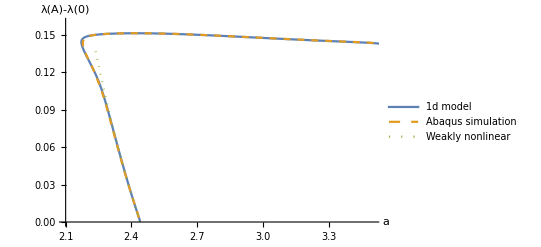

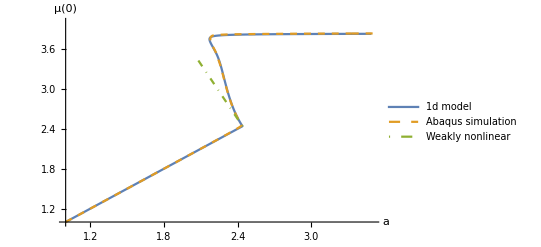

```mathematica
ListPlot[{Join[dataAmp[[1;;146]],dataAmp2[[1;;141]]],dataAmpAbaqus,dataAmpw},Joined->True,PlotStyle->{{Full},{Dashed},{Dotted}},AxesLabel->{HoldForm[a],HoldForm[λ[A]-λ[0]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotLegends->Placed[LineLegend[{"1d model","Abaqus simulation","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.5}],PlotRange->{{2.1,3.5},{0,0.16}}](*Figure 2(a) in the paper*)
dataμ0hom=Table[{x,x},{x,1,μcr,(μcr-1)/100}];
ListPlot[{Join[dataμ0hom,dataμ0[[1;;146]],dataμ02[[1;;131]]],dataμ0Abaqus,dataμ0w},Joined->True,PlotStyle->{Full,Dashed,DotDashed},AxesLabel->{HoldForm[a],HoldForm[μ[0]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotLegends->Placed[LineLegend[{"1d model","Abaqus simulation","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.2}],PlotRange->{{1,3.5},{1,4}}] (*Figure 2(b) in the paper*)
```

#### 8. Necking solutions at particular values of a

{2.39958,2.30051,2.20198,2.6}

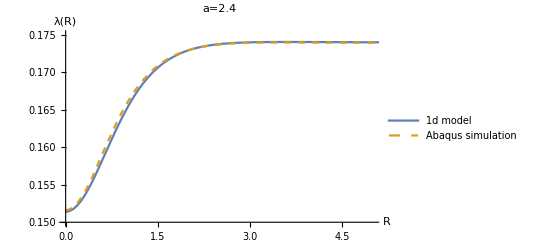

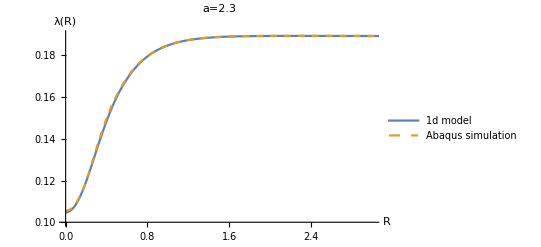

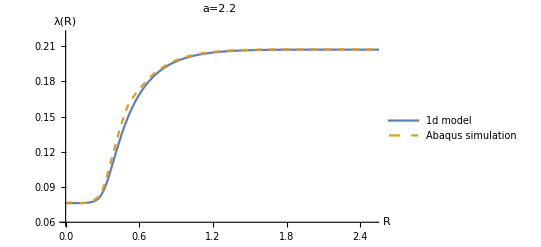

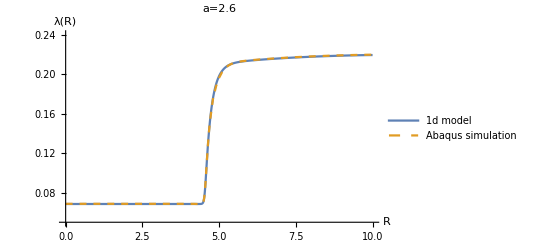

```mathematica
sollist={datasol[[13]],datasol[[65]],datasol[[118]],datasol2[[42]]};
Table[μ[n]/.sollist[[i]],{i,1,Length[sollist]}](* corresponding value of a=μ[A]*)
λ1d1[R_]=Piecewise[Table[{((h+h j-R) λ[j]+(-h j+R) λ[1+j])/h/.sollist[[1]],j h<=R<(j+1)h},{j,0,n-1}]];
λ1d2[R_]=Piecewise[Table[{((h+h j-R) λ[j]+(-h j+R) λ[1+j])/h/.sollist[[2]],j h<=R<(j+1)h},{j,0,n-1}]];
λ1d3[R_]=Piecewise[Table[{((h+h j-R) λ[j]+(-h j+R) λ[1+j])/h/.sollist[[3]],j h<=R<(j+1)h},{j,0,n-1}]];
λ1d4[R_]=Piecewise[Table[{((h+h j-R) λ[j]+(-h j+R) λ[1+j])/h/.sollist[[4]],j h<=R<(j+1)h},{j,0,n-1}]];
(*The followng figures corresponds Figure 3 in the paper*)
Plot[{λ1d1[R],λAbaqus1[R]},{R,0,A},PlotLegends->Placed[LineLegend[{"1d model","Abaqus simulation"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.6}],PlotStyle-> {Full,Dashed},AxesLabel->{HoldForm[R],HoldForm[λ[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotLabel->"a=2.4",PlotRange->{{0,5},{0.15,0.175}}]
Plot[{λ1d2[R],λAbaqus2[R]},{R,0,A},PlotLegends->Placed[LineLegend[{"1d model","Abaqus simulation"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.6}],PlotStyle-> {Full,Dashed},AxesLabel->{HoldForm[R],HoldForm[λ[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotLabel->"a=2.3",PlotRange->{{0,3},{0.1,0.19}}]
Plot[{λ1d3[R],λAbaqus3[R]},{R,0,A},PlotLegends->Placed[LineLegend[{"1d model","Abaqus simulation"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.6}],PlotStyle-> {Full,Dashed},AxesLabel->{HoldForm[R],HoldForm[λ[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotLabel->"a=2.2",PlotRange->{{0,2.5},{0.06,0.22}}]
Plot[{λ1d4[R],λAbaqus4[R]},{R,0,A},PlotLegends->Placed[LineLegend[{"1d model","Abaqus simulation"},LegendMarkerSize->{20,5}, LegendLayout->{"Column",1}],{0.74,0.4}],PlotStyle-> {Full,Dashed},AxesLabel->{HoldForm[R],HoldForm[λ[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotLabel->"a=2.6",PlotRange->{{0,10},{0.05,0.24}}]
```

#### 9 Evolution of axisymmetric necking given by the 1d model

{2.39958,2.30051,2.21981,2.17181,2.22,2.37}

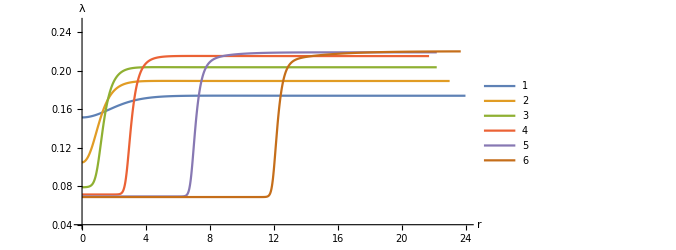

```mathematica
sollist={datasol[[13]],datasol[[65]],datasol[[112]],datasol[[131]],datasol2[[4]],datasol2[[19]]};(*solutions used to display the nekcing evolution*)
Table[μ[n]/.sollist[[i]],{i,1,Length[sollist]}](* corresponding value of a=μ[A]*)
Table[μevo[R_,i]=Piecewise[Table[{((h+h j-R) μ[j]+(-h j+R) μ[1+j])/h/.sollist[[i]],j h<=R<(j+1)h},{j,0,n-1}]],{i,1,Length[sollist]}];
Table[λevo[R_,i]=Piecewise[Table[{((h+h j-R) λ[j]+(-h j+R) λ[1+j])/h/.sollist[[i]],j h<=R<(j+1)h},{j,0,n-1}]],{i,1,Length[sollist]}];
ParametricPlot[Table[{μevo[R,i]*R,λevo[R,i]},{i,1,Length[sollist]}]//Evaluate,{R,0,A-0.01h},PlotLegends->Automatic,AxesLabel->{HoldForm[r],HoldForm[λ]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},AspectRatio->1/2,PlotRange->{{0,24},{0.04,0.25}},ImageSize->500](*Figure 4 in the paper*)
```

```mathematica
endtime= DateList[]
```

{2024,12,1,13,45,59.305102}

```mathematica
hours=endtime[[4]]-starttime[[4]];minutes=endtime[[5]]-starttime[[5]];
seconds=endtime[[6]]-starttime[[6]] ;
If[minutes<0, (minutes=(minutes+60))&&(hours=hours-1)];
If[seconds<0, (seconds=(seconds+60))&&(minutes=minutes-1)];
```

```mathematica
Print["total run time =",hours, " hours +  ", minutes, " minutes +  ",seconds," seconds"]
```

total run time =2 hours +  41 minutes +  51.463233 seconds